# Figure Plots

```mathematica
SetDirectory[NotebookDirectory[]]
```

S:\OneDrive\dinosaur research\fabbri et al rebuttal\mathematica for github

## Plot Functions

```mathematica
logticks =  Join[Table[{Log[10^k],10^k},{k,0,3}],Flatten[Table[{Log[j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
log10ticks = Join[Table[{k,10^k},{k,0,3}],Flatten[Table[{Log[10,j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
xlines[pt_,armlen_]:= {Line[{pt-{armlen,0},pt+{armlen,0}}],Line[{pt-{0,armlen},pt+{0,armlen}}]};
```

```mathematica
xlines2[pt_,{armlen1_,armlen2_}]:= {Line[{pt-{armlen1,0},pt+{armlen1,0}}],Line[{pt-{0,armlen2},pt+{0,armlen2}}]};
```

```mathematica
topticklabel[min_,max_,lab_]:= {{min,Style[lab,"Arial",12,Bold],0}};
```

```mathematica
mswordsize = 6.5*72;
```

## Data Import

```mathematica
femurraw = Import["2021-07-11463C-Bone density dataset.csv"];
ribraw = Import["2021-07-11463C-Bone density dataset - ribs.csv"];
```

```mathematica
{Range[Length[femurraw[[1]]]],femurraw[[1]],ribraw[[1]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
taxa | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD log | Flying | Diving | finest.category | diving.or.not | Morphsource specimen identifier | Morphosource specimen link | Morphosource scan link
Taxon | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD Log | Flying | Diving | finest.category | diving.or.not | Morphsource specimen identifier | Morphosource specimen link | Morphosource scan link

```mathematica
femurdata = DeleteCases[ Map[{#[[1]],#[[12]],#[[13]],{#[[10]],#[[9]]}}&,Drop[femurraw,1]],{"","","",{"",""}}];
```

```mathematica
femurdata[[1]]
```

{Alca_torda,2,2,{3.4,0.602}}

```mathematica
ribdata = DeleteCases[ Map[{#[[1]],#[[12]],#[[13]],{#[[10]],#[[9]]}}&,Drop[ribraw,1]],{"","","",{"",""}}];
```

```mathematica
Cases[femurdata,{_,"","",_}]
```

{}

```mathematica
(*ListPlot[femurdata[[All,-1]]]*)
```

```mathematica
(*ListPlot[ribdata[[All,-1]]]*)
```

```mathematica
femurbyfd = GatherBy[femurdata,{#[[2]],#[[3]]}&];
ribbyfd = GatherBy[ribdata,{#[[2]],#[[3]]}&];
femurbyfd2=Cases[femurbyfd,a_List/;Length[a]>4];
ribbyfd2=Cases[ribbyfd,a_List/;Length[a]>4];
```

```mathematica
femurbyfdpts = Map[Last,femurbyfd,{2}];
ribbyfdpts = Map[Last,ribbyfd,{2}];
```

```mathematica
femurbyfdpts2= DeleteCases[femurbyfdpts,a_List/;Length[a]<=4];
ribbyfdpts2= DeleteCases[ribbyfdpts,a_List/;Length[a]<=4];
```

```mathematica
lfemurpts2 = Map[{Log[#[[1]]],#[[2]]}&,femurbyfdpts2,{2}];
```

```mathematica
lribpts2 = Map[{Log[#[[1]]],#[[2]]}&,ribbyfdpts2,{2}];
```

```mathematica
Length[femurbyfd]
```

11

```mathematica
Length[ribbyfd]
```

9

```mathematica
Length[femurbyfd2]
```

7

```mathematica
Length[ribbyfd2]
```

6

```mathematica
taxanames = femurbyfd[[All,All,1]]/."Spinosaurus_"-> "Spinosaurus";
ribtaxanames = ribbyfd[[All,All,1]]/."Spinosaurus_"-> "Spinosaurus";
```

```mathematica
taxanames2 = DeleteCases[femurbyfd[[All,All,1]],a_List/;Length[a]<= 2]/."Spinosaurus_"-> "Spinosaurus";
ribtaxanames2 = DeleteCases[ribbyfd[[All,All,1]],a_List/;Length[a]<= 2]/."Spinosaurus_"-> "Spinosaurus";
```

```mathematica
femurgroupnames = Map[StringJoin["F",ToString[#[[1]]],"D",ToString[#[[2]]]]&,femurbyfd2[[All,1,{2,3}]]/."UNKNOWN"->"u"]
```

{F2D2,F0D2,F0Du,F2D1,F0D0,F2D0,F1D0}

```mathematica
ribgroupnames = Map[StringJoin["F",ToString[#[[1]]],"D",ToString[#[[2]]]]&,ribbyfd2[[All,1,{2,3}]]/."UNKNOWN"->"u"]
```

{F0D2,F0D0,F2D1,F2D2,F2D0,F0Du}

```mathematica
Join[{{"#","Name","Flying","Diving","Taxa"}},Map[Flatten,Transpose[{Range[Length[femurbyfd]],Map[StringJoin["F",ToString[#[[1]]],"D",ToString[#[[2]]]]&,femurbyfd[[All,1,{2,3}]]/."UNKNOWN"->"u"],femurbyfd[[All,1,{2,3}]]/."UNKNOWN"->"u",Map[Length,femurbyfd]}]]]//TableForm
```

# | Name | Flying | Diving | Taxa
1 | F2D2 | 2 | 2 | 11
2 | F0D2 | 0 | 2 | 59
3 | F0Du | 0 | u | 39
4 | F0D1 | 0 | 1 | 3
5 | F2D1 | 2 | 1 | 10
6 | F0D0 | 0 | 0 | 59
7 | F2D0 | 2 | 0 | 13
8 | FuD0 | u | 0 | 1
9 | F1D0 | 1 | 0 | 6
10 | F1D1 | 1 | 1 | 1
11 | FuDu | u | u | 4

```mathematica
Join[{{"#","Name","Flying","Diving","Taxa"}},Map[Flatten,Transpose[{Range[Length[femurbyfd2]],Map[StringJoin["F",ToString[#[[1]]],"D",ToString[#[[2]]]]&,femurbyfd2[[All,1,{2,3}]]/."UNKNOWN"->"u"],femurbyfd2[[All,1,{2,3}]]/."UNKNOWN"->"u",Map[Length,femurbyfd2]}]]]//TableForm
```

# | Name | Flying | Diving | Taxa
1 | F2D2 | 2 | 2 | 11
2 | F0D2 | 0 | 2 | 59
3 | F0Du | 0 | u | 39
4 | F2D1 | 2 | 1 | 10
5 | F0D0 | 0 | 0 | 59
6 | F2D0 | 2 | 0 | 13
7 | F1D0 | 1 | 0 | 6

```mathematica
Join[{{"#","Name","Flying","Diving","Taxa"}},Map[Flatten,Transpose[{Range[Length[ribbyfd]],Map[StringJoin["F",ToString[#[[1]]],"D",ToString[#[[2]]]]&,ribbyfd[[All,1,{2,3}]]/."UNKNOWN"->"u"],ribbyfd[[All,1,{2,3}]]/."UNKNOWN"->"u",Map[Length,ribbyfd]}]]]//TableForm
```

# | Name | Flying | Diving | Taxa
1 | F0D2 | 0 | 2 | 49
2 | F0D0 | 0 | 0 | 63
3 | F2D1 | 2 | 1 | 18
4 | F2D2 | 2 | 2 | 10
5 | F2D0 | 2 | 0 | 17
6 | F0D1 | 0 | 1 | 2
7 | F0Du | 0 | u | 12
8 | F1D0 | 1 | 0 | 2
9 | F1D1 | 1 | 1 | 1

```mathematica
Join[{{"#","Name","Flying","Diving","Taxa"}},Map[Flatten,Transpose[{Range[Length[ribbyfd2]],Map[StringJoin["F",ToString[#[[1]]],"D",ToString[#[[2]]]]&,ribbyfd2[[All,1,{2,3}]]/."UNKNOWN"->"u"],ribbyfd2[[All,1,{2,3}]]/."UNKNOWN"->"u",Map[Length,ribbyfd2]}]]]//TableForm
```

# | Name | Flying | Diving | Taxa
1 | F0D2 | 0 | 2 | 49
2 | F0D0 | 0 | 0 | 63
3 | F2D1 | 2 | 1 | 18
4 | F2D2 | 2 | 2 | 10
5 | F2D0 | 2 | 0 | 17
6 | F0Du | 0 | u | 12

```mathematica
spinonames = {"Suchomimus","Baryonyx","Spinosaurus"};
```

```mathematica
spinonames2 = {"Su","Ba","Sp"};
```

```mathematica
spinopos = Flatten[Map[Position[taxanames2,#]&,spinonames],1]
```

{{3,28},{3,7},{3,27}}

```mathematica
ribspinonames = {"Baryonyx","Spinosaurus"};
```

```mathematica
ribspinonames2 = {"Ba","Sp"};
```

```mathematica
ribspinopos = Flatten[Map[Position[ribtaxanames2,#]&,ribspinonames],1]
```

{{6,3},{6,4}}

## Figure 1 - femur and rib polygon plots

### Range Plots - femur

```mathematica
femurlfpts = lfpts = Map[{Log[#[[1]]],#[[2]]}&,femurbyfdpts2,{2}];
```

```mathematica
lfemurspinopts =Table[lfpts[[spinopos[[k,1]],spinopos[[k,2]]]],{k,1,Length[spinonames]}]//N
```

{{4.79248,0.682},{5.03695,0.876},{4.40085,0.968}}

```mathematica
flys = Union[Position[femurbyfd,{_,f_,_,_}/;f>0][[All,1]]]
```

{1,5,7,9,10}

```mathematica
flyerpts = Flatten[femurbyfdpts[[flys]],1];
```

```mathematica
lflyerpts =  Map[{Log[#[[1]]],#[[2]]}&,flyerpts];
```

```mathematica
lfpts = Map[{Log[#[[1]]],#[[2]]}&,femurbyfdpts2,{2}];
```

```mathematica
pr = Map[MinMax,Transpose[Flatten[lfpts,1]]]
```

{{-0.0822952,6.15316},{0.279,0.989}}

```mathematica
fdnames = Map[StringJoin["F",ToString[#[[1]]],"D",ToString[#[[2]]]]&,femurbyfd2[[All,1,{2,3}]]/."UNKNOWN"-> "u"]
```

{F2D2,F0D2,F0Du,F2D1,F0D0,F2D0,F1D0}

```mathematica
colorrule = {"F2D2"->Green,"F0D2"->Blue,"F0Du"-> ColorData[112][3],"F2D1"->Cyan,"F0D0"->Brown,"F2D0"->Purple,"F1D0"->Red}
```

{F2D2→RGBColor[0, 1, 0],F0D2→RGBColor[0, 0, 1],F0Du→RGBColor[1., 0.607843, 0.],F2D1→RGBColor[0, 1, 1],F0D0→RGBColor[0.6, 0.4, 0.2],F2D0→RGBColor[0.5, 0, 0.5],F1D0→RGBColor[1, 0, 0]}

```mathematica
femurcolors= fdnames/. colorrule
```

{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1., 0.607843, 0.],RGBColor[0, 1, 1],RGBColor[0.6, 0.4, 0.2],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 0]}

```mathematica
verts = Table[MeshCoordinates[ConvexHullRegion[lfpts[[i]]]],{i,1,Length[lfpts]}];
```

```mathematica
fdnames[[4]]
```

F2D1

```mathematica
verts[[4]]
```

{{0.693147,0.411},{2.39516,0.279},{2.11142,0.481},{1.70656,0.501},{1.26976,0.512}}

```mathematica
labelindex = {4,9,4,2,2,3,3,3,1};
labelcoords = Table[verts[[i,labelindex[[i]]]],{i,1,Length[verts]}];
labelcoordsadj = labelcoords;
labelcoordsadj[[1]] = Mean[verts[[1,{5,3}]]];
labelcoordsadj[[5]] = {0.1,0.66};
```

```mathematica
shadeopacity = 0.3;
pointopacity = 0.6;
```

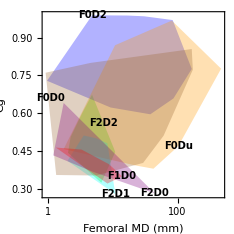

```mathematica
femurhullplot1 =Graphics[{Table[{femurcolors[[i]],{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[lfpts[[i]]]]]}},{i,1,Length[lfpts]}],
Table[Text[Style[fdnames[[i]],10,"Arial",Bold,Italic],labelcoordsadj[[i]],{0,0}],{i,1,Length[lfpts]}]},AspectRatio->1,PlotRange-> pr,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{logticks,topticklabel[#1,#2,"A"]&}},FrameLabel-> {"Femoral MD (mm)","Cg"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

```mathematica
(*GraphicsGrid[{{femurhull1,femurhull1}},Spacings->0,ImageSize->mswordsize]*)
```

```mathematica
{Range[7],femurgroupnames}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7
F2D2 | F0D2 | F0Du | F2D1 | F0D0 | F2D0 | F1D0

```mathematica
femurterra = femurbyfdpts2[[5]];
femurdiver = femurbyfdpts2[[2]];
```

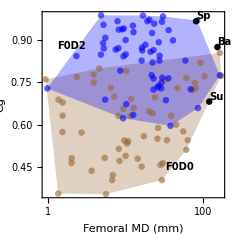

```mathematica
femurhullplot2 =Graphics[{
{Brown,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[Map[{Log[#[[1]]]//N,#[[2]]}&,femurterra]]]]}},
{Blue,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[Map[{Log[#[[1]]]//N,#[[2]]}&,femurdiver]]]]}},
{Brown,{Opacity[pointopacity],PointSize[.02],Map[Point[{Log[#[[1]]]//N,#[[2]]}]&,femurterra]}},
{Blue,{Opacity[pointopacity],PointSize[.02],Map[Point[{Log[#[[1]]]//N,#[[2]]}]&,femurdiver]}},
Table[{Black,PointSize[.02],Point[lfemurspinopts[[k]]]},{k,1,Length[spinonames]}],
Table[Text[Style[spinonames2[[k]],Black,10,Italic,Bold],lfemurspinopts[[k]],{-1,-1}],{k,1,Length[spinonames]}],
Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{logticks,topticklabel[#1,#2,"C"]&}},FrameLabel-> {"Femoral MD (mm)","Cg"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

```mathematica
Clear[cgvar]
```

```mathematica
cgvar[vl_]:= (Max[vl]-Min[vl])/Mean[vl];
```

```mathematica
{Mean[femurterra[[All,2]]],Mean[femurdiver[[All,2]]]}
```

{0.610271,0.840661}

```mathematica
femurgroupmeanvar = cgvar[{Mean[femurterra[[All,2]]],Mean[femurdiver[[All,2]]]}]
```

0.317575

```mathematica
0.186/femurgroupmeanvar
```

0.585689

### Rib Range Plots

```mathematica
ribsp = Union[Position[ribbyfd,{_,f_,_,_}/;f>0][[All,1]]]
```

{3,4,5,8,9}

```mathematica
ribflyerpts = Flatten[ribbyfdpts[[ribsp]],1]
```

{{3.49,0.32},{3.86,0.684},{6.54,0.262},{3.77,0.438},{2.35,0.375},{1.89,0.536},{2.48,0.539},{2.24,0.628},{5.03,0.754},{5.57,0.67},{2.1,0.728},{1.77,0.719},{3.55,0.705},{4.93,0.732},{2.31,0.797},{2.9,0.665},{0.9,0.638},{6.91,0.858},{1.5,0.924},{1.16,0.712},{3.42,0.648},{1.8,0.868},{1.25,0.798},{2.92,0.87},{1.84,0.832},{2.07,0.63},{2.66,0.84},{2.42,0.782},{5.05,0.46},{1.25,0.704},{2.17,0.571},{2.74,0.29},{2.26,0.491},{2.24,0.242},{1.06,0.554},{1.37,0.495},{0.58,0.375},{3.98,0.658},{1.2,0.777},{5.19,0.527},{1.91,0.683},{5.51,0.628},{0.969,0.765},{2.44,0.814},{1.39,0.848},{1.61,0.701},{0.927,0.769},{5.45,0.755}}

```mathematica
riblflyerpts =  Map[{Log[#[[1]]],#[[2]]}&,ribflyerpts];
```

```mathematica
riblfpts = Map[{Log[#[[1]]],#[[2]]}&,ribbyfdpts2,{2}];
```

```mathematica
ribpr = Map[MinMax,Transpose[Flatten[riblfpts,1]]]
```

{{-0.870839,Log[95]},{0.242,0.998}}

```mathematica
ribpr2 = Map[MinMax,Transpose[Flatten[{riblfpts[[1]],riblfpts[[2]],riblflyerpts},1]]]
```

{{-0.870839,4.35414},{0.242,0.998}}

```mathematica
ribfdnames = Map[StringJoin["F",ToString[#[[1]]],"D",ToString[#[[2]]]]&,ribbyfd2[[All,1,{2,3}]]/."UNKNOWN"-> "u"]
```

{F0D2,F0D0,F2D1,F2D2,F2D0,F0Du}

```mathematica
ribcolors = ribfdnames/.colorrule;
```

```mathematica
ribverts = Table[MeshCoordinates[ConvexHullRegion[riblfpts[[i]]]],{i,1,Length[riblfpts]}]
```

{{{-0.703198,0.848},{-0.259289,0.576},{2.05412,0.436},{3.85439,0.611},{4.35414,0.994},{2.02815,0.998},{0.993252,0.989}},{{-0.870839,0.695},{0.0582689,0.556},{2.0656,0.451},{3.68135,0.481},{4.01548,0.666},{3.45884,0.857},{1.60141,0.852},{-0.830113,0.77}},{{-0.105361,0.638},{0.854415,0.375},{1.2499,0.32},{1.87794,0.262},{1.93297,0.858},{0.837248,0.797}},{{0.14842,0.712},{0.727549,0.63},{1.22964,0.648},{1.07158,0.87},{0.405465,0.924},{0.223144,0.798}},{{-0.544727,0.375},{0.806476,0.242},{1.00796,0.29},{1.61939,0.46},{1.70656,0.628},{0.891998,0.814},{0.329304,0.848},{-0.0314907,0.765}},{{2.4248,0.631},{2.83908,0.513},{4.41401,0.523},{4.55388,0.84},{3.74242,0.921},{3.5582,0.931}}}

```mathematica
riblabelindex = {7,1,4,4,1,3};
```

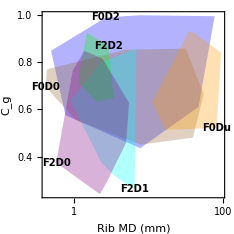

```mathematica
ribhullplot1 = Graphics[{Table[{ribcolors[[i]],{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[riblfpts[[i]]]]]}},{i,1,Length[riblfpts]}],
Table[Text[Style[ribfdnames[[i]],10,"Arial",Bold,Italic],ribverts[[i,riblabelindex[[i]]]],{0,0}],{i,1,Length[ribfdnames]}]},AspectRatio->1,PlotRange-> ribpr,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{logticks,topticklabel[#1,#2,"B"]&}},FrameLabel-> {"Rib MD (mm)","C_g"},FrameStyle-> Directive[Black,10,"Arial"],ImageSize->mswordsize/2]
```

```mathematica
{Range[6],ribgroupnames}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6
F0D2 | F0D0 | F2D1 | F2D2 | F2D0 | F0Du

```mathematica
ribterra = ribbyfdpts2[[2]];
ribdiver = ribbyfdpts2[[1]];
```

```mathematica
lribspinopts =Table[riblfpts[[ribspinopos[[k,1]],ribspinopos[[k,2]]]],{k,1,Length[ribspinonames]}]//N
```

{{3.74242,0.921},{3.5582,0.931}}

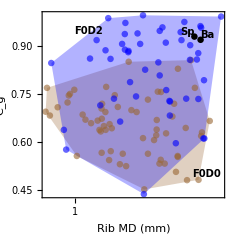

```mathematica
ribhullplot2 =Graphics[{
{Brown,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[Map[{Log[#[[1]]]//N,#[[2]]}&,ribterra]]]]}},
{Blue,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[Map[{Log[#[[1]]]//N,#[[2]]}&,ribdiver]]]]}},
{Brown,{Opacity[pointopacity],PointSize[.02],Map[Point[{Log[#[[1]]]//N,#[[2]]}]&,ribterra]}},
{Blue,{Opacity[pointopacity],PointSize[.02],Map[Point[{Log[#[[1]]]//N,#[[2]]}]&,ribdiver]}},
Table[{Black,PointSize[.02],Point[lribspinopts[[k]]]},{k,1,Length[ribspinonames]}],
Table[Text[Style[ribspinonames2[[k]],Black,10,Italic,"Arial",Bold],lribspinopts[[k]],{(-1)^k,-1}],{k,1,Length[ribspinonames]}],
Text[Style["F0D2",10,"Arial",Italic,Bold],{Log[1.5],0.95},{0,0}],
Text[Style["F0D0",10,"Arial",Italic,Bold],{Log[50],0.5},{0,0}](*,
Text[Style["Original",14],Scaled[{0.03,0.97}],{-1,1}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{logticks,topticklabel[#1,#2,"D"]&}},FrameLabel-> {"Rib MD (mm)","C_g"},FrameStyle-> Directive[Black,10,"Arial"],ImageSize->mswordsize/2]
```

### Figure 1 all together

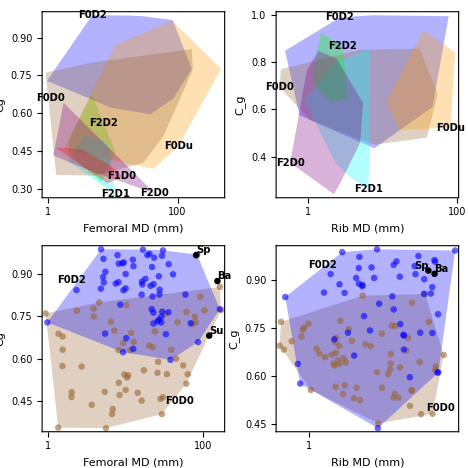

```mathematica
fig1plot = GraphicsGrid[{{femurhullplot1,ribhullplot1},{femurhullplot2,ribhullplot2}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
Export["figure1plot.tif",Rasterize[fig1plot,ImageResolution->300],"TIFF"]
```

figure1plot.tif

## Fig 2 - LDA Examples

### LDA functions

```mathematica
lda2[set1_,set2_]:= 
Module[{mn1,mn2,sww,vv,dir},
mn1 = Map[Mean,Transpose[set1]];
mn2 = Map[Mean,Transpose[set2]];
sww= Total[Map[{{#[[1]],0},{#[[2]],0}}.{#,{0,0}}&,Map[#-mn1&,set1]]]+Total[Map[{{#[[1]],0},{#[[2]],0}}.{#,{0,0}}&,Map[#-mn2&,set2]]];
vv = LinearSolve[sww,mn1-mn2];
dir = vv/Norm[vv];
Reverse[dir]*{-1,1}
];
```

```mathematica
lineside[linept_,linedir_,pt_]:=
Module[{adjpt},
adjpt =  pt-linept;
linedir[[1]]*adjpt[[2]]-linedir[[2]]*adjpt[[1]]
];
```

```mathematica
sl1 = SwatchLegend[{ColorData[97][1],ColorData[97][2]},{"Group 1","Group 2"},LegendMarkers->"Bubble",LegendFunction->Framed,LabelStyle->Directive[12,Black,"Arial"],LegendMargins->0]
```

```mathematica
plotlda3[dat1_,dat2_,label_]:=
Module[{cent1,cent2,cent,dir,side1,s1s,s2s,len1,len2,true1,false2,true2,false1,cmat,pr,pradj,perpdir,tboundsx,tboundsy,lowt,arrowpt,eqn1,prange,arrowlen},
cent1 = Map[Mean,Transpose[dat1]];
cent2 = Map[Mean,Transpose[dat2]];
cent =  (cent1+cent2)/2;
dir = lda2[dat1,dat2];
side1 = Sign[lineside[cent,dir,cent1]];
s1s = Map[Sign[lineside[cent,dir,#]]&,dat1];
s2s = Map[Sign[lineside[cent,dir,#]]&,dat2];
len1 = Length[dat1];
len2 = Length[dat2];
true1 = Count[s1s,side1];
false1 = len1-true1;
true2 = Count[s2s,-side1];
false2 = len2-true2;
cmat = {{true1,false1},{false2,true2}};
pr = Map[MinMax,Transpose[Join[dat1,dat2]]];
pradj = {Min[pr[[1,1]],pr[[2,1]]],Max[pr[[1,2]],pr[[2,2]]]};
prange = pradj[[2]]-pradj[[1]];
arrowlen = prange/12;
perpdir = {-dir[[2]],dir[[1]]}/Norm[dir];
tboundsx = Map[(#-cent[[1]])/dir[[1]]&, pr[[1]]];
tboundsy = Map[(#-cent[[2]])/dir[[2]]&, pr[[2]]];
lowt = Max[tboundsx[[1]],tboundsy[[2]]];
arrowpt = cent+0.75*lowt*dir;
eqn1 = c == cmat;
ListPlot[{dat1,dat2},PlotStyle-> Directive[PointSize[.012]],PlotRange->{pradj,pradj},PlotRangePadding-> Scaled[0.04],Axes-> False, Frame-> True,FrameStyle-> Directive[Black,10,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,label]&}}, AspectRatio-> 1,
Epilog-> {{Red,Arrowheads[{-0.04,0.04}],Arrow[{arrowpt-arrowlen*perpdir,arrowpt+arrowlen*perpdir}]},
{Red,Line[{cent+20*dir,cent-20*dir}]},
Text[Style["Classify as group 1",14,Italic,Red,"Arial"],arrowpt-arrowlen*perpdir,{-1,-1}],
Text[Style["Classify as
group 2",14,Italic,Red,"Arial"],arrowpt+arrowlen*perpdir,{0,1}],
Text[Style[eqn1//TraditionalForm,14],Scaled[{0.97,0.2}],{1,-1},Background-> White],
Inset[sl1,Scaled[{0.97,0.03}],{Right,Bottom},Background->White]
},ImageSize->mswordsize]
];
```

```mathematica
plotlda3a[dat1_,dat2_,label_]:=
Module[{cent1,cent2,cent,dir,side1,s1s,s2s,len1,len2,true1,false2,true2,false1,cmat,pr,pradj,perpdir,tboundsx,tboundsy,lowt,arrowpt,eqn1,prange,arrowlen},
cent1 = Map[Mean,Transpose[dat1]];
cent2 = Map[Mean,Transpose[dat2]];
cent =  (cent1+cent2)/2;
dir = lda2[dat1,dat2];
side1 = Sign[lineside[cent,dir,cent1]];
s1s = Map[Sign[lineside[cent,dir,#]]&,dat1];
s2s = Map[Sign[lineside[cent,dir,#]]&,dat2];
len1 = Length[dat1];
len2 = Length[dat2];
true1 = Count[s1s,side1];
false1 = len1-true1;
true2 = Count[s2s,-side1];
false2 = len2-true2;
cmat = {{true1,false1},{false2,true2}};
pr = Map[MinMax,Transpose[Join[dat1,dat2]]];
pradj = {Min[pr[[1,1]],pr[[2,1]]],Max[pr[[1,2]],pr[[2,2]]]};
prange = pradj[[2]]-pradj[[1]];
arrowlen = prange/12;
perpdir = {-dir[[2]],dir[[1]]}/Norm[dir];
tboundsx = Map[(#-cent[[1]])/dir[[1]]&, pr[[1]]];
tboundsy = Map[(#-cent[[2]])/dir[[2]]&, pr[[2]]];
lowt = Max[tboundsx[[1]],tboundsy[[2]]];
arrowpt = cent+0.75*lowt*dir;
eqn1 = c == cmat;
ListPlot[{dat1,dat2},PlotStyle-> Directive[PointSize[.015]],PlotRange->{pradj,pradj},PlotRangePadding-> Scaled[0.04],Axes-> False, Frame-> True,FrameStyle-> Directive[Black,10,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,label]&}}, AspectRatio-> 1,
Epilog-> {{ColorData[97][1],Thick,Arrowheads[{0,0.05}],Arrow[{arrowpt,arrowpt-arrowlen*perpdir}]},
{ColorData[97][2],Thick,Arrowheads[{0,0.05}],Arrow[{arrowpt,arrowpt+arrowlen*perpdir}]},
{Red,Line[{cent+20*dir,cent-20*dir}]},
Text[Style["G1",14,Italic,ColorData[97][1],"Arial"],arrowpt-arrowlen*perpdir,{-1,-1}],
Text[Style["G2",14,Italic,ColorData[97][2],"Arial"],arrowpt+arrowlen*perpdir,{0,1}],
Text[Style[eqn1//TraditionalForm,12],Scaled[{0.98,0.02}],{1,-1}](*,
Inset[sl1,Scaled[{0.97,0.03}],{Right,Bottom},Background->White]*)
},ImageSize->mswordsize/2]
];
```

```mathematica
ldaclasscounts[dat1_,dat2_]:=
Module[{cent1,cent2,cent,dir,side1,s1s,s2s,len1,len2,true1,false2,true2,false1},
cent1 = Map[Mean,Transpose[dat1]];
cent2 = Map[Mean,Transpose[dat2]];
cent =  (cent1+cent2)/2;
dir = lda2[dat1,dat2];
side1 = Sign[lineside[cent,dir,cent1]];
s1s = Map[Sign[lineside[cent,dir,#]]&,dat1];
s2s = Map[Sign[lineside[cent,dir,#]]&,dat2];
len1 = Length[dat1];
len2 = Length[dat2];
true1 = Count[s1s,side1]+0.5Count[s1s,0];
false1 = len1-true1;
true2 = Count[s2s,-side1]+0.5Count[s2s,0];
false2 = len2-true2;
{{true1,false1},{false2,true2}}
];
```

```mathematica
accuracy[{{tp_,fn_},{fp_,tn_}}]:= (tp+tn)/(tp+tn+fn+fp);
```

### Point plots

```mathematica
stack3size = 8.5*72/3
```

204.

```mathematica
mswordsize/2
```

234.

```mathematica
dataplot1group1 = RandomVariate[MultinormalDistribution[{1.2,1.2},0.3{{1,0},{0,1}}],1000];
dataplot1group2 = RandomVariate[MultinormalDistribution[-{1.2,1.2},0.3{{1,0},{0,1}}],1000];
```

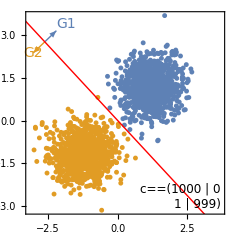

```mathematica
plot1raw = plotlda3a[dataplot1group1,dataplot1group2,"A"]
```

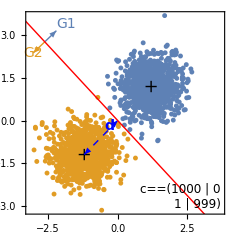

```mathematica
plot1 =Show[plot1raw,Graphics[{{Thick,Black,xlines[{1.2,1.2},0.2],xlines[-{1.2,1.2},0.2]},{Blue,Arrowheads[{-0.03,0.03}],Dashed,Arrow[{{0,0},-{1.2,1.2}}]},
Text[Style["d",14,Italic,Blue,Bold],{-.3,-.2},{1,0}]
}],ImageSize-> mswordsize/2]
```

```mathematica
dataplot2group1 = RandomVariate[MultinormalDistribution[{1.2,1.2},2{{1,0},{0,1}}],59];
dataplot2group2 = RandomVariate[MultinormalDistribution[-{1.2,1.2},2{{1,0},{0,1}}],59];
```

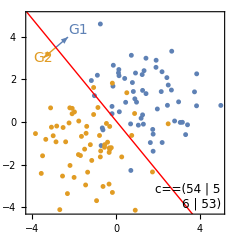

```mathematica
plot2raw = plotlda3a[dataplot2group1,dataplot2group2,"B"]
```

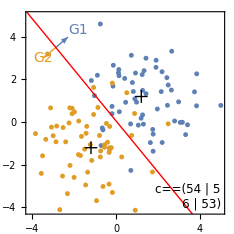

```mathematica
plot2 =Show[plot2raw,Graphics[{{Thick,Black,xlines[{1.2,1.2},0.3],xlines[-{1.2,1.2},0.3]}
}],ImageSize-> mswordsize/2]
```

### 3 D PDF Plot

```mathematica
plt0=Plot3D[
{
PDF[MultinormalDistribution[-1.2{1,1},2{{1,0},{0,1}}],{x,y}],PDF[MultinormalDistribution[1.2{1,1},2{{1,0},{0,1}}],{x,y}]},{x,-4,4},{y,-4,4},PlotRange->All,PlotPoints->100,AxesLabel->{x,y},PerformanceGoal->"Quality",LabelStyle->Directive[10,Black,"Arial"],Mesh->None,Epilog->{Text[Style["C",Bold,14,"Arial"],Scaled[{0,0.8}],{-1,1}]},ImageSize->mswordsize]
```

-Graphics3D-

```mathematica
firstMesh=Show[Table[
{ParametricPlot3D[
{u0,y,PDF[MultinormalDistribution[-1.2{1,1},2{{1,0},{0,1}}],{u0,y}]}
,{x,-4.,4.},{y,-4.,-u0},PlotStyle->Black],
ParametricPlot3D[
{x,u0,PDF[MultinormalDistribution[-1.2{1,1},2{{1,0},{0,1}}],{x,u0}]}
,{y,-4.,4.},{x,-4.,-u0},PlotStyle->Black]},{u0,-4.,4.}],BoxRatios->{1, 1, 1},PlotRange->All];
```

ParametricPlot3D::plld: Endpoints for y in {y,-4.,-4.} must have distinct machine-precision numerical values.

ParametricPlot3D::plld: Endpoints for x in {x,-4.,-4.} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot3D::plld will be suppressed during this calculation.

```mathematica
secondMesh=Show[Table[
{ParametricPlot3D[
{u0,y,PDF[MultinormalDistribution[1.2{1,1},2{{1,0},{0,1}}],{u0,y}]}
,{x,-4.,4.},{y,-u0,4.},PlotStyle->Black],
ParametricPlot3D[
{x,u0,PDF[MultinormalDistribution[1.2{1,1},2{{1,0},{0,1}}],{x,u0}]}
,{y,-4.,4.},{x,-u0,4.},PlotStyle->Black]},{u0,-4.,4.}],BoxRatios->{1, 1, 1},PlotRange->All];
```

ParametricPlot3D::plld: Endpoints for y in {y,4.,4.} must have distinct machine-precision numerical values.

ParametricPlot3D::plld: Endpoints for x in {x,4.,4.} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot3D::plld will be suppressed during this calculation.

```mathematica
decbound = ParametricPlot3D[
{-x,x,PDF[MultinormalDistribution[1.2{1,1},2{{1,0},{0,1}}],{-x,x}]}
,{x,-4,4},PlotStyle->Directive[Red,Thick]];
```

```mathematica
plotpdfs =Show[plt0,firstMesh,secondMesh,decbound]
```

-Graphics3D-

```mathematica
botrast = Rasterize[plotpdfs,ImageResolution->300];
```

```mathematica
top2rast = Rasterize[GraphicsGrid[{{plot1,plot2}},Spacings->0,ImageSize->mswordsize],ImageResolution->300]
```

-Graphics-

```mathematica
fig2plot = ImageAssemble[{{top2rast},{botrast}}]
```

-Graphics-

```mathematica
ImageDimensions[fig2plot]
```

{1950,2572}

```mathematica
Export["figure2plot.tif",fig2plot,"TIFF"]
```

figure2plot.tif

## Fig 12 - LDA finite size effects

### Decision boundary Monte Carlo

```mathematica
xx= 1.2;
bigdata1 = RandomVariate[MultinormalDistribution[xx{1,1},2{{1,0},{0,1}}],{500,59}];
bigdata2 = RandomVariate[MultinormalDistribution[xx{-1,-1},2{{1,0},{0,1}}],{500,59}];
```

```mathematica
markers = {Graphics[{Thick,Line[{{-0.5,0},{0.5,0}}]},ImageSize->100],Graphics[{Thick,xlines[{0,0},0.5]},ImageSize-> 100],Graphics[{PointSize[.33],Point[{0,0}]},ImageSize->100]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
sw3 = SwatchLegend[{Red,Magenta,Black},{"Decision boundary","Distribution centroid","Group centroid"},LegendMarkerSize->10,LegendMarkers->markers,LabelStyle->Directive[10,Black,"Arial"],LegendMargins->0]
```

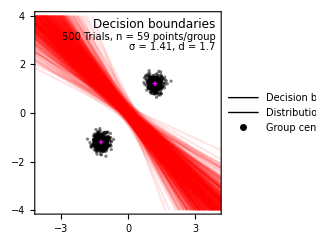

```mathematica
datapairs = Transpose[{bigdata1,bigdata2}];
dirslist = Map[lda2[#[[1]],#[[2]]]&,datapairs];
centlist = Map[Mean[Flatten[#,1]]&,datapairs];
cent12list =  Map[Mean[#]&,datapairs,{2}];
ptpairs = MapThread[{#1-20#2,#1+20#2}&,{centlist,dirslist}];
decbplot =ListPlot[ptpairs,Joined-> True,PlotStyle-> Directive[Red,Opacity[0.1]],Frame-> True,FrameStyle->Directive[10,Black,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},PlotRange-> 4{{-1,1},{-1,1}},AspectRatio-> Automatic, Axes-> False,Epilog-> {Text[Style["Decision boundaries",12],Scaled[{0.97,0.97}],{1,1}],Text[Style["500 Trials, n = 59 points/group",10],Scaled[{0.97,0.90}],{1,1}],
Text[Style["σ = 1.41, d = 1.7",10],Scaled[{0.97,0.85}],{1,1}],{Black,PointSize[.01],Opacity[.5],Map[Point,cent12list]},{Thick,Magenta,xlines[{1.2,1.2},0.1],xlines[-{1.2,1.2},0.1]},
Inset[sw3,Scaled[{0.03,0.03}],{Left,Bottom}]
},ImageSize->mswordsize/2]
```

### Accuracy histogram

```mathematica
combinewds[wds_List]:= 
Module[{wdslist,wdslg},
wdslist = Flatten[Map[Transpose,wds[[All,2]]],1];
wdslg =Transpose[Map[{#[[1,1]],Total[#[[All,2]]]}&,GatherBy[wdslist,First]]];
WeightedData[wdslg[[1]],wdslg[[2]]]
];
```

```mathematica
combinewds[{wd_WeightedData}]:= wd;
```

```mathematica
combinewds[wd_WeightedData]:= wd;
```

```mathematica
list2wd[list_]:= 
Module[{listwithrep},
listwithrep = Transpose[Tally[list]];
WeightedData[listwithrep[[1]],listwithrep[[2]]]
];
```

```mathematica
weighteddatahistoline[wdslist_]:=
Module[{wd,tlst,spts,pairs,sum,adjpts},
wd = combinewds[wdslist];
tlst = Transpose[wd[[2]]];
spts = SortBy[tlst,First];
pairs = Partition[spts,2,1];
sum = Total[Map[(#[[2,1]]-#[[1,1]])#[[1,2]]&,pairs]];
Map[{#[[1]],#[[2]]/sum}&,spts]
];
```

```mathematica
xx= 1.2;
rbigdata1 = RandomVariate[MultinormalDistribution[xx{1,1},2{{1,0},{0,1}}],{10000,59}];
rbigdata2 = RandomVariate[MultinormalDistribution[xx{-1,-1},2{{1,0},{0,1}}],{10000,59}];
```

```mathematica
rdatapairs = Transpose[{rbigdata1,rbigdata2}];
rcmats = Map[ldaclasscounts[#[[1]],#[[2]]]&,rdatapairs];
```

```mathematica
rbigdataaccuracy =Map[accuracy,rcmats]//N;
```

```mathematica
MinMax[rbigdataaccuracy]
```

{0.762712,0.983051}

```mathematica
rbighistoline = weighteddatahistoline[list2wd[rbigdataaccuracy]];
```

```mathematica
qs = Quantile[rbigdataaccuracy,{0.025,0.5,0.975}]
```

{0.830508,0.889831,0.940678}

```mathematica
Map[MinMax,Transpose[rbighistoline]]
```

{{0.762712,0.983051},{0.0118012,13.9372}}

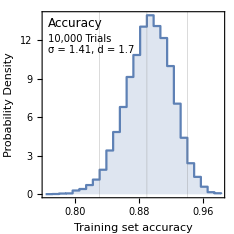

```mathematica
acchistoplot = ListPlot[rbighistoline,PlotRange-> Map[MinMax,Transpose[rbighistoline]],PlotRangePadding->Scaled[0.03],Joined->True, InterpolationOrder->0,Filling-> Axis,Frame->True,
FrameStyle-> Directive[Black,10,"Arial"],FrameLabel-> {"Training set accuracy", "Probability Density"},FrameTicks-> {{Automatic,Automatic},{Automatic,Join[{{0.77,Style["B",12,Bold,"Arial"]}},Map[{#,NumberForm[#,{4,3}]}&,qs]]}},GridLines-> {qs,None},
AspectRatio-> 1,Epilog-> {Text[Style["Accuracy",12],Scaled[{0.03,0.97}],{-1,1},Background->White],
Text[Style["10,000 Trials",10],Scaled[{0.03,0.88}],{-1,1},Background-> White],
Text[Style["σ = 1.41, d = 1.7",10],Scaled[{0.03,0.82}],{-1,1},Background-> White]
},
ImageSize->mswordsize/2]
```

### CI width from MonteCarlo

```mathematica
params = {0.5,1,Sqrt[2],2,4,8}
```

{0.5,1,√2,2,4,8}

```mathematica
sigs = Sqrt[params]//N
```

{0.707107,1.,1.18921,1.41421,2.,2.82843}

```mathematica
Clear[ci]
```

```mathematica
eqn2 = ci width==a/Sqrt[n]//TraditionalForm
```

ci width==a/(√n)

```mathematica
ranges = {{{500,0.01100000000000001},{324,0.01388888888888895},{210,0.016666666666666607},{136,0.018382352941176516},{88,0.022727272727272707},{57,0.026315789473684292},{37,0.027027027027026973},{24,0.04166666666666674},{15,0.033333333333333326},{10,0.04999999999999993}},{{500,0.025999999999999912},{324,0.03240740740740744},{210,0.03809523809523807},{136,0.047794117647058765},{88,0.05681818181818188},{57,0.07894736842105265},{37,0.09459459459459452},{24,0.10416666666666674},{15,0.1333333333333333},{10,0.1499999999999999}},{{500,0.03300000000000003},{324,0.040123456790123524},{210,0.050000000000000044},{136,0.06617647058823528},{88,0.07954545454545447},{57,0.0964912280701754},{37,0.1216216216216216},{24,0.14583333333333337},{15,0.16666666666666663},{10,0.19999999999999996}},{{500,0.040000000000000036},{324,0.04938271604938271},{210,0.059523809523809534},{136,0.07720588235294112},{88,0.09659090909090917},{57,0.11403508771929827},{37,0.14864864864864868},{24,0.1875},{15,0.2333333333333334},{10,0.25}},{{500,0.050000000000000044},{324,0.061728395061728336},{210,0.07619047619047625},{136,0.09558823529411764},{88,0.11931818181818177},{57,0.14912280701754388},{37,0.17567567567567566},{24,0.22916666666666663},{15,0.2666666666666667},{10,0.30000000000000004}},{{500,0.05599999999999994},{324,0.06944444444444442},{210,0.08571428571428574},{136,0.1066176470588236},{88,0.13636363636363646},{57,0.1578947368421052},{37,0.18918918918918914},{24,0.25},{15,0.33333333333333337},{10,0.4}}};
```

```mathematica
lranges = Map[Log,ranges]
```

{{{Log[500],-4.50986},{Log[324],-4.27667},{Log[210],-4.09434},{Log[136],-3.99636},{Log[88],-3.78419},{Log[57],-3.63759},{Log[37],-3.61092},{Log[24],-3.17805},{Log[15],-3.4012},{Log[10],-2.99573}},{{Log[500],-3.64966},{Log[324],-3.42937},{Log[210],-3.26767},{Log[136],-3.04085},{Log[88],-2.8679},{Log[57],-2.53897},{Log[37],-2.35815},{Log[24],-2.26176},{Log[15],-2.0149},{Log[10],-1.89712}},{{Log[500],-3.41125},{Log[324],-3.21579},{Log[210],-2.99573},{Log[136],-2.71543},{Log[88],-2.53143},{Log[57],-2.3383},{Log[37],-2.10684},{Log[24],-1.92529},{Log[15],-1.79176},{Log[10],-1.60944}},{{Log[500],-3.21888},{Log[324],-3.00815},{Log[210],-2.82138},{Log[136],-2.56128},{Log[88],-2.33727},{Log[57],-2.17125},{Log[37],-1.90617},{Log[24],-1.67398},{Log[15],-1.45529},{Log[10],-1.38629}},{{Log[500],-2.99573},{Log[324],-2.78501},{Log[210],-2.57452},{Log[136],-2.34771},{Log[88],-2.12596},{Log[57],-1.90299},{Log[37],-1.73912},{Log[24],-1.47331},{Log[15],-1.32176},{Log[10],-1.20397}},{{Log[500],-2.8824},{Log[324],-2.66723},{Log[210],-2.45674},{Log[136],-2.23851},{Log[88],-1.99243},{Log[57],-1.84583},{Log[37],-1.66501},{Log[24],-1.38629},{Log[15],-1.09861},{Log[10],-0.916291}}}

```mathematica
lranges2 = Table[Map[Log[{#[[1]],#[[2]]/sigs[[i]]}]&,ranges[[i]]],{i,1,Length[ranges]}];
```

```mathematica
nmfs = Map[NonlinearModelFit[#,a-0.5x,{a},x]&,lranges2]
```

{FittedModel[-1.27316-0.5 x],FittedModel[-0.60388-0.5 x],FittedModel[-0.508658-0.5 x],FittedModel[-0.471812-0.5 x],FittedModel[-0.611398-0.5 x],FittedModel[-0.825899-0.5 x]}

```mathematica
tworow[pairs_]:= TableForm[Map[Flatten,Partition[pairs,3]]];
```

```mathematica
siglegend = LineLegend[Table[Directive[ColorData[97][i],Thickness[.01]],{i,1,6}],Map[NumberForm[#,{3,2}]&,sigs//N],LegendLabel->Style["σ",10],LegendLayout->tworow,LabelStyle->Directive[8,"Arial",Black],LegendMargins->0,LegendMarkerSize->8]
```

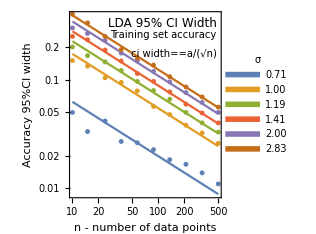

```mathematica
empiricalciplot = LogLogPlot[Evaluate[sigs*Map[Exp[#[Log[x]]]&,nmfs]],{x,10,500},
PlotRangePadding->{Automatic,{Scaled[0.12],Scaled[0.03]}},Axes-> False,Epilog->{Text[Style["LDA 95% CI Width",12],Scaled[{0.97,0.97}],{1,1}],Text[Style["Training set accuracy",10],Scaled[{0.97,0.90}],{1,1}],
Text[Style[eqn2,10],Scaled[{0.97,0.80}],{1,1}],Inset[siglegend,Scaled[{0.03,0.03}],{Left,Bottom}],Table[{PointSize[.015],ColorData[97][i],Map[Point,lranges[[i]]]},{i,1,Length[lranges]}]},PlotRange-> All,Frame-> True,FrameStyle->Directive[Black,10,"Arial"],FrameLabel-> {"n - number of data points","Accuracy 95%CI width"},
FrameTicks->{{Automatic,None},{Automatic,topticklabel[#1,#2,"C"]&}},AspectRatio-> 1,ImageSize->mswordsize/2]
```

### CI width plot 2

```mathematica
Norm[{1,1}-{-1,-1}]
```

2 √2

```mathematica
mclda[doversig_, npts_,ntrials_]:=
Module[{rdata1,rdata2,rdata,acc},
rdata1 = RandomVariate[MultinormalDistribution[(doversig/2Sqrt[2]){1,1},{{1,0},{0,1}}],{ntrials,npts}];
rdata2 = RandomVariate[MultinormalDistribution[(doversig/2Sqrt[2]){-1,-1},{{1,0},{0,1}}],{ntrials,npts}];
rdata = Transpose[{rdata1,rdata2}];
acc = Map[accuracy[ldaclasscounts[#[[1]],#[[2]]]]&,rdata];
 Quantile[acc,{0.025,0.975}]
];
```

```mathematica
DistributeDefinitions[mclda,ldaclasscounts]
```

{mclda,accuracy,ldaclasscounts,lda2,lineside}

```mathematica
Table[10*2^k,{k,0,6}]
```

{10,20,40,80,160,320,640}

```mathematica
AbsoluteTiming[cicurves1 = ParallelTable[{10*2^k,mclda[dos,10*2^k,10000]},{dos,0.5,2.5,.5},{k,0,8}];]
```

{1331.25,Null}

```mathematica
AbsoluteTiming[cicurves2 = ParallelTable[{10*2^k,mclda[dos,10*2^k,20000]},{dos,{2.5,3}},{k,0,6}];]
```

{690.004,Null}

```mathematica
cicurvest = Map[{#[[1]],#[[2,1]]}&,Join[cicurves1,cicurves2],{2}];
```

```mathematica
cicurvest = Map[{#[[1]],#[[2,1]]}&,cicurves1,{2}];
```

```mathematica
doslist = Range[0.5,2.5,0.5]
```

{0.5,1.,1.5,2.,2.5}

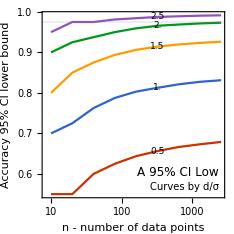

```mathematica
cilowerboundplot = ListLogLinearPlot[cicurvest,Joined->True,PlotRange-> Map[MinMax,Transpose[Flatten[cicurvest,1]]],PlotRangePadding->Scaled[0.03],PlotStyle-> 112,Frame-> True,FrameStyle->Directive[Black,9,"Arial"],FrameLabel-> {"n - number of data points","Accuracy 95% CI lower bound"},
FrameTicks->{{Automatic,{0.975}},{Automatic,topticklabel[#1,#2,"D"]&}},
GridLines-> {None,{0.975}},
Epilog->{Text[Style["A 95% CI Low",12],Scaled[{0.97,0.1}],{1,-1}],Text[Style["Curves by d/σ",10],Scaled[{0.97,0.03}],{1,-1}],Table[Text[Style[ToString[doslist[[i]]],9],{Log[cicurvest[[i,6,1]]],cicurvest[[i,6,2]]},{0,0},Background->White],{i,1,Length[doslist]}]},
AspectRatio-> 1,ImageSize->mswordsize/2]
```

```mathematica
FindRoot[1-(1/2.)Erfc[x/Sqrt[2]] == 0.975,{x,2.5}]
```

{x→1.95996}

```mathematica
Table[1-(1/2.)Erfc[x/Sqrt[2]] ,{x,doslist}]96
```

{66.3804,80.7691,89.5865,93.816,95.4039}

```mathematica
cicurvest[[-1]]
```

{{10,0.95},{20,0.975},{40,0.975},{80,0.98125},{160,0.984375},{320,0.9875},{640,0.989063},{1280,0.990625},{2560,0.991602}}

```mathematica
cicurvest[[-2,-1]]
```

{2560,0.973242}

### Figure 12

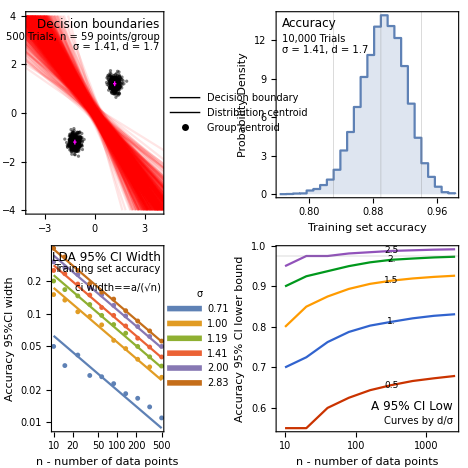

```mathematica
fig12plot = GraphicsGrid[{{decbplot,acchistoplot},{empiricalciplot,cilowerboundplot}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
Export["figure12plot.tif",Rasterize[fig12plot,ImageResolution->300],"TIFF"]
```

figure12plot.tif

## Fig 14 - Discriminant Plots

#### Discriminant data

From ds1 and ds2, F0D0 vs F0D2

```mathematica
fdiscbyclass ={{0.1673563028097216,0.439926183927034,-1.922731437354999,-1.151356101412108,0.3103074572377685,0.3298469093560582,-0.2513593877276705,-0.6220310811999185,-0.7157254918736934,-0.11370478740041604,-0.37566528404595806,-0.6216804824059051,-1.4247096759261022,-0.4120967153406295,-1.330631608604355,-0.43643825043325046,1.0602535812969835,0.5903143402119944,0.24178258527753496,-1.938339168449175,0.47357317606317323,-0.9127025111201281,-0.9584277440194704,-0.5102958776173588,-0.45223540577456156,-2.0497357616817804,-1.2011809897260821,0.014714806550293703,0.32194510573705115,-0.7547239193802845,-1.8192414939178305,-1.1969627926045987,-1.47848206122433,-1.9670409186559916,-1.2517454613845187,0.4864184982305844,0.6952716317467577,-1.1991454563454746,0.7365638243331556,-1.898246770038551,1.365024232051833,0.6513433711161859,0.6845878908988104,-0.0787801744254809,-0.26508296833520795,-2.244030027181247,0.6025058647406464,-1.1383831607491415,-1.7338553252832363,-2.2382991011757127,-2.737777403912854,-0.9668593422477891,-1.8606351910459344,-1.5719832616973983,-1.3759868599616372,-2.161040212283875,-2.790746708296052,-2.3409338495817322},{1.1333705761359925,0.4362942913800992,-0.14180218621924073,0.06608943569184232,1.48796210953157,1.192639451224252,0.2562967966130752,0.22485025319297638,2.23410867330532,2.1945846205916992,0.9832501540630858,-0.09527404859899781,1.3293471187183672,1.865920742825315,2.371459051220367,1.5995892647814376,0.5561164234033735,0.5719080383724999,0.272403078640695,1.113397432730644,1.0674385705359117,-0.8561903638693493,1.3232736964023015,1.9415715444856996,2.0518579770107546,0.3298806612936043,-0.6762973538406594,0.8789281010197433,1.7165774115790045,1.5033617882624701,0.709481742110417,1.183292648730531,1.771329497596365,1.876884717880723,0.9308524778430529,0.09017968064208037,1.8548493586786774,1.236321597846418,1.5305776536467877,0.7635471734916577,0.5963801237757385,0.17862601815589507,-0.1263786339544307,1.5912761805880966,1.4724755708274389,1.2126885027534324,0.3689667217355734,-0.5197417821301203,2.52029425801159,1.4856040177097716,1.5165981895632832,0.8555166381637392,2.1133671954687037,-0.6809285661869857,1.406089447936062,1.762796693563474,1.318687345915038,0.9619810936830009,-0.25999344579305006}};
```

```mathematica
fdiscbyclasscentered ={{0.9844124535979092,1.2569823347152216,-1.1056752865668114,-0.3342999506239205,1.1273636080259561,1.1469030601442458,0.5656967630605171,0.19502506958826915,0.10133065891449422,0.7033513633877716,0.44139086674222955,0.19537566838228249,-0.6076535251379146,0.4049594354475581,-0.5135754578161674,0.38061790035493714,1.877309732085171,1.407370491000182,1.0588387360657225,-1.1212830176609874,1.290629326851361,-0.09564636033194052,-0.1413715932312828,0.30676027317082877,0.36482074501362605,-1.2326796108935927,-0.3841248389378945,0.8317709573384813,1.1390012565252388,0.062332231407903116,-1.0021853431296428,-0.3799066418164111,-0.6614259104361423,-1.149984767867804,-0.4346893105963311,1.303474649018772,1.5123277825349453,-0.38208930555728704,1.553619975121343,-1.0811906192503633,2.1820803828400206,1.4683995219043735,1.501644041686998,0.7382759763627067,0.5519731824529797,-1.4269738763930593,1.419562015528834,-0.32132700996095387,-0.9167991744950487,-1.421242950387525,-1.9207212531246665,-0.14980319145960153,-1.0435790402577467,-0.7549271109092107,-0.5589307091734496,-1.3439840614956875,-1.9736905575078643,-1.5238776987935445},{0.33016283468319785,-0.36691345007269544,-0.9450099276720354,-0.7371183057609523,0.6847543680787754,0.38943170977145736,-0.5469109448397194,-0.5783574882598183,1.4309009318525252,1.3913768791389045,0.1800424126102912,-0.8984817900517924,0.5261393772655726,1.0627130013725203,1.568251309767572,0.796381523328643,-0.24709131804942108,-0.23129970308029468,-0.5308046628120996,0.31018969127784934,0.2642308290831171,-1.6593981053221438,0.5200659549495069,1.138363803032905,1.2486502355579598,-0.4733270801591903,-1.479505095293454,0.07572035956694867,0.9133696701262098,0.7001540468096755,-0.09372599934237758,0.3800849072777365,0.9681217561435703,1.0736769764279286,0.1276447363902583,-0.7130280608107142,1.051641617225883,0.4331138563936233,0.727369912193993,-0.03966056796113693,-0.20682761767705615,-0.6245817232968995,-0.9295863754072253,0.788068439135302,0.6692678293746442,0.4094807613006378,-0.43424101971722123,-1.322949523582915,1.7170865165587954,0.682396276256977,0.7133904481104886,0.05230889671094463,1.310159454015909,-1.4841363076397802,0.6028817064832673,0.9595889521106794,0.5154796044622433,0.15877335223020628,-1.0632011872458447}};
```

```mathematica
rdiscbyclass ={{0.12204587081728537,-0.5739930544982649,-0.5900342311590894,-0.3018240027478353,-0.2835006963022949,-0.8210074279506078,-0.8546244967160526,-1.7597817021333166,-1.7420425998048,-0.7423678337326847,0.08320491022856859,-0.4682045251723951,0.2666800247220776,1.1258051284680501,-0.9943180404788778,-1.8186218884350935,-1.6398474961372806,-1.2508837571792166,-0.12618715454034327,-1.3809928773783462,-1.5100798587781712,-0.7666470256603561,-0.9927805722774942,-0.20913650929760105,-0.5131266023361698,-0.9586676472139953,-0.9904587121678166,-0.9691686274833442,-0.3008472337398761,-0.8909682803596091,-0.741672038778845,-1.3076615235743574,-0.8228865278976311,-1.4412592567942055,1.3702976307438428,0.574817928912277,-0.7017311340763359,-0.8835323136833254,-0.3814876915376749,-0.19424616710238937,-0.021643334746340705,0.1978580513888253,1.6876851963572381,0.9631493981840086,-0.25656413849427645,-1.0376386349061768,-1.446221650746315,-2.224213841031467,0.40732523657883707,-0.15291240514812984,-1.5736584049139393,-0.21107209328421073,-0.7844614602772637,-0.6330735555169776,-1.284501639215647,-0.8708997556342352,-0.35722331085385967,-0.49513620472691305,-1.2996520747816045,-1.5651728610515672,-0.2305225480549704,-1.0665999822802303},{0.44680383615161673,1.6614564415437572,1.9396349544125329,1.524537782804097,1.8909667675352548,-0.18332006170102727,2.155001719595267,1.929345000887594,0.39033353754596817,1.2291109590397116,1.3610375998799438,0.8478582101877324,1.8966158234286077,1.1518102121086402,0.8063647599277557,0.8289609432378396,-0.25935455055636625,1.4175532731549585,-0.49309028997738436,1.5116872548998335,-1.251200675269033,0.9486658365558046,1.2767937299337746,-1.8196017278650238,0.41832995382281674,0.4051156958368924,2.5199501653750045,-2.383526214358447,1.6989347146709093,1.3598501300588777,-0.3565893623856996,-0.7274999617809207,0.6420862780456628,0.35710679848481963,1.2500926924254288,2.619998919006877,2.3050569529218166,-0.3743305435882448,0.13873516406164307,0.5419431261569555,1.638916121139876,1.9002878813346133,1.90630975389426,2.5941107892257764,3.0880176242944466,1.6966255982414624,2.023625829234531,-0.4044471477303858,2.6421614146416466}};
```

```mathematica
rdiscbyclasscentered ={{0.8113131024627183,0.11527417714716803,0.09923300048634354,0.38744322889759764,0.405766535343138,-0.13174019630517486,-0.16535726507061965,-1.0705144704878837,-1.052775368159367,-0.05310060208725176,0.7724721418740015,0.22106270647303783,0.9559472563675104,1.815072360113483,-0.30505080883344493,-1.1293546567896606,-0.9505802644918477,-0.5616165255337837,0.5630800771050897,-0.6917256457329133,-0.8208126271327383,-0.07737979401492323,-0.30351334063206126,0.48013072234783183,0.1761406293092631,-0.2694004155685624,-0.30119148052238365,-0.2799013958379113,0.3884199979055568,-0.20170104871417616,-0.05240480713341211,-0.6183942919289245,-0.13361929625219815,-0.7519920251487726,2.0595648623892755,1.26408516055771,-0.012463902430903007,-0.1942650820378925,0.307779540107758,0.4950210645430435,0.6676238968990922,0.8871252830342582,2.376952428002671,1.6524166298294416,0.43270309315115646,-0.3483714032607439,-0.7569544191008821,-1.534946609386034,1.09659246822427,0.536354826497303,-0.8843911732685064,0.4781951383612222,-0.0951942286318308,0.05619367612845527,-0.5952344075702141,-0.18163252398880225,0.33204392079157324,0.19413102691851986,-0.6103848431361716,-0.8759056294061343,0.4587446835904625,-0.37733275063479743},{-0.42533021205280847,0.789322393339332,1.0675009062081076,0.6524037345996717,1.0188327193308298,-1.0554541099054524,1.2828676713908416,1.0572109526831688,-0.481800510658457,0.3569769108352864,0.4889035516755186,-0.024275838016692752,1.0244817752241824,0.279676163904215,-0.0657692882766695,-0.04317310496658555,-1.1314885987607914,0.5454192249505333,-1.3652243381818097,0.6395532066954083,-2.1233347234734583,0.07653178835137942,0.4046596817293494,-2.691735776069449,-0.45380409438160846,-0.4670183523675328,1.6478161171705792,-3.255660262562872,0.8268006664664841,0.4877160818544525,-1.2287234105901248,-1.5996340099853459,-0.23004777015876243,-0.5150272497196056,0.37795864422100356,1.7478648708024518,1.4329229047173913,-1.24646459179267,-0.7333988841427821,-0.3301909220474697,0.7667820729354508,1.028153833130188,1.0341757056898349,1.7219767410213511,2.2158835760900213,0.8244915500370372,1.1514917810301055,-1.276581195934811,1.7700273664372213}};
```

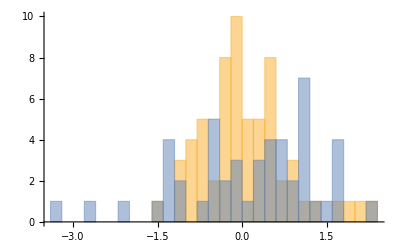

```mathematica
Histogram[rdiscbyclasscentered,20]
```

```mathematica
ribm = Mean[Flatten[rdiscbyclasscentered]]
```

0.0907382

```mathematica
femurmeans = Map[ Mean,fdiscbyclass]
```

{-0.74654,0.994145}

```mathematica
ribmeans = Map[ Mean,rdiscbyclass]
```

{-0.623176,0.994058}

```mathematica
ribsd = StandardDeviation[Flatten[rdiscbyclasscentered]]
```

0.978469

```mathematica
ribdos= (ribmeans[[2]]-ribmeans[[1]])/(ribsd)
```

1.65282

```mathematica
Erfc[(ribmeans[[2]]-ribmeans[[1]])/(Sqrt[2]ribsd)]/2
```

0.0491837

```mathematica
femursd = StandardDeviation[Flatten[fdiscbyclasscentered]]
```

0.944911

```mathematica
femurdos= (femurmeans[[2]]-femurmeans[[1]])/(femursd)
```

1.84217

```mathematica
femurseparatesd = Map[StandardDeviation, fdiscbyclasscentered]
```

{1.05333,0.829476}

```mathematica
eqn3err[dos_]:= 0.5Erfc[dos/Sqrt[2]];
```

```mathematica
eqn7acc[dos_]:= 0.5(2-Erfc[dos/Sqrt[2]]);
```

```mathematica
eqn7acc[femurdos]
```

0.967275

```mathematica
prand[eqn7acc[femurdos]]
```

0.0654508

```mathematica
eqn3err[femurdos]
```

0.0327254

### Kernel Distribution Plots

```mathematica
femurdists = Map[SmoothKernelDistribution,fdiscbyclass];
ribdists = Map[SmoothKernelDistribution,rdiscbyclass];
```

```mathematica
sl = SwatchLegend[Table[Directive[ColorData[97][i],Opacity[0.6]],{i,1,2}],{"F0D0","F0D2"},LabelStyle->Directive[10,Black,"Arial",Bold,Italic],LegendMarkerSize->11]
```

```mathematica
discrimplot1 = Plot[Evaluate[Map[PDF[#,x]&,femurdists]],{x,-4,4},Filling->Axis,Frame->True,Axes->False,Exclusions->None,(*GridLines-> {fres[[7]],None},*)AspectRatio->1,FrameStyle->Directive[10,Black,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},FrameLabel->{"Discriminant","ProbabilityDensity"},PlotRangePadding-> {{Scaled[0.03],Scaled[0.03]},{0,Scaled[0.03]}},Epilog->{Text[Style["pFDA Discriminants",10],Scaled[{0.03,0.97}],{-1,1},Background->White],
Text[Style["Femur ds1",10,"Arial"],Scaled[{0.03,0.9}],{-1,1},Background->White],
Inset[sl,Scaled[{0.03,0.8}],{Left,Top}]},ImageSize->mswordsize/2];
```

```mathematica
discrimplot2 =Plot[Evaluate[Map[PDF[#,x]&,ribdists]],{x,-4,4},Filling->Axis,Frame->True,Axes->False,Exclusions->None,(*GridLines-> {rres[[7]],None},*)AspectRatio->1,FrameStyle->Directive[10,Black,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},FrameLabel->{"Discriminant","ProbabilityDensity"},PlotRangePadding-> {{Scaled[0.03],Scaled[0.03]},{0,Scaled[0.03]}},Epilog->{Text[Style["pFDA Discriminants",10,"Arial"],Scaled[{0.97,0.97}],{1,1},Background->White],
Text[Style["Rib ds2",10,"Arial"],Scaled[{0.97,0.9}],{1,1},Background->White],
Inset[sl,Scaled[{0.97,0.8}],{Right,Top}]},ImageSize->mswordsize/2];
```

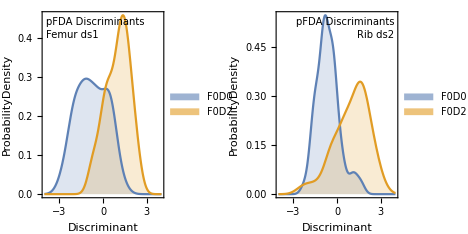

```mathematica
fig14plot = GraphicsGrid[{{discrimplot1,discrimplot2}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
(*Export["fig11plot.jpg",Rasterize[fig11plot,ImageResolution->300],"JPEG","CompressionLevel"->0]*)
```

```mathematica
(*Export["fig11plot.tif",Rasterize[fig11plot,ImageResolution->300],"TIFF"]*)
```

```mathematica
discrimplot3a = Plot[Evaluate[Map[PDF[#,x]&,femurdists]],{x,-4,4},Filling->Axis,Frame->True,Axes->False,Exclusions->None,(*GridLines-> {fres[[7]],None},*)AspectRatio->1,FrameStyle->Directive[10,Black,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"C"]&}},FrameLabel->{"Discriminant","ProbabilityDensity"},PlotRangePadding-> {{Scaled[0.03],Scaled[0.03]},{0,Scaled[0.03]}},Epilog->{Text[Style["pFDA Discriminants",10],Scaled[{0.03,0.97}],{-1,1},Background->White],
Text[Style["Femur ds1",10,"Arial"],Scaled[{0.03,0.9}],{-1,1},Background->White],
Inset[sl,Scaled[{0.03,0.8}],{Left,Top}]},ImageSize->mswordsize/2];
```

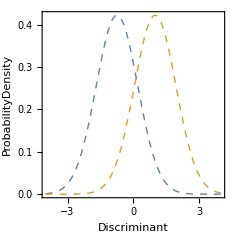

```mathematica
dplot3 = Plot[{PDF[NormalDistribution[femurmeans[[1]],femursd],x],PDF[NormalDistribution[femurmeans[[2]],femursd],x]},{x,-4,4},PlotStyle->Directive[Thick,Dashed],AspectRatio->1,Axes->False,FrameStyle->Directive[10,Black,"Arial"],Frame->True,FrameTicks-> {{Automatic,None},{Automatic,None}},FrameLabel->{"Discriminant","ProbabilityDensity"},PlotRangePadding-> {{Scaled[0.03],Scaled[0.03]},{0,Scaled[0.03]}},ImageSize->mswordsize/2]
```

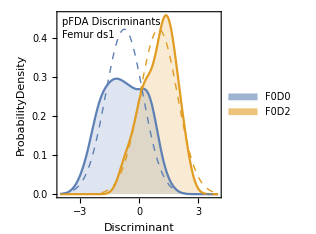

```mathematica
discrimplot3=Show[discrimplot3a,dplot3]
```

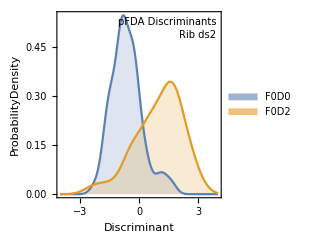

```mathematica
discrimplot4a =Plot[Evaluate[Map[PDF[#,x]&,ribdists]],{x,-4,4},Filling->Axis,Frame->True,Axes->False,Exclusions->None,(*GridLines-> {rres[[7]],None},*)AspectRatio->1,FrameStyle->Directive[10,Black,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"D"]&}},FrameLabel->{"Discriminant","ProbabilityDensity"},PlotRangePadding-> {{Scaled[0.03],Scaled[0.03]},{0,Scaled[0.03]}},Epilog->{Text[Style["pFDA Discriminants",10,"Arial"],Scaled[{0.97,0.97}],{1,1},Background->White],
Text[Style["Rib ds2",10,"Arial"],Scaled[{0.97,0.9}],{1,1},Background->White],
Inset[sl,Scaled[{0.97,0.8}],{Right,Top}]},ImageSize->mswordsize/2]
```

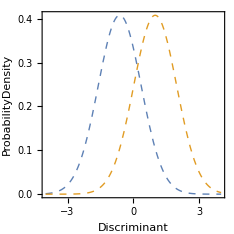

```mathematica
dplot4 = Plot[{PDF[NormalDistribution[ribmeans[[1]],ribsd],x],PDF[NormalDistribution[ribmeans[[2]],ribsd],x]},{x,-4,4},PlotStyle->Directive[Thick,Dashed],AspectRatio->1,Axes->False,FrameStyle->Directive[10,Black,"Arial"],Frame->True,FrameTicks-> {{Automatic,None},{Automatic,None}},FrameLabel->{"Discriminant","ProbabilityDensity"},PlotRangePadding-> {{Scaled[0.03],Scaled[0.03]},{0,Scaled[0.03]}},ImageSize->mswordsize/2]
```

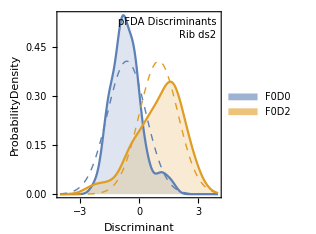

```mathematica
discrimplot4=Show[discrimplot4a,dplot4]
```

```mathematica
(*fig11plotnew = GraphicsGrid[{{discrimplot1,discrimplot2},{discrimplot3,discrimplot4}},Spacings->0,ImageSize->mswordsize]*)
```

```mathematica
discrimplot5=Show[discrimplot1,dplot3,ImageSize->mswordsize/2];
discrimplot6=Show[discrimplot2,dplot4,ImageSize->mswordsize/2];
```

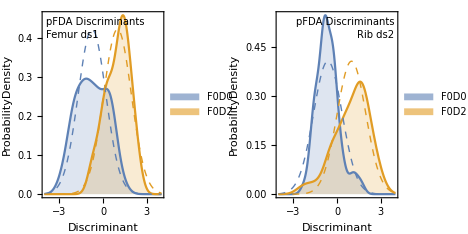

```mathematica
fig14plot = GraphicsGrid[{{discrimplot5,discrimplot6}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
Export["figure14plot.tif",Rasterize[fig14plot,ImageResolution->300],"TIFF"]
```

figure14plot.tif

### Equiprobable discriminant and theoretical confusion matrix

```mathematica
FindRoot[PDF[femurdists[[1]],x] == PDF[femurdists[[2]],x],{x,0}]
```

{x→0.156514}

```mathematica
Mean[femurdists[[1]]]
```

-0.74654

```mathematica
Clear[theoreticalconfusion,prand]
```

```mathematica
prand[a_]:= 2(1-a);
```

```mathematica
theoreticalconfusion[{dist1_,dist2_},{minx_,maxx_}]:=
Module[{equiprob,class1true,class1false,class2true,class2false,cf,acc,pr,means,order,mns,dis1,dis2},
means = Map[Mean,{dist1,dist2}];
order = Ordering[means];
mns = means[[order]];
{dis1,dis2}= {dist1,dist2}[[order]];
equiprob = x/.FindRoot[PDF[dis1,x] == PDF[dis2,x],{x,mns[[1]],mns[[2]]}] ;
class1true = NIntegrate[PDF[dis1,x],{x,minx,equiprob}];
class1false = NIntegrate[PDF[dis2,x],{x,minx,equiprob}];
class2true = NIntegrate[PDF[dis2,x],{x,equiprob,maxx}];
class2false = NIntegrate[PDF[dis1,x],{x,equiprob,maxx}];
cf = {{class1true,class1false},{class2false,class2true}};
acc = accuracy[cf];
pr= prand[acc];
{equiprob,cf,acc,pr}
];
```

```mathematica
theoreticalconfusion[femurdists,{-10,10}]
```

{0.156514,{{0.751901,0.191472},{0.248099,0.808528}},accuracy[{{0.751901,0.191472},{0.248099,0.808528}}],2 (1-accuracy[{{0.751901,0.191472},{0.248099,0.808528}}])}

```mathematica
theoreticalconfusion[ribdists,{-10,10}]
```

{0.19886,{{0.866787,0.249369},{0.133213,0.750631}},accuracy[{{0.866787,0.249369},{0.133213,0.750631}}],2 (1-accuracy[{{0.866787,0.249369},{0.133213,0.750631}}])}

## Table 11

```mathematica
aicc[{n_,k_,ll_}]:= 2k - 2 ll + (2 k*k +2k)/(n - k - 1);
```

### Femur

```mathematica
ffd = Map[FindDistribution[#,3,PerformanceGoal->"Quality"]&,fdiscbyclass]
```

{{UniformDistribution[{-2.79075,1.36502}],NormalDistribution[-0.745417,1.09452],WeibullDistribution[2.81477,3.13253,-3.52991]},{NormalDistribution[0.98883,0.865144],UniformDistribution[{-0.85619,2.52029}],WeibullDistribution[6.0638,4.76879,-3.43045]}}

```mathematica
femursharednormalfits = Table[{Length[fdiscbyclass[[i]]],1.5,LogLikelihood[NormalDistribution[femurmeans[[i]],femursd],fdiscbyclass[[i]]]},{i,1,2}]
```

{{58,1.5,-85.4272},{59,1.5,-73.2214}}

```mathematica
femursharednormalaicc = Map[aicc,femursharednormalfits]
```

{173.99,149.576}

```mathematica
ffdparamcount= {{2,2,3},{2,2,3}};
```

```mathematica
femuraicinputlist = Table[{Length[fdiscbyclass[[i]]],ffdparamcount[[i,j]],LogLikelihood[ffd[[i,j]],fdiscbyclass[[i]]]},{j,1,3},{i,1,2}]
```

{{{58,2,-82.6209},{59,2,-72.3299}},{{58,2,-84.932},{59,2,-71.7933}},{{58,3,-83.9879},{59,3,-70.9981}}}

```mathematica
femurdeltaaicc = Map[#-Min[#]&,Transpose[Join[{femursharednormalaicc},Map[aicc,femuraicinputlist,{2}]]]]
```

{{4.52956,0.,4.6223,4.96032},{1.77476,1.07322,0.,0.631711}}

```mathematica
femurweights = Map[Exp[-#/2]&,femurdeltaaicc,{2}]
```

{{0.103853,1.,0.0991472,0.08373},{0.411733,0.584727,1.,0.729165}}

```mathematica
femurwprobs = Map[#/Total[#]&,femurweights]
```

{{0.0807106,0.777164,0.0770536,0.0650719},{0.15106,0.214529,0.366888,0.267522}}

```mathematica
Transpose[Join[{{"pFDA normal","Uniform","Best fit normal","Weibull"},femurdeltaaicc[[1]],femurweights[[1]],femurwprobs[[1]]}]]//TableForm
```

pFDA normal | 4.52956 | 0.103853 | 0.0807106
Uniform | 0. | 1. | 0.777164
Best fit normal | 4.6223 | 0.0991472 | 0.0770536
Weibull | 4.96032 | 0.08373 | 0.0650719

```mathematica
Transpose[Join[{{"pFDA normal","Best fit normal","Uniform","Weibull"},femurdeltaaicc[[2]],femurweights[[2]],femurwprobs[[2]]}]]//TableForm
```

pFDA normal | 1.77476 | 0.411733 | 0.15106
Best fit normal | 1.07322 | 0.584727 | 0.214529
Uniform | 0. | 1. | 0.366888
Weibull | 0.631711 | 0.729165 | 0.267522

### Rib

```mathematica
rfd= Map[FindDistribution[#,3,PerformanceGoal->"Quality"]&,rdiscbyclass]
```

{{NormalDistribution[-0.612085,0.840423],MixtureDistribution[{0.929453,0.0705474},{NormalDistribution[-0.764716,0.650705],NormalDistribution[1.39881,0.287749]}],MixtureDistribution[{0.626313,0.373687},{NormalDistribution[-0.806336,0.507906],UniformDistribution[{-2.22421,1.68769}]}]},{NormalDistribution[0.968889,1.28094],WeibullDistribution[24.7765,26.0346,-24.4948],MixtureDistribution[{0.413881,0.586119},{NormalDistribution[0.0107169,1.26865],NormalDistribution[1.64549,0.746214]}]}}

```mathematica
rfdparamcount = {{2,5,5},{2,3,5}}
```

{{2,5,5},{2,3,5}}

```mathematica
ribaicinputlist = Table[{Length[rdiscbyclass[[i]]],rfdparamcount[[i,j]],LogLikelihood[rfd[[i,j]],rdiscbyclass[[i]]]},{j,1,3},{i,1,2}]
```

{{{62,2,-72.6116},{49,2,-77.8668}},{{62,5,-68.6974},{49,3,-75.1836}},{{62,5,-68.0131},{49,5,-75.3193}}}

```mathematica
ribsharednormalfits = Table[{Length[rdiscbyclass[[i]]],1.5,LogLikelihood[NormalDistribution[ribmeans[[i]],ribsd],rdiscbyclass[[i]]]},{i,1,2}]
```

{{62,1.5,-75.1089},{49,1.5,-79.4327}}

```mathematica
ribsharednormalaicc = Map[aicc,ribsharednormalfits]
```

{153.344,162.027}

```mathematica
ribdeltaaicc = Map[#-Min[#]&,Transpose[Join[{ribsharednormalaicc},Map[aicc,ribaicinputlist,{2}]]]]
```

{{6.24624,2.32911,1.36869,0.},{5.12617,3.094,0.,5.13354}}

```mathematica
ribweights = Map[Exp[-#/2]&,ribdeltaaicc,{2}]
```

{{0.0440197,0.312062,0.504419,1.},{0.0770664,0.212885,1.,0.0767832}}

```mathematica
ribwprobs = Map[#/Total[#]&,ribweights]
```

{{0.0236601,0.16773,0.27112,0.53749},{0.0563873,0.155762,0.731671,0.05618}}

```mathematica
Transpose[Join[{{"pFDA normal","Best fit normal","Mixture normal,normal","Mixture normal,uniform"},ribdeltaaicc[[1]],ribweights[[1]],ribwprobs[[1]]}]]//TableForm
```

pFDA normal | 6.24624 | 0.0440197 | 0.0236601
Best fit normal | 2.32911 | 0.312062 | 0.16773
Mixture normal,normal | 1.36869 | 0.504419 | 0.27112
Mixture normal,uniform | 0. | 1. | 0.53749

```mathematica
Transpose[Join[{{"pFDA normal","Best fit normal","Weibull","Mixture normal,normal"},ribdeltaaicc[[2]],ribweights[[2]],ribwprobs[[2]]}]]//TableForm
```

pFDA normal | 5.12617 | 0.0770664 | 0.0563873
Best fit normal | 3.094 | 0.212885 | 0.155762
Weibull | 0. | 1. | 0.731671
Mixture normal,normal | 5.13354 | 0.0767832 | 0.05618

#### Check rib uniform

```mathematica
ribunifdists = UniformDistribution[{mn,mx}]/.Map[FindDistributionParameters[#,UniformDistribution[{mn,mx}]]&,rdiscbyclass]
```

{UniformDistribution[{-2.22421,1.68769}],UniformDistribution[{-2.38353,3.08802}]}

```mathematica
ribunifaiccinput = Table[{Length[rdiscbyclass[[i]]],2,LogLikelihood[ribunifdists[[i]],rdiscbyclass[[i]]]},{i,1,2}]
```

{{62,2,-84.5694},{49,2,-83.2785}}

```mathematica
ribdeltaaicc = Map[#-Min[#]&,Transpose[Join[{ribsharednormalaicc},Map[aicc,ribaicinputlist,{2}],{Map[aicc,ribunifaiccinput]}]]]
```

{{6.24624,2.32911,1.36869,0.,26.2447},{5.12617,3.094,0.,5.13354,13.9173}}

## Fig 15 - Histogram and PDF Plots

#### Femur

```mathematica
ffd = Map[FindDistribution[#,3,PerformanceGoal->"Quality"]&,fdiscbyclass]
```

{{UniformDistribution[{-2.79075,1.36502}],NormalDistribution[-0.745417,1.09452],WeibullDistribution[2.81477,3.13253,-3.52991]},{NormalDistribution[0.98883,0.865144],UniformDistribution[{-0.85619,2.52029}],WeibullDistribution[6.0638,4.76879,-3.43045]}}

```mathematica
fhds = Map[HistogramDistribution[#,{0.4}]&,fdiscbyclass]
```

{DataDistribution[…],DataDistribution[…]}

```mathematica
fdistnames1 = {"Histogram","Uniform","Normal","Weibull"};
```

```mathematica
fdistlegend1 = LineLegend[{ColorData[110][1],Black,Red,Blue},fdistnames1,LabelStyle->Directive[Black,10,"Arial"],LegendMargins->0,LegendMarkerSize->10]
```

```mathematica
fdistnames2= {"Histogram","Normal","Uniform","Weibull"};
```

```mathematica
fdistlegend2 = LineLegend[{ColorData[110][1],Black,Red,Blue},fdistnames2,LabelStyle->Directive[Black,10,"Arial"],LegendMargins->0,LegendMarkerSize->10]
```

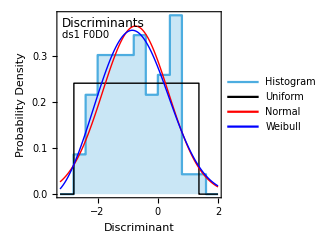

```mathematica
femurdiscplot1 =Plot[{PDF[fhds[[1]],x],PDF[ffd[[1,1]],x],PDF[ffd[[1,2]],x],PDF[ffd[[1,3]],x]},{x,-3.25,2},
PlotRange->All,
(*PlotRangePadding-> {{Scaled[0.05],Scaled[0.03]},{0,Scaled[0.09]}},*)PlotStyle->{Directive[ColorData[110][1]],Sequence@@Table[Directive[{Null,Black,Red,Blue}[[i]],Thick],{i,2,4}]},
PlotPoints->100,
PlotRangePadding-> {Scaled[0.03],{0,Scaled[0.05]}},
Filling->1->{Axis,Directive[Opacity[0.3],ColorData[110][1]]},
Exclusions->None,
Axes->False,
Frame->True,
FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},
FrameStyle->Directive[Black,10,"Arial"],
FrameLabel->{"Discriminant","Probability Density"}, Epilog-> {Text[Style["Discriminants",12,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["ds1 F0D0",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}],Inset[fdistlegend1,Scaled[{0.5,0.03}],{Center,Bottom}]},
AspectRatio->1,ImageSize->mswordsize/2]
```

```mathematica
femurdiscplot2 =Plot[{PDF[fhds[[2]],x],PDF[ffd[[2,1]],x],PDF[ffd[[2,2]],x],PDF[ffd[[2,3]],x]},{x,-1.5,3},PlotRange->All,PlotRangePadding-> {Scaled[0.03],{0,Scaled[0.05]}},PlotStyle->{Directive[ColorData[110][1]],Sequence@@Table[Directive[{Null,Black,Red,Blue}[[i]],Thick],{i,2,4}]},PlotPoints->100,Filling->1->{Axis,Directive[Opacity[0.3],ColorData[110][1]]},Exclusions->None,Frame->True,Axes->False,AspectRatio->1,FrameStyle->Directive[Black,10],FrameLabel->{"Discriminant","Probability Density"},
FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},Epilog-> {Text[Style["Discriminants",12,"Arial"],Scaled[{0.03,0.97}],{-1,1}],
Text[Style["ds1 F0D2",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}],Inset[fdistlegend2,Scaled[{0.6,0.02}],{Center,Bottom}]},ImageSize->mswordsize/2];
```

#### Rib

```mathematica
rdistnames1 = {"Histogram","Normal","Mix: N, N","Mix: N, U"};
```

```mathematica
rdistlegend1 = LineLegend[{ColorData[110][1],Black,Red,Blue},rdistnames1,LabelStyle->Directive[Black,10,"Arial"],LegendMarkerSize->10,LegendMargins->0]
```

```mathematica
rdistnames2 = {"Histogram","Normal","Weibull","Mix: N, N"};
```

```mathematica
rdistlegend2 = LineLegend[{ColorData[110][1],Black,Red,Blue},rdistnames2,LabelStyle->Directive[Black,10],LegendMarkerSize->10,LegendMargins->0]
```

```mathematica
rfd = Map[FindDistribution[#,3,PerformanceGoal->"Quality"]&,rdiscbyclass]
```

{{NormalDistribution[-0.612085,0.840423],MixtureDistribution[{0.929453,0.0705474},{NormalDistribution[-0.764716,0.650705],NormalDistribution[1.39881,0.287749]}],MixtureDistribution[{0.626313,0.373687},{NormalDistribution[-0.806336,0.507906],UniformDistribution[{-2.22421,1.68769}]}]},{NormalDistribution[0.968889,1.28094],WeibullDistribution[24.7765,26.0346,-24.4948],MixtureDistribution[{0.413881,0.586119},{NormalDistribution[0.0107169,1.26865],NormalDistribution[1.64549,0.746214]}]}}

```mathematica
rhds = Map[HistogramDistribution[#,{0.4}]&,rdiscbyclass]
```

{DataDistribution[…],DataDistribution[…]}

```mathematica
ribdiscplot1 =Plot[{PDF[rhds[[1]],x],PDF[rfd[[1,1]],x],PDF[rfd[[1,2]],x],PDF[rfd[[1,3]],x]},{x,-3,2.5},PlotRange->All,
PlotRangePadding-> {Scaled[0.03],{0,Scaled[0.09]}},
PlotStyle->{Directive[ColorData[110][1]],Sequence@@Table[Directive[{Null,Black,Red,Blue}[[i]],Thick],{i,2,4}]},PlotPoints->100,Filling->1->{Axis,Directive[Opacity[0.3],ColorData[110][1]]},Exclusions->None,Frame->True,Axes->False,AspectRatio->1,FrameStyle->Directive[Black,10,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"C"]&}},FrameLabel->{"Discriminant","Probability Density"},Epilog-> {Text[Style["Discriminants",12,"Arial"],Scaled[{0.97,0.97}],{1,1}],
Text[Style["ds2 F0D0",10,"Arial"],Scaled[{0.97,0.90}],{1,1}],Inset[rdistlegend1,Scaled[{0.97,0.8}],{Right,Top}]},ImageSize->mswordsize/2];
```

```mathematica
ribdiscplot2 = Plot[{PDF[rhds[[2]],x],PDF[rfd[[2,1]],x],PDF[rfd[[2,2]],x],PDF[rfd[[2,3]],x]},{x,-3,4},PlotRange->All,
PlotRangePadding-> {Scaled[0.03],{0,Scaled[0.05]}},PlotStyle->{Directive[ColorData[110][1]],Sequence@@Table[Directive[{Null,Black,Red,Blue}[[i]],Thick],{i,2,4}]},PlotPoints->100,Filling->1->{Axis,Directive[Opacity[0.5],ColorData[110][1]]},Exclusions->None,Frame->True,Axes->False,AspectRatio->1,FrameStyle->Directive[Black,10,"Arial"],FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"D"]&}},FrameLabel->{"Discriminant","Probability Density"},Epilog-> {Text[Style["Discriminants",12,"Arial"],Scaled[{0.03,0.97}],{-1,1}],
Text[Style["ds2 F0D2",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}],Inset[rdistlegend2,Scaled[{0.03,0.8}],{Left,Top}]},ImageSize->mswordsize/2];
```

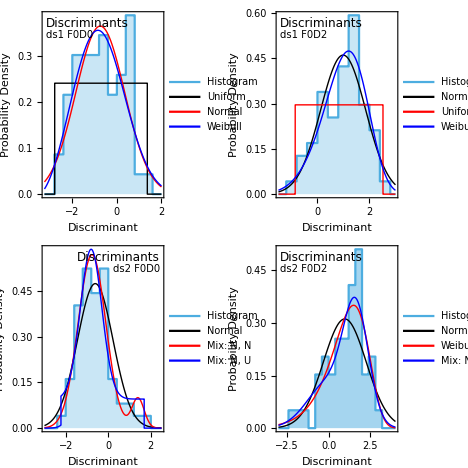

```mathematica
fig15plot = GraphicsGrid[{{femurdiscplot1,femurdiscplot2},{ribdiscplot1,ribdiscplot2}},Spacings->0,ImageSize-> mswordsize]
```

```mathematica
Export["figure15plot.tif",Rasterize[fig15plot,ImageResolution->300],"TIFF"]
```

figure15plot.tif

## Fig S9, S10 - Quantile plots

```mathematica
(*qcolor = Directive[Black,PointSize[.02]];*)
```

#### Femur

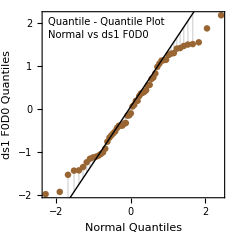

```mathematica
qqfplot1 = QuantilePlot[fdiscbyclasscentered[[1]],AspectRatio->1,PlotRange->All,
Filling->Automatic,
PlotStyle->{PointSize[.02],Brown},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],PlotRangePadding->Scaled[0.05],
Frame->True,FrameStyle->Directive[Black,10,"Arial"],
FrameLabel->{"Normal Quantiles","ds1 F0D0 Quantiles"}, 
FrameStyle->Directive[10,"Arial",Black],
FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},
Epilog-> {Text[Style["Quantile - Quantile Plot",10,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["Normal vs ds1 F0D0",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}]},ImageSize->mswordsize/2]
```

```mathematica
qqfplot2 =QuantilePlot[fdiscbyclasscentered[[1]],UniformDistribution[],AspectRatio->1,
FrameStyle->Directive[Black,10,"Arial"],Filling->Automatic,
PlotStyle->{PointSize[.02],Brown},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],PlotRange->All,PlotRangePadding->Scaled[0.05],
FrameLabel->{"Uniform Quantiles","ds1 F0D0 Quantiles"},
FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},Epilog-> {Text[Style["Quantile - Quantile Plot",10,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["Uniform vs ds1 F0D0",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}]},ImageSize->mswordsize/2];
```

```mathematica
qqfplot3 =QuantilePlot[fdiscbyclasscentered[[2]],
Frame->True,
FrameStyle->Directive[Black,10,"Arial"],
FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},
AspectRatio->1,PlotRange->All,Filling->Automatic,PlotStyle->{PointSize[.02],Blue},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],PlotRangePadding->Scaled[0.05],FrameLabel->{"Normal Quantiles","ds1 F0D2 Quantiles"},Epilog-> {Text[Style["Quantile - Quantile Plot",10,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["Normal vs ds1 F0D2",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}]},ImageSize->mswordsize/2];
```

```mathematica
qqfplot4 =QuantilePlot[fdiscbyclasscentered[[2]],UniformDistribution[],AspectRatio->1,
FrameStyle->Directive[Black,10,"Arial"],Filling->Automatic,PlotStyle->{PointSize[.02],Blue},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],PlotRange->All,PlotRangePadding->Scaled[0.05],FrameLabel->{"Uniform Quantiles","ds1 F0D2 Quantiles"},
FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"D"]&}},Epilog-> {Text[Style["Quantile - Quantile Plot",10,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["Uniform vs ds1 F0D2",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}]},ImageSize->mswordsize/2];
```

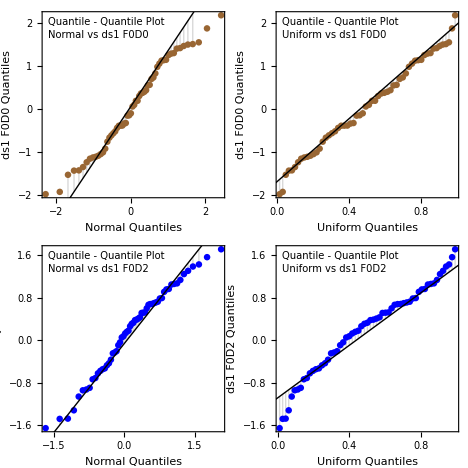

```mathematica
figS9plot = GraphicsGrid[{{qqfplot1,qqfplot2},{qqfplot3,qqfplot4}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
Export["figureS9plot.tif",Rasterize[figS9plot,ImageResolution->300],"TIFF"]
```

figureS9plot.tif

#### Rib

```mathematica
qqrplot1=QuantilePlot[rdiscbyclasscentered[[1]],Filling->Automatic,
PlotStyle->{PointSize[.02],Brown},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],
FrameStyle->Directive[Black,10,"Arial"],
PlotRange->All,PlotRangePadding->Scaled[0.05],
FrameLabel->{"Normal Quantiles","ds2 F0D0 Quantiles"},
FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},Epilog-> {Text[Style["Quantile - Quantile Plot",10,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["Normal vs ds2 F0D0",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}]},AspectRatio->1,ImageSize->mswordsize/2];
```

```mathematica
qqrplot2=QuantilePlot[rdiscbyclasscentered[[1]],MixtureDistribution[{0.929452612854827,0.07054738714517284},{NormalDistribution[-0.7647155125750392,0.6507048470924716],NormalDistribution[1.3988072381060477,0.287748765736466]}],FrameStyle->Directive[Black,10,"Arial"],PlotRange->All,PlotRangePadding->Scaled[0.05],Filling->Automatic,PlotStyle->{PointSize[.02],Brown},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],FrameLabel->{"Mixture of 2 Normal Quantiles","ds2 F0D0 Quantiles"},FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},Epilog-> {Text[Style["Quantile - Quantile Plot",10,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["Mixture 2 Normal vs ds2 F0D0",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}]},AspectRatio->1,ImageSize->mswordsize/2];
```

```mathematica
qqrplot3=QuantilePlot[rdiscbyclasscentered[[2]],Filling->Automatic,PlotStyle->{PointSize[.02],Brown},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],PlotRange->All,PlotRangePadding->Scaled[0.05],FrameLabel->{"Normal Quantiles","ds2 F0D0 Quantiles"},FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"C"]&}},Epilog-> {Text[Style["Quantile - Quantile Plot",10,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["Normal vs ds2 F0D2",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}]},AspectRatio->1,FrameStyle->Directive[Black,12],ImageSize->mswordsize/2];
```

```mathematica
qqrplot4=QuantilePlot[rdiscbyclasscentered[[1]],WeibullDistribution[24.776469646630318,26.03462708919198,-24.49479209854443],AspectRatio->1,PlotStyle->{PointSize[.02],Blue},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],FrameStyle->Directive[Black,10,"Arial"],PlotRange->All,PlotRangePadding->Scaled[0.05],Filling->Automatic,PlotStyle->{PointSize[.02],Blue},ReferenceLineStyle->Directive[Dotted,Gray],FillingStyle->Directive[Gray],FrameLabel->{"Weibull Distribution Quantiles","ds2 F0D2 Quantiles"},FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"D"]&}},Epilog-> {Text[Style["Quantile - Quantile Plot",10,"Arial"],Scaled[{0.03,0.97}],{-1,1}],Text[Style["Weibull vs ds2 F0D2",10,"Arial"],Scaled[{0.03,0.90}],{-1,1}]},ImageSize->mswordsize/2];
```

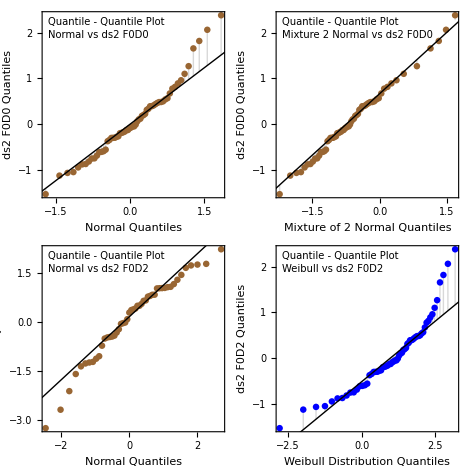

```mathematica
figS10plot = GraphicsGrid[{{qqrplot1,qqrplot2},{qqrplot3,qqrplot4}},Spacings->0,ImageSize-> mswordsize]
```

```mathematica
Export["figureS10plot.tif",Rasterize[figS10plot,ImageResolution->300],"TIFF"]
```

figureS10plot.tif

## Fig 16 - random points vs Femur F0D0

```mathematica
makechrands[ptlist_]:=
Module[{npts,reg},
npts = Length[ptlist];
reg = ConvexHullRegion[ptlist];
RandomPoint[reg,npts]
];
```

```mathematica
closedline[pts_]:= Line[Join[pts,{pts[[1]]}]];
```

```mathematica
chrandpts =makechrands[femurlfpts[[5]]];
```

```mathematica
rng = Map[MinMax,Transpose[Flatten[{femurlfpts[[5]],chrandpts},1]]]//N
```

{{-0.0822952,5.14749},{0.353,0.855}}

```mathematica
swl = SwatchLegend[{Black,Red},{"F0D0","Uniform"},LegendMarkers-> "Bubble",LabelStyle->Directive[Black,10,"Arial"],LegendMarkerSize->6,LegendMargins->0,LegendFunction->Framed]
```

```mathematica
plot12= ListPlot[{femurlfpts[[5]],chrandpts},PlotStyle->Map[Directive[PointSize[.015],Opacity[.7],#]&,{Black,Red}],PlotRange-> rng,PlotRangePadding-> Scaled[0.04],Frame-> True,FrameTicks-> {{Automatic,None},{logticks,topticklabel[#1,#2,"A"]&}},FrameLabel-> {{"Cg",None},{"Femoral MD(mm)",None}},FrameStyle-> Directive[10,Black,"Arial"],AspectRatio->1,Prolog->{LightGray,closedline[MeshCoordinates[ConvexHullRegion[femurlfpts[[5]]]]]}, Epilog-> {Inset[swl,Scaled[{0.97,0.03}],{Right,Bottom},Background->White]},ImageSize->mswordsize/2];
```

```mathematica
plot1 = ListPlot[femurlfpts[[5]],PlotStyle->Directive[PointSize[.015],Opacity[.7],Black],PlotRange->rng,PlotRangePadding-> Scaled[0.04],Axes-> False,Frame-> True,FrameTicks-> {{Automatic,None},{logticks,topticklabel[#1,#2,"A"]&}},FrameLabel-> {{"Cg",None},{"Femoral MD(mm)",None}},FrameStyle-> Directive[10,Black,"Arial"],AspectRatio->1,Prolog->{LightGray,closedline[MeshCoordinates[ConvexHullRegion[femurlfpts[[5]]]]]},Epilog->Text[Style["F0D0",10,Bold,Italic],Scaled[{0.97,0.03}],{1,-1}],ImageSize->mswordsize/2];
```

```mathematica
plot2 = ListPlot[chrandpts,PlotStyle->Directive[PointSize[.015],Red],PlotRange-> rng,PlotRangePadding-> Scaled[0.04],Frame-> True,FrameTicks-> {{Automatic,None},{logticks,topticklabel[#1,#2,"B"]&}},FrameLabel-> {{"Cg",None},{"Femoral MD(mm)",None}},FrameStyle-> Directive[10,Black,"Arial"],AspectRatio->1,Prolog->{LightGray,closedline[MeshCoordinates[ConvexHullRegion[femurlfpts[[5]]]]]},Epilog-> Text[Style["Uniform Random",10],Scaled[{0.97,0.03}],{1,-1}],ImageSize->mswordsize/2];
```

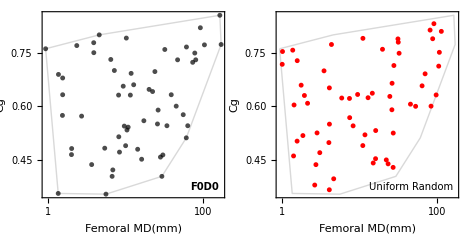

```mathematica
fig16plot = GraphicsGrid[{{plot1,plot2}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
(*Export["fig14plot.jpg",fig14plot,"JPEG","CompressionLevel"->0]*)
```

```mathematica
Export["figure16plot.tif",Rasterize[fig16plot,ImageResolution->300],"TIFF"]
```

figure16plot.tif

## Fig S1 - Nothosaurus Femur plots

```mathematica
nothos = Cases[SortBy[femurbyfd[[2]],#[[4,2]]&],{taxon_String,_,_,_}/;StringTake[taxon,4]== "Noth"]
```

{{Nothosaurus_giganteus,0,2,{26.819,0.738}},{Nothosaurus_mirabilis_1,0,2,{21.7,0.776}},{Nothosaurus_mirabilis,0,2,{16.09,0.828}},{Nothosaurus_568,0,2,{5.464,0.909}},{Nothosaurus_150,0,2,{8.125,0.938}},{Nothosaurus_102,0,2,{5.168,0.955}}}

```mathematica
sims = Cases[SortBy[femurbyfd[[2]],#[[4,2]]&],{taxon_String,_,_,_}/;StringTake[taxon,4]== "Simo"]
```

{{Simosaurus_1,0,2,{22.9,0.764}},{Simosaurus,0,2,{22.97,0.865}}}

```mathematica
serps = Cases[SortBy[femurbyfd[[2]],#[[4,2]]&],{taxon_String,_,_,_}/;StringTake[taxon,4]== "Serp"]
```

{{Serpianosaurus,0,2,{4.8,0.989}}}

```mathematica
lfnotho = LinearModelFit[nothos[[All,-1]],x,x]
```

FittedModel[0.991632-0.0096657 x]

```mathematica
lfnotho2 = LinearModelFit[Join[nothos[[All,-1]],sims[[All,-1]],serps[[All,-1]]],x,x]
```

FittedModel[1.00002-0.00923768 x]

```mathematica
lfnotho["RSquared"]
```

0.955025

```mathematica
lfnotho2["RSquared"]
```

0.837235

```mathematica
Solve[lfnotho2[x]==0,x]
```

{{x→108.254}}

```mathematica
nothos[[All,1]]
```

{Nothosaurus_giganteus,Nothosaurus_mirabilis_1,Nothosaurus_mirabilis,Nothosaurus_568,Nothosaurus_150,Nothosaurus_102}

```mathematica
nothonames = {"giganteus","mirabilis_1","mirabilis","568","150","102"};
```

```mathematica
addfactor = 0.5*{-1,-1,-1,-1,1,1};
textdir = {1,1,1,1,-1,-1};
```

```mathematica
Cg == lfnotho[MD]
```

Cg==0.991632-0.0096657 MD

```mathematica
eqn1string = "Cg = 0.992-0.00967 MD";
```

```mathematica
(*nothosaurusplot1= Plot[lfnotho[x],{x,3,30},PlotStyle->Blue,Epilog->{Text[Style["Nothosaurus Femoral C_g vs MD",18,Black],Scaled[{0.97,0.97}],{1,1}],
Text[Style[eqn1string,14,Blue,Italic],Scaled[{0.55,0.8}],{-1,1}],
Text[Style["R^2 = 0.96",14,Blue,Italic],Scaled[{0.55,0.75}],{-1,1}],
 {Blue,PointSize[.02],Map[Point,nothos[[All,-1]]]},MapThread[Text[Style[#1,12,Italic,Blue],#2+{#3,0},{#4,1}]&,{nothonames,nothos[[All,-1]],addfactor,textdir}]},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},FrameLabel->{"Femoral MD (mm)","C_g"},FrameStyle-> Directive[10,Black],AspectRatio-> 1,ImageSize->mswordsize]*)
```

```mathematica
(*Export["nothosaurusplot.tif",nothosaurusplot, "TIFF",ImageResolution-> 300]*)
```

```mathematica
(*Export["nothosaurusplot.eps",nothosaurusplot, "eps"]*)
```

```mathematica
plegend = PointLegend[{Blue,Darker[Green],Red},{"Nothosaurus","Serpicosaurus","Simosaurus"},LabelStyle->Directive[14,Italic],LegendMarkerSize->14,LegendMargins->0]
```

```mathematica
Solve[lfnotho[MD]==0,MD]
```

{{MD→102.593}}

```mathematica
Solve[lfnotho2[MD]==0,MD]
```

{{MD→108.254}}

```mathematica
Cg ==lfnotho2[MD]
```

Cg==1.00002-0.00923768 MD

```mathematica
eqn2string = "Cg = 1.000 - 0.00924 MD";
```

```mathematica
(*nothosaurusplot2= Plot[{lfnotho2[x],lfnotho[x]},{x,3,30},PlotStyle->{Black,Blue},
PlotRange-> {All,{0.7,1}},
Epilog->{Text[Style["Nothosaur Femoral C_g",18,Black],Scaled[{0.97,0.97}],{1,1}],
Text[Style[eqn2string,14,Black,Italic],Scaled[{0.55,0.8}],{-1,1}],
Text[Style["R^2 = 0.84",14,Black,Italic],Scaled[{0.55,0.75}],{-1,1}],
 {Blue,PointSize[.02],Map[Point,nothos[[All,-1]]]},{Red,PointSize[.02],Map[Point,sims[[All,-1]]]},{Darker[Green],PointSize[.02],Map[Point,serps[[All,-1]]]},
Text[Style["mirigolensis",12,Italic,Darker[Green]],serps[[1,-1]]+{1,0},{-1,1}],
Text[Style["gallardoti_1",12,Italic,Red ],sims[[1,-1]]+{-.5,-.005},{1,1}],
Text[Style["gallardoti",12,Italic,Red ],sims[[2,-1]]+{-.5,-.005},{1,1}],
MapThread[Text[Style[#1,12,Italic,Blue],#2+{#3,0},{#4,1}]&,{nothonames,nothos[[All,-1]],addfactor,textdir}],
Inset[plegend,Scaled[{0.03,0.03}],{Left,Bottom}]

},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},FrameLabel->{"Femoral MD(mm)","C_g"},FrameStyle-> Directive[10,Black,"Arial"],AspectRatio-> 1,ImageSize->mswordsize]*)
```

```mathematica
linetable = Grid[{{Style["Nothosaurus",14,Blue,Italic,"Arial"],Style[eqn1string,14,Black,Italic]},{SpanFromAbove,Style["R^2 = 0.96",14,Black,Italic]},{Style["All taxa","Arial",14,Black],Style[eqn2string,"Arial",14,Black,Italic]},{SpanFromAbove,Style["R^2 = 0.84","Arial",14,Italic]}},Alignment->Left,Dividers->{{2->Black},{3->Black}}]
```

Nothosaurus | Cg = 0.992-0.00967 MD
 | R^2 = 0.96
All taxa | Cg = 1.000 - 0.00924 MD
 | R^2 = 0.84

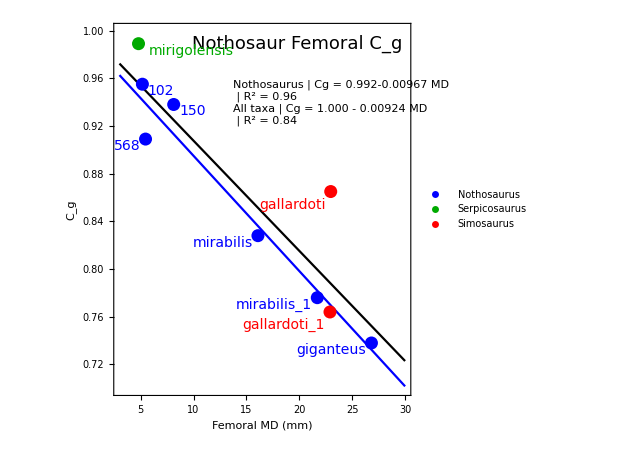

```mathematica
nothosaurusplot12= Plot[{lfnotho2[x],lfnotho[x]},{x,3,30},PlotStyle->{Black,Blue},
PlotRange-> {All,{0.7,1}},
Epilog->{Text[Style["Nothosaur Femoral C_g",18,Black],Scaled[{0.97,0.97}],{1,1}],
Inset[linetable,Scaled[{0.4,0.85}],{Left,Top}],
 {Blue,PointSize[.02],Map[Point,nothos[[All,-1]]]},{Red,PointSize[.02],Map[Point,sims[[All,-1]]]},{Darker[Green],PointSize[.02],Map[Point,serps[[All,-1]]]},
Text[Style["mirigolensis",14,Italic,Darker[Green]],serps[[1,-1]]+{1,0},{-1,1}],
Text[Style["gallardoti_1",14,Italic,Red ],sims[[1,-1]]+{-.5,-.005},{1,1}],
Text[Style["gallardoti",14,Italic,Red ],sims[[2,-1]]+{-.5,-.005},{1,1}],
MapThread[Text[Style[#1,14,Italic,Blue],#2+{#3,0},{#4,1}]&,{nothonames,nothos[[All,-1]],addfactor,textdir}],
Inset[plegend,Scaled[{0.03,0.03}],{Left,Bottom}]

},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},FrameLabel->{"Femoral MD (mm)","C_g"},FrameStyle-> Directive[10,Black,"Arial"],AspectRatio-> 1,ImageSize->mswordsize]
```

```mathematica
(*figS1plot = GraphicsGrid[{{nothosaurusplot1},{nothosaurusplot2}},Spacings->0,ImageSize->mswordsize]*)
```

```mathematica
Export["figureS1plot.tif",Rasterize[nothosaurusplot12,ImageResolution->300],"TIFF"]
```

figureS1plot.tif

## Fig S11 - NHANES human body mass

### Data

```mathematica
adultmalemass = {129.2,119.9,118.6,114.2,110.9,109.5,108.7,108.3,107.8,103.8,103.8,102.3,101.2,101.2,101.2,98.1,97.9,97.8,97.8,97.8,97.6,97.2,96.9,96.4,95.4,94.6,93.5,93,92.5,92.2,91.7,91.7,90.8,90.5,90.2,90,89.8,89.2,89.1,89.1,88.3,88.3,87.8,87.7,87.7,86.9,86.5,86.4,86.2,86.1,85.7,85.6,85.5,85,84.7,84.4,84,84,83.5,83.4,83.3,83.1,82.6,82.4,82.3,82.2,81.4,81.3,81.3,81.3,81.3,81.1,80.7,80.4,79.8,79.6,79.1,78.9,78.7,78.3,78.2,77.8,77.7,76.9,76.7,76.3,75.8,75.6,75.3,75,74.8,74.6,74.3,74.3,74.2,74.1,73.7,73.4,73.3,73.2,73.2,72.9,72.9,72.5,72.5,71.7,71.5,71.3,70.5,70.5,70.3,70.2,69.7,69.3,69.3,69.2,69.2,69,68.7,68.6,68.2,68.2,68,67.3,66.9,66.7,66.5,66.4,66,65.9,65.4,65.3,65.3,65.2,64.7,64.5,64.5,63.5,63.3,62.9,62.1,61.9,61,60.4,59.6,59.1,59,58.7,57.6,57.5,55.8,55.6,55.3,53,52.8,51.8,51.3,49.3,48.2,43.7,103.8,86.2,85.9,85.4,80.6,80.5,80.1,77.4,74.7,70.3,68.6,64.4,62.6,48,116.7,116.5,107.1,91.9,90.6,85.5,85.1,84.8,83.4,81.8,80,79.7,78.6,72.6,72.4,71.9,70.7,69.6,62.2,58.7,57.9,54.5,129.7,110.6,110.3,108.4,104.2,104.2,92.6,90.3,89.7,83.9,81.7,74.3,73.1,72,70.4,69.7,68.5,67.7,66.7,65.7,56.4,112.7,105.5,104.1,100.7,98.7,98.1,97.6,96.7,96.1,94.5,94.1,93.6,93.1,84.4,83.1,78.6,77.6,76.8,71.9,69,66.5,64.5,62.8,62,61.8,58.4,55.4,114,100.5,98,97.1,96.6,93.2,92.3,89.8,82.4,81.1,79.6,78.3,77.2,75.8,75.8,75.8,75.6,74.2,73.9,70.2,69.2,66.1,65.9,63.9,60.6,57.1,120.5,107.6,99.1,97.9,94.3,93,92.2,91.3,89.1,88.8,88.4,88,84.2,84.1,84.1,83.4,82.7,79.7,75.3,73.1,72.7,72.5,64.1,60,58.9,58.6,57.1,136.9,110.9,108.6,98.8,93.6,89.3,84.9,84.8,84.5,79.4,78.4,78.1,77.4,77,76.1,75,73.3,72.9,71.6,69.1,67.8,67.2,54.1,145.8,135.8,120.9,120.1,119.6,110.9,103.8,101.1,100.7,97.4,96.6,94.3,88.9,85.1,84.8,84.2,82.6,81.8,80.3,78.5,76.9,76.5,74.5,73.6,69.6,68.5,63.2,60.5,53,52.1,49.2,139.6,120.1,118.1,109.8,106,105.8,105.6,105.1,102.1,94.6,92.8,90.4,90,89.9,88.2,87.3,80.7,80.3,80.1,79.8,78.9,78.4,77.9,74,73.6,73.4,73,72.2,70.6,69.5,68.9,68.2,65.4,63.3,62.8,62.6,60.7,59.3,46.7,145.7,142.9,128.7,123.7,120.9,116.4,108.4,106.9,104.3,101.5,97.5,96.8,96.6,93.9,93.7,93.2,93.1,91.7,87.9,86.8,85.7,85.2,85.1,84.9,81.7,81.1,80.3,78.8,78.6,78.2,77.8,77.4,76.9,76.9,75.2,74.9,71.9,71.7,71.3,70.6,68.2,67.8,65.2,61.6,61.2,128.3,111.7,104,99.8,99.5,99.2,97.1,96.1,94.2,93.1,92.5,92.4,92,89.7,87.7,86.5,84.2,83,82.5,81.1,80.8,79.7,79,77.9,76.7,75.3,75.2,75.2,74.6,71.1,70.5,67,65.3,64.2,56.2,123.8,111.9,110.5,102.7,98.6,97.3,97.1,95.2,93.8,92.8,92.3,91,89.2,86.5,85.9,85.8,83,83,82.8,82.3,81.9,81.1,76.8,76.7,75,74.4,73.8,72.2,71,67.7,67.3,67.2,66.6,64.9,61.5,60.6,135.9,121.3,116.2,113.3,110.9,97.4,97.1,95.5,95.5,91.1,90.6,90.4,89.6,85.8,83.1,83.1,72.5,72.1,71.9,71.8,69.4,68.6,67.7,64.6,63.6,63.4,58.5,57.8,147,135,115,113.2,112.7,108.9,108.1,106.6,105.4,104,102.9,100.3,99.5,99,98.1,97.9,97.8,94.2,92.2,90.9,88.2,87.5,86,85.6,85.6,83.6,82.5,81.9,80.2,79.4,78.8,78.7,77.8,75.1,74.7,74.5,74.4,73.2,73,72.8,68.3,68,64.9,57.6,55.7,55.5,127.3,125.7,112.7,110.7,110.4,108.3,106.7,106.5,106.4,96.3,95.3,93.6,93,88.6,88.5,88.3,87.1,86.7,86.6,86.5,86.3,84.6,82.7,82.1,81.3,80.5,78.7,78.5,78.4,75.6,73.5,71.7,70.9,70.4,70,69.9,69.8,69.1,68.9,66.8,65.5,65.1,63.8,63.4,63.2,63.2,152,118.4,113.1,110.7,105.2,100.8,97.5,97.2,94.3,94.3,92.6,90.9,90.6,90.2,88.6,88.4,87,85.7,83.5,81.4,81.4,79.3,78.9,78.7,77.5,77.3,75.7,75.5,72.1,72,71.8,70.4,69.8,69.3,64.1,62.8,61.9,61.3,59.4,58.4,49.7,153.6,148.1,128.1,120.4,115.4,113.5,109.6,109.4,108.9,108.7,106.5,104.5,101.3,98.8,93.1,89.6,88.7,87.5,83.5,83.3,82.9,82.9,82.6,82.3,81.7,81.2,80.9,79.1,78.4,77.2,77,75.6,74.9,72.2,71.4,70,68.5,68,67.2,66.9,65.5,65.1,61.9,61.1,58.1,57.4,55.5,47.1,161.9,135.9,125.5,123,116.4,115.5,114,113.8,113.7,101.7,101.7,100.3,99.5,98.4,95.4,94.8,93.2,91.8,89.8,89,85.5,85.2,80.9,80.7,80.1,79.8,79.6,78.2,78,76.6,75.9,75.1,74.9,71.4,67.9,66.9,66.7,58.5,52.2,50.6,174,144.1,129.8,122.5,118.6,114.2,111.6,107,107,106.2,105.7,104.7,101,100.3,99.1,98.4,97.9,97.4,97.2,96.7,96.4,93.9,93,91.7,91,90.3,89.9,89.6,89.1,88.1,86.7,86.3,86.2,85.9,85.7,85.2,84.9,84.5,84.1,81.7,81.6,80.4,80.3,79.8,79.8,79.7,75.9,74.6,69.7,69.1,69.1,68.7,68.5,67.6,67.4,62.2,62.2,61.1,58.8,48.3,45.4,150.9,148.8,146.6,138.8,117.7,112.4,109.2,105.1,103.8,103.3,103.2,102.7,102.4,101.5,100.7,99.4,98.3,98,96.5,95.5,94.3,93,92.4,92.1,90.8,86.8,86.8,83.8,83.3,83,80.2,80,79.5,79,77.5,77.4,77,76.9,76.4,75.9,75,74.9,74.7,73.2,72.2,71.6,70.1,68.5,66,66,65.1,64.2,63.2,62.9,58.9,58.7,140.1,127.4,127.2,117.3,114.4,110.5,109.7,107.8,104,101.8,101.6,99.4,98.2,95.8,95.5,91.9,91.3,90.4,88.3,87.6,86.3,84.5,82.6,81.1,80.6,80.2,79.9,79.5,79.1,79,78.8,78,77.6,77.3,76.8,76.2,75.1,74.8,74.6,72.9,72.4,71.1,70.6,69.3,68.4,67.1,66.8,66.2,65.7,64.6,63.8,63.5,63.2,60.4,59.9,58.1,56.7,147.6,130.5,129.5,122.9,122.3,119.6,115,109.6,109.4,108.2,106.6,99.1,97.2,94.6,93.3,90.5,89.3,87.9,87.7,86.2,84.2,83.9,83.8,83.1,81.4,80.9,80,80,80,79.9,79.6,77.8,73.9,73.5,70,69,67.5,66.9,63.4,63.2,56.1,152.3,142.4,140.4,138.2,129.8,113.6,110.6,110.2,109.6,106.2,106,104.3,103.9,103,102.6,101.7,99.9,98.3,93.2,83.9,83.4,83.4,81,80.7,80.7,79.2,78.6,78.2,77.7,77,76,75.7,75,71.1,68.7,68.5,67.5,67.4,66.8,66.7,63.5,62.5,61.8,145.1,134.8,125,108.3,101.4,91.9,89.2,86.9,85.7,85.6,84.4,83,82.3,81.7,80.3,79.9,72.1,69,66.3,64.8,60.4,54.6,52,133.5,131.5,125.4,123.7,121.5,112.2,110.5,106.7,105.1,103.8,101.4,96.3,95.1,89.6,89.1,88.1,88,87.6,87.5,87,86.8,86.6,86,85.5,85.5,84,82.6,81.9,81.4,81.2,79.5,78.1,75.6,75.4,75.4,73.9,71.4,70.6,70.4,68.5,63.3,62.1,57.5,192.3,131.7,111.5,111.1,110.9,109.1,109,107.6,107.6,106.5,104.6,102.4,99,97.7,97.6,96.1,96.1,94.1,94,93.9,91.2,91,89.5,89.3,89.2,88.3,87.4,85,83.4,83.1,82.3,82.2,81.8,81.7,79.3,78.4,77.6,77.3,76.5,74.7,74.2,73,72,71,70.8,69.3,69.2,68,67.6,66.4,66,65.9,62.5,62.3,61.5,60.2,58.1,139.6,115.1,110.6,107.6,104.3,100.9,99.5,99.2,97.7,95.6,93.7,92.7,91.5,90.4,90.2,89.5,88.9,88.7,86.3,85.6,85.4,83.7,79.9,78.7,78.4,78.2,78,77.9,76.1,75.5,73.6,70.4,69.4,69.4,69.3,65.8,64.8,63,61.5,61.3,46.4,150,146.7,121.4,121.3,119.6,119.4,109.5,105.4,103.3,99.3,97.2,96.1,95.1,93.4,92.6,92.6,91.7,89.3,86.7,82.8,81.9,81.3,81,80.2,79,78.4,77.8,77.3,76.3,75,74.6,74.1,73.8,73.3,71.9,70.6,70.1,69.8,69.4,68.2,68.1,67.8,66.5,62.4,127.6,126.8,124,114.3,114.2,108.8,108.6,106,103.8,102.1,100.5,99.5,99.2,97.4,96.9,93.9,92.5,92.3,91.4,90.3,89.3,89.2,88.7,88.2,84.7,82.2,82.2,82,81,80.2,78.6,78.4,77.9,76.7,73.3,72.9,71.9,71.2,70.5,63.2,62.5,61.1,53.7,52.7,50.2,46.6,141.1,140.1,137.1,132.3,128.3,121.9,113.4,112,109.7,108,104.7,102.5,101.9,99.6,96.6,95.8,95.6,95.4,89.6,87.5,86.7,86.4,85.7,84.8,82.2,78.5,76.7,76.7,75.2,73.6,72.3,65.8,65.3,65.1,63.5,63.2,59,58.6,57.9,54.5,53.7,173.4,166.3,129.3,128.2,118.3,111.1,110,109.7,108.5,107.4,104.9,102.8,97.2,90.7,90.3,86,85.1,83.3,83.2,81.8,81.5,79.2,79,78.8,77.7,76.5,74.6,73.8,73.1,72.9,72.8,72.7,71.9,68.6,65,63.7,62.8,61.7,161.4,139.4,130.2,129.6,114.3,110.8,107.9,104.8,104,104,103.5,101.9,101.3,100.1,99.1,98.1,98,96.6,93.1,91.1,90.4,87.7,86.3,84.1,83.3,83.2,83,82.9,82.4,81.8,80.8,80.4,80,79.3,75.9,73.4,73.2,72.6,72,69.4,66.6,64.9,53.1,49.9,149.8,126.1,123.6,115.1,114.2,109.1,108.8,108.5,108.5,100.8,97.5,94.9,93.1,92.8,92.2,92,91.5,89,88,87.5,86.9,85.1,84.4,84.3,84,80.2,78.2,77.9,76.9,75.7,73.2,71.3,70.2,69.7,69,67.7,67.7,66.1,56.2,52.5,145.5,116.1,112.9,111.9,104.4,101.4,98,97.3,96.9,94.5,94.4,92.5,92.5,92.3,92.1,89.4,88,86.2,84.9,84.2,84.2,81.9,81.1,80.1,79.3,78,77.9,75.8,73.9,69.4,69.1,68.6,67.3,63.8,61.9,61.1,60.1,46.2,161.2,131.2,128.4,120,105.1,104.7,103.2,102.5,100.6,100.2,98,96.2,95.3,92.7,92.7,92.3,90.8,89,87.3,86.8,86.5,85.9,85.4,84.9,83.2,82.5,81.5,81.4,81.3,80,79.6,77.4,76.2,73.8,72.2,72,67.7,67.4,67.2,63.6,57.3,50,47.3,155.9,142.8,136.2,128.8,128.6,115.5,115,109,106.2,106.1,101.7,101.6,98.1,98.1,96.1,95.7,94.9,94.4,93.7,93.1,92.5,90.5,88.8,88,85.5,83.2,80.8,80.5,78.6,78.1,74.6,73.6,71,68.2,57.2,143.6,140.9,132.1,126.3,120.6,119.5,116.7,108.5,107.4,106.8,103.9,103.6,102.8,102.3,96.4,95.2,94.9,92.2,91.5,87.3,86.9,85.2,83.4,82.8,82.7,81.8,81.5,78.9,77.1,75.7,74.1,72.8,72.5,71.1,70.1,69.9,68.3,63.9,139.8,139.6,125.3,121.6,102.7,102.7,99.4,95.6,94.6,94.6,93.6,90.9,90.8,90.8,88.7,88.4,87.8,86.1,85.5,84.4,83.9,81.6,79.5,78.6,76.9,76.8,76.7,75.2,72.4,66.2,66,63.6,60,57.4,154.6,154.2,146.1,126,122.6,118.9,118.3,115.2,111.5,107.9,107.3,106.9,102.9,97.4,94.3,91.7,90.7,90.2,89.4,89.3,88.3,87.3,86.3,84.8,83.3,82.9,80.8,80.2,79.3,76.8,76.6,75.9,75.1,74.8,73.7,71.4,71.2,70.1,69.9,69.1,66.9,62.6,61.3,60.9,52.9,52.2,51.8,132.8,114.4,112,105.2,104.1,101.3,101.1,99.5,98.4,98.1,97.7,94.4,94.2,92.2,91.2,89.9,89.4,89.4,89.1,88,86.3,85.7,85.3,85,84,82.4,80.7,78.3,78.2,77.8,77.7,77.1,75.9,74.7,70.6,69.7,69.4,66.7,64.4,60.9,56.6,56,146,134.4,118.7,116.5,111,105.8,102.8,101.6,100.9,99.3,92.4,90.8,88,87.9,87.1,86.4,84,84,83.6,80.7,79.9,79.6,77.5,77.4,77.2,74.9,74.8,74.8,74.5,72.4,68.3,64.3,62.3,62,56.5,178.3,133.9,131.6,125.6,123.2,119.2,116.3,114.5,112.1,111.6,108.7,107.8,104.4,104.1,96.6,95.3,93.2,92.4,90.2,89.1,88,87.3,85.9,84.5,84.4,84.3,82.4,80.5,80.4,78.1,77.9,77.6,76.7,76.3,75.9,75.8,74.8,74,73.1,73,72.1,72,71.9,69.8,69,66.4,65.7,64.7,169.8,147.5,143.7,128.8,123.3,122.8,119.9,114,112,107.2,104.6,103.6,102.2,99.8,97.2,95.8,94.7,94.7,94.1,91.4,85.9,85.4,84,83.3,81.9,78.7,77.6,76,74.3,73.2,69.7,69.2,68.4,66.4,63.7,63.1,62.4,59.5,181.5,156.4,145,143.9,129,111.8,106.2,102.1,100.2,97.3,97.2,97,96.7,96,95.7,94.6,93.5,92.5,92.1,89.6,86.2,85.5,85.2,82.1,81.8,81.5,80.7,77.5,75,74.6,74,73.4,71.4,71,70.9,70.2,70.2,69.9,65.8,61.9,61.7,61.3,60.7,60.1,57.4,51.2,198.9,148.1,145.8,143.2,132.5,131.1,125.1,124.9,122.2,109.7,109.3,101,99.3,99,98.4,95.8,95.6,95.5,94.4,93.2,92.4,88.6,87.6,87.3,86.9,86.2,85.8,84.3,84.1,81.9,81.9,81.4,81.4,80.6,78.2,77.9,77.1,76.9,76.7,76.3,75.7,74.7,73.4,73.3,73.3,70.5,70,69.6,68.5,66.7,64.3,64.1,144.9,139.6,137.8,137.8,131.1,126.5,123.7,103.9,103,102.8,101.7,101.2,101.2,95.6,93.2,90.5,87.4,87,86.4,85.3,85.3,84.7,83.9,81.8,81.3,81.2,81.1,80.9,80.7,80.7,80,79.1,78.1,76.7,75.2,74.8,73.9,73.9,73.2,73.1,71.1,69,68.9,68.7,63.7,58.1,152.3,124.1,123.1,121.9,121.4,116.3,114.7,112.4,109.6,103.6,103.3,102.7,102,101.3,99.3,98.4,98.3,96.4,93,90.5,89.1,88,86.9,85.8,83.9,82.3,81.8,80,78.7,78.1,78,77.7,77.7,77.5,77.5,76.5,76.4,76.4,76.3,75.9,75.9,73.7,72.4,71.8,71.1,71,69.8,68.5,67.6,67.3,66.5,63,58.6,58.1,56.5,55.6,54.1,137.9,120.7,119.6,115.7,110.6,108.8,108,105.9,104.7,103.7,101.8,101.5,101.3,93.2,92.9,90.1,89.5,84.1,83.9,83.8,83.6,83.4,82.5,82.2,81.8,81.4,79.6,78.2,76.6,73.9,69.8,68.1,67.9,67.3,65.3,65,64.9,64.1,61.6,56.2,178.4,165.6,138.7,137.3,129.3,120.3,119.2,117.5,107,106.1,105.4,100.3,99.9,99,97.6,96.5,96.1,96,94.9,94.8,93.3,92.9,92.4,91.5,90.5,90,89,88.7,87.3,85.2,84.5,82.9,79.5,78.6,78.5,77,74.8,74.2,72.6,72.5,72.2,71.6,69.9,69.1,68.8,68.3,65.4,60.9,175.7,142.5,139.8,126.7,116.1,111,105.1,101.9,98.5,97.4,96.8,96.2,95.7,95,92.6,89.7,89.4,89.3,89.1,86.8,84.8,83.1,82.5,82,80.9,79.9,79.2,78,74.7,74.6,73.1,72.3,69.7,68.8,63.3,53.5,131.1,130,121.2,118.5,117.3,114.7,113.1,110.4,109,107.1,106.2,104.9,103.7,101.6,96.9,95.8,95.3,95.2,90.4,89.3,89.2,88.6,88.3,87.3,85.1,84.5,84.4,83.5,83.1,81.6,80.9,80.3,79,78.1,76.6,75.9,75.5,75,71.5,70,69.2,69.1,67.5,66.8,65.8,62.5,60.8,60.1,58.9,56.1,159.2,139.8,135.5,132.2,123.5,116.2,112.8,112,100,99.9,99.1,91.4,90.1,89,89,87.3,85.1,82.9,82.2,81.4,81.3,77.2,76.9,74.3,73.2,72.1,71.3,70.9,69,68.2,67.4,62.1,54.7,54.5,175.3,142.9,128.2,120.1,115.6,111.4,110.1,109.8,105.7,104.6,101.5,100,98.5,97.1,96.7,95.1,91.6,90.4,90.2,89.8,89.6,86.5,86.4,84.3,81.8,81.3,80.2,79.2,79.1,78.6,78.3,77.5,75.3,75.3,73.7,72.5,72.4,71.5,71.5,70,69.9,68.9,67.5,61.9,61.4,60.3,59.3,151.5,137.7,127.4,126.3,120.8,112.1,105.8,105,104.6,100.3,98,97.6,97.4,93.9,92.3,89.4,88.6,87,84.7,83.5,81.8,80.9,80.4,79.6,79.6,79,78.4,78.4,78.3,78.1,78.1,77.8,77.7,77.4,76.4,76.3,74.4,72.5,69.8,69.2,68.1,67.7,67.3,65.4,63.3,62.8,61.8,61,60.4,57.9,56.3,47.1,156,140.9,140,122.8,116,104,100.4,95.8,94.8,94.8,91.1,89.5,86.1,85,84.3,83.6,83.6,83.3,80.9,80.2,79.2,77.2,77,73,72.7,71.5,71.4,71.3,71.3,70.6,69.8,68.5,68.1,67.8,67.6,65.9,64.8,63.8,63.4,63.2,62.2,61.4,60,58.8,53.9,52.1,50,39.2,166.3,123.4,111.8,104,103.7,102.3,100.3,100.3,99.5,97.5,95.9,92.7,92.4,90.5,89.2,86.6,86.5,85.8,85.3,84.3,83.6,83.2,82.8,82.2,80.6,79.3,79,77.9,75.9,75.8,74.3,73.2,72.6,70.3,70,69.2,67.4,65.2,56.5,54.6,54.5,51.9,121.6,119.8,105.2,103.2,98,97.3,94.2,93.2,92.7,90.9,88.6,87.8,87.3,82.8,82.2,80.8,80.5,79.3,79.3,77,76.8,75.3,73.8,73.6,73.2,72.7,72.4,71.3,71.2,70.8,70.7,69.6,68,67.9,66.6,65.2,65.1,61.6,60.8,60.4,57.9,56.2,159.9,135,130.3,117.7,115.6,107.8,106.4,103,102.9,102.7,102.5,94.6,92.6,92.3,88.5,88,87.9,87.9,85.7,84.7,82.8,81.4,81.1,78.4,77.7,77.5,76.6,75.1,74.2,73.7,73.3,73,71.7,71.7,71.5,71.2,67.4,67.2,66.7,65.5,64.6,60.8,59.8,59.2,56.1,56,54.9,53.8,51.9,48.5,118.1,117.9,105.1,94.7,92.5,85.2,83.4,82.7,82.4,82.2,80.7,79.6,78.5,78,77,76.2,76.2,70.5,70,68,64.5,62.7,61.6,58.1,57.3,55.5,162.1,155.6,153.9,121.2,112.7,106.1,103.9,101.1,97,93.8,93.4,91.8,90.2,88.4,84.9,84.4,81.9,81.2,79,77.1,75.9,74.7,74.3,70.6,70.2,68,67.1,66.3,65.2,63.8,63.5,63.1,63,62.9,62,61.8,61.6,61.2,59.8,54.7,123.9,121.1,119.5,115.2,109.3,108.4,108,107.4,105.1,105,104.2,104.1,104,102.6,100.5,100.3,99.3,99,98.6,98.5,98.4,98.3,98.3,97.7,97.6,97.5,96.3,95.7,94.8,94.3,94.2,93.9,93.6,93.3,92.9,92.6,92.1,91.7,91.6,91.3,90.8,90.3,90.3,90.1,89.9,89.7,89.5,89.5,89.3,88.7,88.6,88,87.7,87.5,87,86.8,86.5,85.8,85.6,85.4,85.2,84.6,84.3,84.3,84.1,84.1,83.6,83.2,83.1,82.6,82.1,82.1,82,81.8,81.6,81.4,81.2,80,80,80,79.9,79.8,79.7,79.2,79,78.7,78.6,78.5,78.5,78.5,78.2,78.1,77.9,77.7,77.5,77.3,77,76.9,76.5,76.4,76.2,75.4,75.4,75.2,75.1,75,74.7,74.2,74.1,74,73.9,73.8,73.6,73.3,73.2,73,73,72.3,72,71.9,71.6,71,70.9,70.4,70.3,70,69.4,69,68.9,68.5,67.5,67.4,67.1,67,67,67,66.9,66.7,65.7,65.7,65.4,65.3,65,64.2,63.9,63.7,63.3,63.3,63.1,63,62.7,62.5,62.1,62.1,62.1,61.9,61.8,61.8,61.8,60.4,60.1,57.7,57.2,56.9,56.5,56.2,55.5,55.2,55,53.6,53.4,50.9,49.6,48.9,47.3,130,111.8,100.5,98.5,98,97.6,96.8,96.7,91.6,79.3,73.8,71.9,71.7,70,69.8,69.4,68,67.8,65.4,64.1,62.9,61.7,61.3,49.6,111.2,97,89.6,88.7,87.5,87.4,86.1,84.6,79.5,76.9,76.7,76.7,73.1,72.7,68.5,67.7,66.6,62.3,170.8,168.3,140.4,125.1,114.9,105.7,103.1,99,92.7,91.2,89.5,88.9,78.8,77.4,76.5,75.9,70.9,65.3,61.5,59.9,56.8,56.7,106.5,106.4,106.1,98.1,96.4,94.5,93.8,90.6,87.5,87.1,84.1,83.3,82.7,81.8,81.5,80.2,79,77.5,77.3,76.3,74.7,70.9,69.9,67.8,58.7,131.2,117.5,108.8,107,106.7,104.5,97.7,90.4,86.3,86.3,81.7,81.3,78.5,78.3,76,73.2,72.8,72.4,71.3,71.3,69.6,69.4,67.2,67,63,61.2,109.7,109,101.2,99.9,99.8,99,97.3,95.4,94.2,92.7,92.5,91.1,88.9,88.9,84.3,83.9,82.4,81.6,79.9,78.5,78.3,76,68.8,67.6,67.3,67,63.4,63,61.1,56.8,113,105,101.5,100.9,99.2,97.8,92.8,90.2,88.1,84.1,79.5,78,77.9,76.8,75.8,74,69.9,69.3,68.6,68.1,67.9,67.4,67.1,61.9,60.9,52.7,137.5,129.3,108.8,107.9,104.9,102.9,97.1,96.8,95.6,95.6,91.7,90.7,87.6,87.2,86.9,85.4,85.1,84.8,84.4,81.4,81,80.5,79.9,77.8,76.9,71.3,69.3,68.9,62.2,60,59.6,58.9,56.2,56.1,53.9,166,130.9,124.7,121.5,120.1,119.9,117.3,117.3,116,115.2,109.2,107.7,106.4,106.1,104.9,101.4,101,100.6,100.5,99.4,99.4,97.5,97.4,97.1,87.8,87.6,87.1,85.9,85.5,85.5,85.5,85.4,85.2,85,83.6,83.3,80.5,79.8,77.6,75.9,75.2,71.2,71.1,65.6,59.9,57.7,57.1,56.6,54.5,54.1,52.1,146.3,132.6,115.7,105,103.2,102.9,100.8,97.5,95.3,94,90.2,90,86.9,86.7,85.5,85.4,84.7,84.3,83.9,83.7,81.5,81,80,79.6,79,78.8,77.8,70.6,69.6,68.3,65,65,63.8,62.7,61.8,59.5,58.9,58.3,36.8,141.9,135.1,121.7,121.1,100.7,97.2,94.6,94.6,93.8,93.3,92,91.5,91.5,91.2,88,88,85.4,81.8,81.2,79.7,79.7,78.9,78.8,77,75.6,74.6,73.2,73.2,72.5,70.7,70.6,70.3,67.7,67,67,66.1,63.4,63,59.7,55.7,47.3,153.9,130.3,120.9,120.8,118.3,113.8,113,110.9,104.3,103.9,103.7,103.3,102.6,100.5,96.1,95.1,93.6,93.1,90.2,89.1,88.2,88.1,86.6,84.6,83,81.7,80.5,79.6,78.7,78.6,77.7,75.1,74.6,74.3,74.3,73.3,71.7,71.5,70.9,70.6,70.4,55.1,158.6,125.3,123.4,123.1,112.7,111.6,111.4,109.2,105.8,104.7,103.8,102.2,98.5,96.8,96.7,95.8,94.9,91.5,86.5,86.5,86.2,85.6,84.4,83.8,83.7,82.9,79,78.7,78.2,77.9,76.4,76,74.9,74.4,73.5,71.8,70.5,70.4,69,68.1,64.2,61.9,56.4,136.2,134,127.2,118.1,117.1,108.6,104.8,103.3,103.3,102.8,102.4,100.1,99.3,98.3,97.2,96.7,96.3,95.6,94.6,90.9,90.2,86.4,85.9,85.7,85.3,84.7,83.8,82.7,81.7,80.2,78.9,74.9,73.5,72.3,69.9,69.5,68.2,67.9,66.8,66.7,66.1,65.7,64.7,63.5,62.7,62,61.3,60.9,56.6,142.2,133.5,124.3,122.8,118.7,116,113.4,112.3,110.9,107.7,103.6,97.5,95.5,93.3,93.2,91.6,91.3,89.7,89.6,84.6,82.3,81.4,80.9,80.7,79.8,74.2,73.3,73,70,69.7,68.2,67.9,67.1,65.5,65.1,64.7,62.4,61.8,58.1,56.1,56,54.8,52.1,149.7,121.9,110.5,102.3,101.1,100.8,99.6,95.8,95.7,94.9,94.7,93.8,93,91.5,90.9,90.4,87.4,85.5,84.7,83.7,82,81,80.8,79.9,79.6,79,78.7,78.6,76.2,75.8,74.6,73.5,71.9,71.4,69.6,69.2,67.8,66.5,65.9,65.4,64.9,64.6,62.2,61.4,60.4,59.4,59.2,58.7,44.5,160.6,124,123,122.3,120.9,115.1,113.6,107.8,107.3,106.7,106.5,103.2,102.3,101,100.7,99.9,96.8,96,94.9,94.8,94.8,94.5,94.4,94.3,93.5,92.7,89.9,89.1,88.7,88.3,86.4,86.3,85.7,84.4,84,84,83.6,82.8,80.3,79.9,79.7,79.5,79.5,78.7,78.4,78.4,76.7,76.5,75.9,75.7,74.6,74.4,74.2,73.5,70.6,70.2,69.7,69.5,68.7,63.8,61.1,58.6,44.1,150.6,129.8,118.3,111.8,104.1,103.6,101.5,101.2,100.5,100,99.7,97.5,97.1,96.9,96.5,96.2,94.1,93.6,89,88.8,88.4,87.4,86.3,85.6,85,83.7,83.6,83.4,82.9,82.6,82.2,81.3,80.4,79.8,79,78.7,78.6,78.4,78.2,77.3,76.4,75.7,75.3,75.1,74.2,72.5,71.5,70.6,68.9,68.5,68.2,67.9,67.8,66.7,65,64.6,63.6,57.7,55.8,47.9,42.8,150.9,146.8,139.6,135.3,130.9,126,117.9,117.3,116.3,112.5,109.3,106.8,105.5,103.9,102.4,102,101.8,100.7,97.9,96.2,95.8,95.5,95.1,92.4,92.3,92.2,92,90.5,90.2,90.1,89.8,86.4,85.8,84.6,82,82,81.1,81,80.9,79.3,79,78.3,77.8,77.7,76.5,76.2,76,75.8,75.4,74.9,74.3,73,72.8,70.5,70.3,66.5,66.5,65.2,65.1,63.4,62.3,55.3,160.9,150.7,150.6,137.7,134.4,131.2,130.6,129.6,127.6,126.9,124.5,120.6,116.7,114.8,113.2,110.7,110.6,109.1,108.2,108,108,106.5,104.7,100.1,98.1,97.6,96.9,96.7,95.5,93.3,93.1,92.3,91.9,90.8,89.2,88.8,88.5,88.5,87.8,86.9,86.9,85.3,84.4,84.2,83.9,83.9,82.6,80.5,79.8,79.7,79.7,79,79,78.7,77.9,76.7,76.3,76.3,76.2,75.4,74.3,73.6,73.1,72.8,72.7,71.4,71,70.6,70.4,69.3,67.7,67.2,65.1,62,61.7,129,129,126.6,126.4,119.5,116.6,112.5,112.1,109.4,105.4,101.9,98.2,96.8,94.8,94.2,93.3,92.1,91.6,87.6,86.4,85.9,85,84.1,83,82.4,81.6,79,77.7,77.2,74.3,72.7,69.8,65.2,65,60.5,57.8,54.2,49.5,46.2,174,136.6,127.4,120.2,116.6,108.3,106.5,105.5,98.7,98.7,97.9,95.6,95.1,92.2,91.8,91.3,90,89.2,88,86.5,86.3,86.2,86.1,84.5,84.2,84.1,82.5,79.8,76.7,76.3,73.3,73.2,70.1,67,61.7,60.7,52.5,147.9,140,132.5,132.3,126.1,118.5,117,115.4,111.4,111.1,110.5,104.1,102.4,102,101.5,99.4,97.6,96.7,95.3,90.8,87.4,86.3,84.9,84.1,83.5,83.5,83.3,82.9,81.9,81.2,80.2,77.1,76,75.6,75,74.1,73.9,72.9,70.8,70.6,70.3,67.5,66.3,65.1,63.9,62.7,61.2,59.8,127.6,120.6,120.5,107.2,106.5,103.7,103.6,102,101.8,96.8,96.1,96,95.9,93.9,92.2,90,89.9,88,87.4,86.1,86,84.5,81.8,78.7,77.9,77.2,75.8,75.8,75.7,75.7,75.4,73.5,71.9,71.9,71.1,69.9,68.1,62.8,62.4,62.1,60.3,161.3,140.9,128,127.9,122.1,110.2,109.2,107.2,106.1,96,95.9,91.1,91,90.1,90,89.4,88.4,87.8,86.4,85,83.1,83,82.6,82.1,79.3,78.8,77.4,77.4,77.1,76.7,76.2,74.6,73.6,73.4,72.5,70.8,69.8,66.2,64,61.3,61.1,60,59,58.8,53.8,127.6,125.3,121,117.8,114.6,111.1,110.5,110.5,107.9,107.8,107,106.7,105.7,101.2,99.1,95.7,94.4,92.5,91.8,90.5,88.7,86.8,85.8,85.4,84.5,83.7,83.6,82.8,81.6,81.5,80.8,79.8,79.1,77.2,75.1,73.9,73.6,71.8,69.4,68.1,64.8,64.4,63.7,59.5,57,54.7,53.9,164.8,151.1,124.8,118.9,118.1,114.1,113.8,109.5,105.8,104.6,103.1,100.2,98.7,98.4,92.4,90.5,90.3,90.1,89.3,84.5,84.2,84.2,82,80.2,78.7,76.7,74.7,74.6,72.6,72.5,70.7,68.7,65.3,58.3,58.3,58.1,159.2,149.8,128.3,123.9,112.2,112.2,111.6,111.3,109.7,107.7,106.8,105.5,101.4,101.3,100.7,98.7,98.6,97,96.8,94.3,92.5,86.7,85.5,83.9,83,82.8,82.1,81,80.6,79.8,79.5,79.3,77.4,76.7,76.5,73.7,72.9,72.3,71,70.5,65.4,65.2,61.4,59.3,132.3,130.7,109.7,107.6,102.8,101.3,96.9,95.6,95.6,92.6,86.6,85,84.5,83.7,83.6,81.1,77.9,75.6,74.1,73.9,73.3,72.9,71.8,70.2,69.2,63.1,62.4,53.4,51.9,161.6,151,126.5,125.2,124.1,117.1,106,105.3,99.5,96.8,95,94.4,93.3,92.6,92.6,92.1,91,90.8,90.6,89.8,89.8,88.6,88,86.8,84.9,84.2,81.3,80.2,80.1,79,76.8,76.6,76.1,74.3,71.1,70.1,68.7,68.5,61.5,54.7,154.1,136.1,131.9,124,123,111.1,109.9,108.1,107.8,107.8,105.8,102.2,101.8,98.8,89.7,89,88.4,84.9,83.6,77.9,76.4,75.9,75.3,74.1,73.4,71.1,70.9,67.8,58.5,131.2,122.4,120.6,118.1,112,109.3,101.8,100.4,98.3,96.1,94.4,93.4,90.4,89.7,88.2,88.2,88.2,87.4,87.3,83.9,83.7,82.3,80.5,79.1,78.9,77.5,77.1,76.7,76.7,76.6,74.3,72.8,71,71,70,67,63.2,163,158.5,133.4,131.3,123.5,118.6,115.1,108.1,105.5,99.9,99.1,99,98.9,98.1,93.2,89.5,89.3,89,88.8,87.4,87.2,87.1,85.8,84.5,84.5,81.1,81.1,80.1,80.1,79.9,78.3,77.7,75,74.8,72.4,70.9,69.6,68.3,67.1,52.9,145.7,141.3,135.8,135.4,131.4,128.7,128,123.7,120.7,119.3,118.1,116.9,100.7,100.6,99.9,99.8,98.5,97.4,92.9,91.6,88.6,87.4,86.8,86.2,85.9,85.5,82.9,80.9,80,78.7,77.9,76.6,74.8,73,72.9,72.3,70.8,69.6,69.2,66.2,64,57.7,174.4,141.6,138.3,127,125.3,123.8,120.7,118.8,117.3,116.2,112.6,110.7,110,108.1,101.7,100.6,97.4,96.1,93.9,93.7,92.7,90.3,89.6,88.1,87.3,84.6,82.1,81.4,80.2,77.4,75.4,75.2,75.2,74.6,74.6,73.8,70.6,70.2,69.4,61.9,61.6,56.3,54.4,138.2,125.8,123.8,114.9,111.4,106,101.5,99.4,98.6,98.5,94.3,93.8,93.8,92,88.2,83.5,82.4,80.2,78.8,78.6,73.3,71.9,71.4,70.3,59.2,164.2,140.2,139.9,133.3,125.3,117.8,112.7,104.6,101.3,99.7,99.1,98.3,97.9,97.6,92.6,89.6,88.6,86.9,86.8,86.6,83.8,83,82.3,80,80,78.9,70.2,69.8,69,68.7,68.6,67.7,59.3,55.6,148,142.9,136.4,128.5,125.3,116.1,115.2,114.8,113.8,107.6,103.2,102.9,98.2,97.5,97.4,97.1,92.9,92.5,91.1,89.2,89,86.7,85.4,83.5,82.8,79.5,79,77.1,74.4,73.5,69.7,69,61,58.7,54.3,157.9,153.4,145.3,123.3,118.3,112.4,111.6,109.9,108.3,107.9,107.4,105.9,105.5,105.1,103.1,103.1,102.2,102,100.2,99,95.7,95.5,93.8,92.3,90.2,90,89.8,89.7,89.6,86.9,85.9,84.3,83,82.5,81.9,81.6,78,77.7,75.9,71.4,71.3,68.6,68.2,68.2,67.2,62.9,59.4,180.8,134.4,133.4,121.9,119.6,119.5,118.5,114.6,112.8,111.5,111.4,108.8,104.1,95.2,93.4,93,92.6,91.8,87.4,86.2,85.7,84.7,84.1,82.5,80.3,78.9,78.2,77.2,75.7,73.5,73.2,65.5,63.9,63.3,63.2,186.5,155.6,120,119.5,113.8,111.7,108.7,97.2,97.1,96,95.9,94.7,92.7,90.3,87.2,84.7,83.4,83.2,81.2,81,79.1,75.3,68.5,68,66.1,65.2,64.8,64.4,62,116.3,111.5,108,102,100.8,100.1,98.2,97.7,94.4,93.3,90.4,89.9,89.8,89.7,89.7,89.4,88.9,88.9,85.3,82.9,80,76.2,74.4,73.2,73.2,73.1,72.8,70.4,65.8,65.3,64.1,183,135.6,130.5,129.1,125.9,121.6,120.1,113.2,112.9,109.2,104.7,104.2,103.5,101.2,98,93.1,87.8,84.2,83.4,80.5,78.4,75.8,72.5,71.5,70.6,69.8,68.6,65.3,64.2,57.7,54.9,54,154.9,128.5,123,115.1,114.6,97.5,91.3,89.5,89,87.1,86.7,85.2,84.5,83.8,82.8,82.3,81.8,81.5,80.8,80.4,79.6,77.8,77.3,75.8,74.3,74.2,73.1,72.2,72,71.1,70.1,68.8,66.8,64.8,57.9,242.6,124.1,121.4,119.1,118.4,115.8,113.4,107.5,105.2,104.1,102.8,96.6,94.6,94.3,92.9,92.5,92.1,89.2,87.8,87.2,86.5,86,85.7,85,85,83.1,82.2,81.4,81,78.2,77.7,77.3,77.1,68.4,67.8,67.4,159.6,145.2,128.6,127.4,125.6,116.4,110.8,108.9,107.3,103.3,100.1,97.9,97.5,92.7,89.9,88.8,85.8,85.5,83.8,83.8,83.4,80,77.7,76.7,75.8,74.8,73.8,71.2,68.4,67.9,60.9,197.7,176.5,165.1,152.8,149.4,147.1,142.4,134.2,133.7,124.1,119.1,115.9,115.6,113,113,111.2,108,105.5,105.3,104.6,103.3,102.1,100.4,100.1,99.3,97.7,96.4,96.3,92.2,90.5,87.8,87.6,87.2,84.7,83.3,81.9,80,76.9,76.9,76,75.5,75.4,72.8,72,71.7,70.4,69.6,65.4,65,64.3,64.2,62.6,51,185,154.3,153.8,143.4,132.3,129.4,126.5,118.1,116.7,113.8,104.6,104.5,104.4,103,102.1,101.6,99.2,97.8,96.8,94,93.3,92.6,90.4,88.4,86.3,86.3,85.6,84.9,82.7,82,81.5,79.6,79.6,79.5,79.4,78.2,78,77.1,75,73.7,73.5,64.2,62.2,61,146.6,137.7,129.4,122.2,106.9,106.2,105.5,100.9,95.9,95.9,91.3,90.9,87.5,87.1,82.4,81,80.8,80.2,78.6,78.5,78.2,77.5,77.2,74.7,74.5,73.9,73.4,73.1,72.3,71.8,71.6,70.5,63.3,46.9,191.4,131.6,130.3,117.8,116.8,112.1,110.1,107.3,107.2,105.1,102.6,99.8,96.9,96.6,96.1,92.6,91.1,91.1,90,88.8,86.5,86.2,79.6,77.5,77,76.6,75.2,73.3,73.2,67.5,64.7,58.9,56.8,147.4,128,127.3,114.9,113.5,110.6,109.9,104.6,101.7,99.9,98.6,96.9,95.3,94.6,90,89,88.9,87.4,86.9,85.9,84.7,81.3,81.2,79.3,78.9,78.8,77.3,76.9,76.5,74.4,73.3,72.6,70.9,69.4,67.3,66.4,65.5,64.9,62.8,62.2,62.1,61.9,58.6,44.7,43.7,133.7,133,122.4,117.1,112.6,107.5,107.5,100.9,96.9,96.1,92.4,88.8,86.2,85,83.7,79,77.9,77.4,75.3,75.1,74,73.5,73,71.4,70.5,70.4,70.2,68.6,68.3,63.9,60.4,58.6,58.4,55.9,146.9,135.5,119.9,119.4,118.6,108.5,108.1,105.8,105.1,100.7,99.7,99.2,95.7,92.1,91.3,91.1,91,89,86.2,76.9,74.9,73.7,70.3,69.8,67.2,64.3,63.5,63.3,62.3,61.9,54.8,146.8,134.1,131.4,121.8,120.3,118.1,107.3,106.5,97.7,96.5,93.7,91.8,91,87.7,86.5,85.9,84.2,83.3,83,77.9,77.3,76,75.6,75.2,75,75,74.7,74.4,73.9,72.9,72.3,71.6,71.4,69,68.2,66.9,66.5,64.6,62.3,60.7,60.5,145.9,127.3,121.1,119.6,119.2,116.4,112.7,110.3,110.1,108.4,105.7,100.9,100.3,99,98.3,94.2,88.8,87.1,86.9,83.4,83.3,82.8,81.6,79.6,78.9,77.1,76,74.3,74.3,72.3,71.6,69.4,69,63.1,57,191.3,128.1,120.9,112.4,112.3,103.3,99.6,94.9,94.6,94,93.9,92.8,90.5,87.5,85.5,85,84.6,82.4,81.7,80,79.6,79.5,78.7,77.4,74.4,74.1,73.1,69.3,65.1,64.8,63.6,63.4,62.2,58.9,56.3,54.4,54.4,54.2,48.4,127,119.3,113.1,110.9,110.5,101.1,100.8,98.3,97,94.2,94,85.3,85.2,84.9,83.7,82.7,79.9,79.6,79.4,77,71.7,71.2,69.2,66.9,64.7,64.4,63,60,59,54.4,53.9,51.8,157.9,149.5,137.2,124.9,105.1,104.7,98.8,98.7,98.2,94.2,93.7,93.1,88.6,87.7,86.4,83.4,83,82.9,81,80.9,79.6,77.5,74.4,72.5,72.2,71.7,70.4,69.7,69.5,69.3,68.2,68.1,67.7,66.9,66.7,65.7,65.1,64.9,64.6,62,61.9,61.5,60.8,58.7,57.7,56.1,54.5,53.7,44.9,134.9,134,126.6,126.5,122.3,119.5,113.5,107.6,104.8,102.1,100.1,97.7,95.4,92.9,91.7,86.7,82.3,79.4,78,77.3,75.4,71.7,70.1,67.1,66.5,65.1,64.6,59.8,59,144.4,115.9,112.2,100.6,98.3,95.4,95.1,93.5,93.1,89.2,85.3,83,83,81.9,80.8,80,79.1,77.9,76.8,76.2,74,72.8,67.8,67.7,66.9,66.8,66.1,65.9,65.3,61.9,61,60.8,59.9,59.2,56.2,50.9};
```

```mathematica
adultfemalemass = {116.4,108.5,105.6,100.1,95.2,93.9,93.6,93.2,93.1,92.6,92.4,89.7,89.4,86.5,86.3,86,85.6,85,85,84,83.5,83.4,83.3,82.5,81.6,81.4,80.9,80.5,80.4,80,79.7,79.7,79.2,78.6,78.6,78.5,77.9,77.7,77.7,76.5,75.8,75.4,75.3,75.2,74.7,74.4,73,73,72.9,72.8,72.6,72.3,72.3,71.7,71.1,71.1,71,70.9,70.3,69.8,69.8,69.7,69.4,69.3,69.1,69,68.8,68.7,68.2,67.7,67.7,67.7,67.4,67.3,67.2,67.1,66.9,66.4,66.3,66.3,66.2,66.1,65.9,65.7,65.7,65.6,65.2,65.2,65.1,65.1,64.9,64.7,64.6,64.5,64.3,64.1,64.1,63.7,63.7,62.8,62.3,62.2,62,61.9,61.7,61.5,61.1,61,60.9,60.5,60.3,60.1,60.1,60.1,59.8,59.5,59.5,59.4,59.3,59.2,59,58.9,58.8,58.5,58.4,58.4,58.1,58,57.9,57.7,57.1,57,56.9,56.2,56.2,56.1,56,55.8,54.7,54.4,54.3,54.2,54.1,54.1,53.9,53.8,53.6,53.3,53.2,53.2,52.9,52.5,52,51.6,51.1,50.9,50.7,50.3,49.4,48.4,48.3,48.2,47.9,47,46.7,46.4,46.2,45.7,44.5,44.3,43.7,43.6,43,42.4,36,34.8,32.4,104.4,101,87.9,81,79.7,78,78,77.8,73.3,73.3,72.8,71.9,70.5,68.3,66.8,64.4,59.4,57.9,51.5,49.7,48.6,122,118.1,104.9,94.6,90.1,89.4,79.8,78.9,77.2,73.2,70.7,70.3,67.5,66.6,65.8,63.5,62.8,60.5,55,54.9,45.9,122.3,106.4,100.2,95,85.8,84.9,82.4,79.5,79,77.7,74.3,74,66.7,65.4,62.9,60.3,59.5,54.5,48.3,128,99.7,99,90.2,90.1,86.3,85.5,73.4,73.3,73.2,70.7,70.3,64.5,63,59.1,113.7,104.2,101,94,93.8,92.7,88.5,88.4,87.7,87.6,84.3,79.3,76.1,76,70.5,69,68.8,68.4,66.7,65.4,65.1,65,63.2,63.2,63,59,58.2,56.4,56.3,54.9,53.2,52.3,51.6,51.4,49.4,46.1,124.7,112.7,92.8,89.5,89.1,83.8,83.8,83.5,82,81.6,80.3,77.3,75.8,74.3,72.5,72.5,68.8,68.7,65.9,65.4,61.7,60.4,58.6,57.9,54.5,119.6,102,95.4,95.1,94.4,93.9,89.6,86.4,85.6,85.1,82.2,82,82,81.4,81.3,78.5,77.9,74.9,74.2,73.8,72.8,70.9,68.1,66.3,66,65.7,64.6,64.3,61.1,60.4,57.9,57.3,52,48.4,130.1,100.9,94.1,89.4,88.6,84.1,82.8,75.8,75.2,74.6,74.3,74,73.8,73,72.8,72,67.4,67,64.4,63.5,62.1,61.2,57.8,56.9,53.2,51.9,50.7,50.3,48.6,42.2,105.1,100.2,94.1,84.5,82.2,81.3,80.1,79.7,79.4,78.4,78.2,76.9,73.5,72.3,71.6,70.1,66.9,66.3,65.9,61.5,60.8,59.6,59.4,57.9,54.2,130,117.3,114.7,107.4,103.6,94.1,88.7,85.6,83.4,82,80.2,76.8,75.7,75.3,74.5,74.4,74,73.1,71.3,70.1,70,69.4,69.3,68.9,68.7,68,67.8,66.2,64.7,64.2,57.9,53.6,53.2,53.1,122.3,105.6,105.2,97.5,97.4,95.8,89.4,89.4,89.4,85.3,84,83.3,82.2,80.7,77.7,75.6,74.6,74,72.9,71.9,71,69.7,69.6,68.5,65.4,64.8,62.1,61.5,61.2,61.2,60.6,58.7,58.4,57.9,51.6,44.4,122.4,116.4,109.4,104.4,92.5,91.2,90.8,89.8,89,86.4,86.3,85.7,84.4,83.1,82.8,82.1,77.4,77.1,76.9,76.9,76.8,76.3,73.5,71.4,71,70.2,70,67.4,65.7,64.9,64.9,63.7,63,62.1,62.1,61.9,61.3,60.6,60,58.6,55.4,51.2,48.3,46.2,45.5,141.9,117.8,111.8,110.9,100.5,99.2,96.2,93.3,92.8,89,85.9,82.6,82.3,78.7,78.6,78.5,77,75.6,74.1,74,72,71.5,70.5,70.1,69.2,69,67.7,66.8,66.3,65.6,65.5,64.5,63.7,61.7,61.5,61.4,61.3,60,59.7,59.7,59.5,59.4,58.1,53.3,52.2,44.6,41.2,133.6,117.6,110.6,108.7,107.2,103.6,102.9,102.3,101.1,97.2,95.8,89.5,89,88.5,85.2,82.9,82.8,82.7,80.9,77.6,75.1,73.6,73,72.7,72.6,69.9,69.6,69.2,69.1,67.6,67.6,67.5,67.5,67.5,64.6,64.5,64.5,62.8,59,56.9,56.6,50.9,48.2,129.5,105.7,105.6,103.8,102,100.4,98.5,92.3,90.2,88.2,86.9,86.3,86.2,85.7,84.1,82.3,81.5,81.5,77.6,75.2,75.2,73.9,73.2,70.2,68.6,68.5,64.6,64.4,64.2,63.4,63.3,62.7,62,61.9,55.4,55.2,55.1,53.2,49.7,49.3,49,47.2,46.8,42.6,192.3,130,119.3,113.9,110.7,103.2,99.5,95.6,94.2,90.6,90.6,90.4,90.1,85.5,79.1,76.4,76.2,76.1,75.7,74.9,74.5,72.1,71.7,69.6,65.5,65.4,64.2,63,61.9,60.9,55.9,54.2,53.6,49.5,47.6,39.8,129.2,127.1,123.1,110,103,99.3,95.7,93.2,91.5,89.5,89,88,87.2,85.4,85.2,85.1,84.6,84.4,83.5,82.1,81.9,80.6,76.7,76.4,76.1,75.5,75.5,75,70.6,70.4,70.1,64.4,63.6,63.6,63.5,62.8,62.6,60.1,57.4,56.8,55.2,52.9,50.6,47.8,40.2,149.4,138.2,134.7,123.6,123.4,109.8,109.5,106.8,106.2,103.6,101.2,99.1,98.9,98.1,96.3,95.5,93.9,90.9,90.4,87.5,86.5,84.8,84.5,82,81.8,79.6,77.7,76.1,75.1,74.7,74.5,71.9,69.8,68.4,68.3,67.8,67.5,66.9,65.1,63.1,62.3,61.8,61.3,61,60.2,60.1,59.4,56.1,55.4,54.8,52.9,51.8,49.1,47.1,47.1,46.5,46.2,137.9,121.8,110.2,101,99.7,99.3,98.1,94.6,94.3,93.9,93.9,89.6,88.9,88.4,88.2,87.8,86.3,83.8,83,83,81.3,78.3,78.2,78.2,77.8,76.1,74.8,74.6,73.4,73.1,72.1,71.1,69.8,69.7,69.1,69,68.2,66.3,66.3,65.7,64.3,62,60.3,59.2,58,54.1,52.5,50.7,49.7,47.8,44.9,158.2,133.6,125.1,123.8,119.6,114.6,110.5,99.3,97.6,96.8,92.7,91.3,88.8,86.9,86.5,86,85.4,82.5,82.3,80.4,79.3,79.1,79.1,78.3,78.2,76.8,76.8,76.3,76,75.6,74.4,74.4,72.8,72.2,71.2,70.6,70.3,69.5,67.9,66.8,66.4,65.2,65.1,63.7,63.5,62.4,62.3,62.1,61,60.6,59.5,57.7,55.8,53.9,53.3,53.3,50.4,49.8,49.2,48,45.9,105.3,105.1,104.9,104,103.8,102.6,102.4,101.3,99.2,96.7,92.9,90.8,89.9,84.4,83.5,80.3,77.1,76.2,74.6,74.5,74.2,74.2,72.9,72.2,71.2,69.1,68.9,67.8,67.7,66.1,59.5,57.4,55,54.8,110.7,102.8,97.9,95,91.5,91,87.3,86.6,81.7,80.4,77.2,74.7,70.8,69.7,68.3,68,67.7,66.9,66.5,66.1,64.9,64,61.2,61,59.6,59.3,58.4,57.9,56.6,51.3,48.1,47.1,39.6,136.3,122.1,119.9,108.7,101.4,99.4,98,96.2,95.8,92.6,91.7,90.2,89.5,88.9,85.4,83.1,82.9,82.1,81.8,81.8,81.5,80.5,79.7,77.1,77,72.5,72.2,71.8,71.2,69.8,67.7,63.2,61.3,60.5,60.1,58.7,58.4,55.2,53.5,51.3,49.5,42.5,109.8,107.5,105.3,104.5,97.7,97.3,95.8,94.6,90.8,89.5,89.3,88.2,87,83.5,81.8,81.5,81.2,79.9,79.6,78.6,78.1,76.8,74.6,73.3,72.6,70.8,70.6,70.6,68.5,66.3,66,65.3,64.5,63.6,62.3,61.6,60.9,59.2,56.6,55.7,55.1,55,54.1,52.3,48.7,150.9,135.4,134.8,133.3,123,106.7,105.5,105.2,98.9,97.5,95.9,95.4,94.7,93.2,92.3,92.3,90.3,89.5,85,83.9,83.8,82.6,82,81.2,78.6,78.4,78.2,77.9,77.5,77.3,76.7,73.9,73.6,73.5,71,70.5,69.1,68.7,68.3,67.5,67,65.1,63.8,63.5,61.8,61.1,60.4,60.2,59.5,52.6,47.4,138.9,136.9,123,115.9,114.6,110.4,109.5,107.4,103.6,101.5,100.3,95.9,94.5,91.5,91.3,91.3,90.7,89.2,87.8,86.3,81.8,80.3,79.3,78.6,78,75.7,75.2,74.8,74.6,74,73.9,71.3,68.9,68.8,68.6,65.3,64.8,63.6,63,62.2,61.3,61,59,57.8,57.2,55.1,53.1,52.5,50.6,47.5,47.4,134.5,127.9,118.9,96,94,92,91.4,90.2,89.8,88.6,83.8,77.9,77.6,77,76.4,72.3,71.7,70.6,70.6,69.7,69.3,68.6,67.8,67.1,66.2,65.9,64.4,63.6,61.1,60.4,59.9,59.7,58.8,58.4,55.6,53.6,52.3,51.9,47.7,146.3,130.2,116.8,115.9,110,107.8,100.6,99.4,97.6,96.5,94.1,91,90.7,86.9,86.6,86.6,83.9,82,81.2,79.7,79.5,78.8,74.7,74.2,73.2,73,71.6,70.6,70.6,70.1,70,69.8,69,68.9,67.6,66.2,65.2,64.9,63.9,63.6,61,60.9,60.7,59.7,58.8,56.4,55.4,54.6,46.8,175.9,139.4,124.3,121.3,121,114.9,105.8,104.6,103.4,101,97.9,97.1,94.2,91.9,90.3,89.3,87.9,87.4,87.3,87.1,86.2,83,81.2,81.1,80.9,79.3,79,78.3,78.2,77.6,77.6,77.2,76.9,76.3,75.3,74.7,72.5,70.9,68,68,65.8,65.5,64.5,63.4,62,62,61.8,61.1,59.9,59,58.9,58.7,56.6,56.5,55.2,55.1,53.9,53.8,53.4,52.3,51.4,48,137.5,137,134.5,121.2,114.4,107.8,105.9,97.8,97.5,92.4,91.4,91.3,87.8,85.9,85.7,83.7,83.1,81.5,78,77.4,75.9,73.1,72.9,71.4,70.9,68.8,68,67.7,67.4,67,62.8,60.8,60.7,59.4,59,53.7,52,51.9,51.6,49.3,47.1,44.3,122,120.7,114.1,114,107.6,103.9,103.5,96.8,96.7,95.7,89.8,87.9,86.5,83.2,82.6,81.1,78.1,78.1,77.3,76.1,72.5,71.5,71,70.6,69.3,68.8,68.6,67.9,63.1,61.9,60.6,59.4,59.1,55,54.5,53.9,53.1,160.4,101.9,101.7,100.5,95,94.8,94.2,93.8,93.8,93.4,92,91.8,91.1,89,88.4,88.1,87.6,87.4,87,86.2,84.6,83.6,82.8,82.1,81.9,80.9,80.4,80.1,79.1,78.2,78.2,76.4,73.9,72.6,72.3,70.6,70.6,69.9,69.6,68.9,68.2,67.5,67.4,67.1,66.6,64.4,62.7,58.3,57.9,55.4,55,54.3,53.8,53.6,53.5,50.2,48.3,136.2,123.8,117,113.3,110.2,104.9,101.8,101.1,98.4,95.3,94.3,91.4,87.1,85.5,84.3,81.3,80.3,78.6,78.3,76.9,73.1,72.6,72,71.9,71.1,71,70.5,69.1,68.5,67,65.8,63.7,63,61.3,60.5,60.4,59.7,58.6,57.9,57.2,53.9,52,44.2,178.9,140.9,130.6,125.2,120.7,110.6,110.2,108.6,101,99.1,96.4,93.9,93,92.2,92.1,88.3,87.2,87.1,85.5,82.9,82.6,81.9,80.5,79.9,79.4,78.9,78.7,78.7,77.7,77.6,76.4,76.4,75.4,74.9,74.3,74.1,73.2,72.8,72.6,72.1,67.9,67.7,66.4,65.3,64.6,63.8,63,61.4,61.3,61,60.2,59.3,59.1,56.8,54.1,54.1,50.3,49.5,169.4,127.5,121.7,121.1,116.1,115.9,111.2,107.6,106.5,105.3,105.3,102.9,100.8,98.8,97.3,96.1,95.7,92.2,90.4,88.1,86.2,85.8,85,82.5,82.3,81.7,80.4,79.5,77.5,74.3,73.3,72.3,71.1,70.4,69.1,65.8,65,64.9,64.7,64.6,62.9,61.3,61,60,59.2,59,57.3,56.2,49,48.9,154.3,147,137.1,134.2,133.3,121.3,120.9,115.2,113.1,110.1,106,103.2,101.2,98.5,97.3,95.6,93.9,92.4,90.8,89.1,88.6,86.2,86.1,84.5,84.1,83.3,81.5,80.3,78,77.4,77.2,75.6,75,74.8,73.2,72.6,71,70.2,65.4,63.5,62.2,62.1,62.1,61.8,60.7,59,57.6,57.5,57.2,56.8,55.7,51.9,51.5,50.7,48.6,45.2,131.1,130.9,129.9,125.7,117.5,110,104.9,100.9,98.7,94.2,91.1,90.1,89.3,89.3,88.6,88.2,87.9,87.7,85.9,85.6,82.8,82.7,79.5,79,78.3,77.9,75,74.7,74.1,73,72.5,72.1,70.9,70.7,69.9,69.4,68.3,66.9,65.5,60.9,60.5,58.5,58.3,58.3,58.2,57.1,56.6,54.9,54.9,53.8,53,51.7,51.5,50.5,50.4,135.9,123.8,109.3,109.2,108.7,108.5,107.2,104.8,102.7,99.7,99.6,99.4,97.3,97,92.5,91.9,91.6,91.2,88.7,88,82.8,82.3,82,81.8,81,76.9,75,74.5,74,73.9,73.2,72.1,71.6,69.8,69.1,68.2,64.7,64.6,64.5,62.9,62.8,62.5,62,59.9,57.5,57.1,56.6,56.6,55.9,55.5,55.2,52.3,52.1,50.9,50.7,50,49.5,49.1,46,144.1,135.3,121.9,114.4,103.8,103,102.8,97.7,94.2,93.3,92.1,89.7,86.9,85.9,83.9,81.7,81.5,76.7,71.7,71.4,69.8,69.3,68.9,68.7,68.5,68.3,67.2,65.6,65,64.9,64.7,63.8,62.9,62.1,61.1,60.1,58.2,56.3,56.1,54.9,52.8,46.4,149.8,132.4,121,104.4,103.2,102.3,100.8,100,98.8,96.3,92.6,84.3,83.5,81.4,80,80,78.7,78.3,76.8,75.2,72.2,70.1,68.8,66.5,66.4,66.1,65.9,64.7,64.2,63.4,62.8,61.7,61.4,60.8,60.7,58.8,58.8,58.7,58.5,58.3,57.9,55.3,55.1,55.1,54.2,50.8,50.6,47.7,47.4,47.3,145.3,132.8,128.3,119.3,117.2,110.8,109.8,104.1,104,99.2,92.1,89.9,88.2,88.1,88.1,87.3,80.4,80.2,80,79.8,79.6,77,74.6,71.7,71.3,68.4,65.5,63.4,63.4,63.1,62.8,60.6,59.9,59.8,57.7,56.6,52.6,52.5,52.2,41.9,142.2,133,132.6,131.3,119,111.8,104.6,103.7,101.7,96.3,95.1,93,89.1,85.3,83.2,81.6,81.4,80.5,75.5,72.5,71.6,66.4,66.1,65.7,65.3,65.2,63.4,63.4,62.8,61.4,58.9,58.1,56.4,56.1,54.3,54.2,48.8,48.7,43.4,127.5,115.5,111.6,110.9,110,109.8,108.4,103.8,103.2,100.9,98,93.5,92.7,92.1,89.6,88,85.1,84.2,82,81.9,80.9,80.8,79.7,78.8,77.6,75.8,75.5,72.2,72.2,71.4,70.8,69.7,66.9,66.6,65.5,65.3,63.5,62.8,61.9,61.7,58.8,57.8,51,50.3,50.1,45.1,44.7,42.3,173,168.6,132,126.9,124.5,124.2,116.7,112.8,95.5,94.9,92.9,90.3,86.6,86.6,86.2,85.5,85.2,85.1,84.3,82.7,81.4,80.5,80.2,79,78.4,77.6,77.1,75.9,75.5,75.4,74.9,74.7,72,71.3,71.2,71.1,69.8,68.9,68.9,67.7,66.6,65.7,64.8,60.6,59.9,59,58.3,57.6,56,54.6,54.5,53.9,52.9,51.5,47.8,47.6,47.4,42.7,132.6,130.8,127.7,120.4,114.8,114,112.5,107.9,104.4,104.4,102.3,100.5,100.2,92.2,88.5,83.1,82.6,81.7,81.4,78.8,78.3,77.7,76.4,76,74.8,73.4,73.4,72.1,71.9,71.7,70.6,70,69.1,67.7,67.1,65.6,65.4,64.6,63.9,62.1,58.7,58.2,56.5,55.7,55.3,50.8,50.7,117.4,117,111.1,106.9,96.4,96.3,95.5,94.2,94,92.6,88.3,87.2,86.9,85.7,79.7,78.6,76.8,75,74.9,74.9,72.8,72.7,72.4,71.3,71.3,69.7,69.3,69.1,69,68.6,68.3,65.9,63.7,62.2,61.1,59,58,58,56.3,55.6,54.1,53.9,52,50.9,50.3,49.7,48,47.7,44.2,158.7,129.1,107.4,104.5,102.5,99.9,91.7,88.3,82.9,79.4,78.8,75.6,75.5,74.1,73.5,72.8,72.2,71.5,71.2,71,70.8,70.5,70.5,69.3,66.3,64,63.2,60.3,60.2,59.9,59.6,58.5,57.7,54.1,53.6,53.6,48,44.9,148.2,144.2,133.3,133.1,131.6,131.4,111.4,105.8,103.1,100.8,97.2,96.6,95,87.2,84.1,81.5,81,80.2,75.7,74.7,73.1,71.9,71.8,68.4,67.3,67.2,66.7,65.5,65.5,65.2,65.1,64.5,63.2,62.2,61.2,61,60.9,57.7,56.3,55.5,53.8,51.6,48.4,46.5,130.7,123.4,113.2,105.8,104.4,102.8,102.6,102.3,100.7,100.6,98.5,97.8,95.7,94.9,94.2,93.2,92.4,91.2,91,90.8,86.5,85.9,80.8,80.5,79.9,79,78.7,78.2,75.3,75.1,74.8,73.8,72.7,72.6,71.6,71.5,70.4,70.2,69.2,68.9,68.6,67.1,66.9,65.7,63.9,63.3,62,53.3,50.7,49.5,49.3,48.6,48.6,47,45.2,40.3,137.5,114.1,109.8,108.7,105.6,103.6,102.1,97.5,93.6,90.2,89.6,87,86.5,83.1,82.4,82.4,82,81.3,81,80.7,77.8,73.7,72.9,71.2,71.1,70.8,70.1,68.9,68.4,68.1,67.3,66.8,66.8,66.7,65.8,64.1,63.1,62.5,61.6,61.5,59.7,59.4,58.9,58.1,57.9,57.7,56.1,55.8,55.4,54.8,53.9,53.7,52.2,50.2,48,46.5,122.4,121.4,119.3,111.8,98.8,98.8,98.5,96.1,92.9,86.8,86.1,85.2,82,81.5,81.1,79.9,79.1,76.1,74.7,74.4,73.4,73.1,71.4,71.1,70.8,70.5,68.8,68.4,68.3,67.5,66.8,66.3,65.5,64.4,63.8,63.4,62.7,62.3,62.2,61.5,60.9,60.4,59.5,59.5,58.7,58.4,57.6,56.7,54.5,54.4,50.9,50.5,49.4,142.1,135.8,124.9,116.5,114.8,113.8,97.7,97.5,97.4,93.1,91.4,90,89.8,89.5,88.2,85.5,84.7,83.3,82.7,79.2,78.9,77.9,77.1,76.3,76,75.7,75.3,74.7,74.3,72.3,71.2,70.8,69.6,69.4,69.3,68.4,68.1,65.6,65.1,65.1,64,63.9,63.7,63.7,61.6,60.7,60.3,59.8,59.4,58,55.3,54.2,53,52.9,51.1,50.8,50.4,46.3,45.9,162.1,138,120.3,120.1,117.5,107.9,105.8,101.8,101.4,99.2,93.7,91.9,91.1,89.4,88.1,87.8,86.9,85.8,85.1,84.6,84.5,83.4,82.3,81.3,78.7,73.5,71,70.4,70.1,66.7,66.4,65.5,65.4,64.8,64.3,63.7,63.5,63,62.4,61.3,61,60.6,59.7,58.3,57.7,57.5,56.9,56.9,56.7,55.9,55.3,53.7,49.7,41.9,126.8,116.8,115.8,112.2,109.2,108.2,107.9,104.2,98.4,97.9,97,94,93.3,92.4,89.1,87.3,84.8,83.1,82.9,81.3,80.7,76.8,75.5,75.1,73.3,72.1,68.4,65.2,64.6,63,62.5,62.4,62.3,62,61.3,61.2,60.6,60.6,60.1,60,59.9,59.8,59.5,59,58.7,57.5,57.4,51.9,51.3,49.2,48.4,48,47.8,47.1,45.8,43.7,153.6,122.2,119.6,106.9,101.9,101.7,88.4,88.3,87.7,85.3,84.5,82.8,81.3,80.3,78.6,78.2,78.1,77.7,76.9,74.8,73.5,72,69.7,67.1,63.8,62.4,62.4,61.4,61.1,60.7,60.6,60.5,59.5,58.4,57.7,57.4,56.9,56,55.4,54.8,54.6,54.4,54,54,52.6,50.3,50.2,49.9,49.3,48.9,47.4,46.7,44.6,44.6,44.3,43.6,181,129.7,123.8,121.8,107.5,100.8,92.7,92.4,86.6,84.4,81.4,81.4,81.3,78.8,76.3,75.2,75,74.2,72.1,70.2,68.7,68.5,67.8,67.1,66.2,65.2,62.8,61.8,61,59.4,59.1,58.3,57.9,56.9,56.7,56,54.9,54.5,54.1,53.4,52.5,52.2,51.8,50.4,133.8,107.7,103.2,103,102,99.3,95.4,94.6,92.2,91.6,84.1,83.7,82.8,80.8,80,78.7,78.5,78.3,77.9,74.6,72.1,70.9,69.3,69.1,69,68.1,67.3,66.8,66.5,65.4,64.4,64,63.9,63.3,62.4,62.3,61.9,61.5,60.8,57.6,57.1,56.2,55.9,55.3,54.8,53.9,53.9,53.9,53.4,52.9,52,51,50.5,49.4,49.3,48.1,39.9,162.1,126.3,108.5,107.2,105.1,104.5,101.8,101,99.7,92.6,88.6,88.4,88.4,86.2,86.1,83.5,80,79.3,76.7,71.9,71,70.2,67,66.7,65.3,64.8,64.5,64.2,64.1,62.2,59.8,59.4,59.2,58.5,56.8,55.7,55.7,48.6,48,46.6,46,43.9,42.5,41.9,129.4,124.8,122.7,95.8,92.1,91.9,91.3,88.4,85.9,85.2,84.1,80.4,79.2,74.3,73.6,71.2,69.3,64.9,63.2,61.6,61.4,60.2,58.7,58.4,57.1,56,55.4,52.6,50.7,50.7,40.7,39.7,132.4,112.3,106.9,100,94.6,92.5,92.2,91.2,90.6,88.1,86.4,83.6,83.5,83,80.1,75.1,72.9,71,69.8,68.7,68.3,66.3,65.1,63.5,61.2,60.4,60.3,57.6,56.5,55,54.2,52.5,49,47.7,46.5,46.4,45.2,41.5,39,119.6,115.5,109.9,106.3,102.8,102.7,101.9,100.2,98.8,97.5,95.3,92.3,90.8,89.1,88,87.8,86.6,86.3,85.2,84.7,84.1,84.1,83.1,82.7,82.7,82.1,81.8,81.6,80.6,80.3,80.2,80.2,79.9,79.3,79.1,79.1,79,78.6,78.2,78.2,77.8,77.2,77.1,76.7,76.6,76.4,76,75.7,75.5,75.2,74.8,74.7,74.5,74.5,74.5,74.2,74,73.7,73.7,73.5,73.4,73.3,73.2,72.9,72.4,71.8,71.7,71.6,71.6,71.4,71.4,71.1,71.1,70.7,70.3,70.2,70.2,70.1,70.1,69.9,69.7,69.5,69.4,69.3,69.1,68.7,68.5,68.1,67.8,67.6,67.6,67.6,67.5,67.1,67,66.7,65.8,65.5,64.7,64.6,64.6,64.5,64.3,64,63.9,63.8,63.6,63.5,63.4,62.9,62.6,62.6,62.4,62.2,61.4,61.1,61,60.3,60.3,60.3,60.2,60.1,60.1,60,59.9,59.8,59.6,59.5,59.4,59.3,59.3,59.3,59,58.9,58.4,58,57.3,57.3,57.2,57.2,57.1,56.8,56.6,56.4,56.4,56.2,55.9,55.8,54.9,54.8,54.6,54.6,54.4,53.9,53.4,52.5,52.3,51.6,51.6,51.2,51,50.8,49.7,49.6,49.6,49,48.1,47.1,46.9,46.9,46.8,46.6,45.6,45.3,44.6,44.3,44,43.9,43.6,43.5,41.8,32.6,87.3,83.3,79.9,78.6,66.9,66.3,65.8,64.1,59.4,58.9,55.1,52.7,52.2,51.7,51,50.7,50.3,44.6,123.5,113.6,110.4,104.5,88.4,83.1,80.9,79.6,76.7,71.5,69.7,69.2,68.3,68,66.7,65.2,64.1,63.9,59.8,59.3,55.8,50.7,48.1,120.6,103.1,94.9,85.8,83.4,79.5,77.9,77,76.9,75,69.9,69,66.4,61.1,59.9,58.8,58.5,57.9,57.8,57.1,55.4,53.2,52.8,49.4,49.2,107.6,100.1,91.1,88.2,84.2,83.1,81.7,80.7,79.9,76.7,73.9,71.1,66.8,66.7,62.1,59.5,59.1,54.2,50.3,49.4,129.2,124.9,88.8,85.4,84.6,82.2,78.3,76.1,75.6,75.1,74.9,71.1,70.2,68.1,67.2,65.1,64.9,64.1,63.6,63.4,62.1,61.9,59.9,56.3,55.9,53.8,53,52.6,50.8,47.6,144.7,104.7,104.6,101.2,96.7,96.2,95,93,85.3,84.6,84.1,81.7,81.6,80.3,73.7,73.6,73.5,70.5,70,69.3,69,67.8,65.3,64.4,64.1,62.6,61.9,60.8,58.7,57.3,57.1,54.6,54.6,50.4,110.6,93.6,92.8,87.7,86.2,83.4,82.2,82.2,81.1,79.9,76.3,74.9,73.3,73.1,71,70.9,67.4,66.3,65.3,65,63.2,63.2,61.7,60.6,60.1,58.5,58.5,55.9,53.2,52.2,48.7,121.1,99,93.3,84.6,84.6,84.2,79.4,77.2,74,72.9,70.3,67.4,67.4,65.7,62.8,59.7,59.3,58.8,56.9,56.3,50.6,121.1,115.7,111.7,102.4,100,97.7,94.5,85.8,85.4,81,79.2,76.6,74.6,74.4,74.4,74,73.3,72.1,71.8,71.7,71.6,69.9,69.3,69.2,64,62.9,62.8,62.3,61,57.9,57.4,57.1,49.2,130,107.2,100.3,94.3,93.4,92.5,91.7,91.7,89.4,87.4,85.1,76.8,76.6,76.3,75,74.9,74.1,71.7,69.4,67.8,65.6,65.5,65.1,63.1,62.6,60.9,60.8,58.9,57,56.6,56.2,54.7,52.4,51.7,49.6,49,44.8,125.6,119.4,118.5,115.2,112.6,110.7,105.7,104.4,101.5,99,94.1,93.6,92,91.7,89,86,83.9,83.7,83.6,83.5,82.4,82,81.8,77.3,75.9,75.4,75.2,75,74.4,71,66.4,66.4,62.7,62.6,60.4,59.1,55.7,51.4,151.7,116.9,106.3,99,89.8,86.5,85.6,83.9,82.8,82.6,82.6,79.4,78.7,78.2,76.4,75.9,75.1,72.3,72.1,70.9,70.5,70.4,69.7,66.1,66,65.9,63.9,62.6,61.9,61.3,61.3,60.9,57.4,57,54.7,52.3,219.6,167.9,108.4,104.8,101,93.5,92.9,92.5,90.9,89.6,88.2,87.9,87.8,87.1,86.4,85.2,84.2,83.2,82.8,82.7,81.5,79.4,79.2,74.3,72.5,71.9,71.6,70.3,69.5,68.8,67.8,67.2,66.6,65.6,59.6,58.7,58.3,56.4,54.1,50.9,50.8,50.3,49.1,48.6,46.4,160.1,121.2,113,112.8,105.9,98.8,95.5,94.3,90.8,89.8,87,86.4,86.2,83.3,83.3,83.2,82.5,80.8,79.7,79.5,78.7,77.2,75.6,74.2,74.1,73.2,73.2,71.2,70.9,70.8,69.6,68.2,68.1,66.8,65.8,64.3,61.5,60,59.7,58.5,57.5,53.5,53.5,52.4,111.9,110.2,106.2,99.6,98.2,98,96.9,96.2,91.9,89.9,89.9,85.2,84.7,84.4,84,82.4,81.3,78.6,77,75.8,75.2,74.8,73.6,73.5,73.1,71.8,71.1,71,70.5,67,66.2,66.2,65.8,64.1,64,63.6,63.1,62.3,60.2,60.2,58.7,56.8,56.4,53.8,46.5,105.4,101.1,100.9,99.7,95,93.6,90.8,90,89.9,88.3,86.9,86.6,85.7,85.6,84.8,84.7,84.3,84,83.8,83.6,83,82.4,81.8,81.6,79.8,79.7,77.7,77.2,76.7,75.8,75.4,74.2,74,72.9,70.3,70.1,70,67.7,66.4,63,63,61.8,61.6,59.8,59.5,59,56.7,55.1,51.7,51.3,49.7,47.5,46.5,45.8,45.4,156.9,131.8,130.9,124.2,115.4,111.7,109,106.8,104.9,103.4,98.2,95.5,93.3,92.4,86.4,85.9,84.9,83.5,83.4,83.3,83,81.7,80.1,80.1,78.2,77.3,76.3,76.1,76,76,74.5,73.5,73.3,73.3,73.2,72.6,72.5,72.5,71.7,69.3,68.7,68.4,68.3,68.1,66.7,65.6,65.6,64.6,64.3,62.5,62.3,62.2,61.7,61.6,61.1,58.7,57.7,56,54.8,54.3,53.9,53.2,49.1,49,115.2,110.2,101.7,96.3,95.5,95.4,92.8,91.9,91.5,89.4,89.3,89,84.8,84,83.5,82.6,80.7,80.7,80.3,80.1,79.9,79.9,79.9,79.8,79.4,79.3,77.5,76.4,74.7,73.9,73.1,73,72.1,71.5,71.2,70.8,70.2,68.8,68.6,68.1,66.6,66.3,63.8,63.5,62.8,61.8,59.1,58.7,57.5,54.3,53.3,53.3,51.4,50.4,48,44.4,198.7,149,135,124.7,117.9,114.6,114.6,114.3,112.4,111.6,105.8,101.3,101,100.7,99.1,98.7,98,97.2,96.7,96.6,90.6,90.4,90.1,86.9,86.2,85.4,84.1,83.6,83.5,82.6,81.1,80.7,80.4,79.2,77.3,75.6,74.8,74.5,73.1,73.1,72.6,71.6,71,71,70.2,70.1,69.9,69.7,69.6,69.2,68.4,67.6,66.7,66.6,66.2,66,65.8,65.4,64.3,63.7,62.6,61.8,60,59.4,58,56,54.8,53.5,52.1,49.6,47.9,47.2,45.6,38.5,120.2,119.8,119.8,112.2,112.2,105.2,101.1,99.6,99.3,98.2,98.2,97.1,96.4,94.9,94.1,91.9,91,90.6,89,88.7,88.2,86.5,85.1,82.7,82.6,81.1,79.9,79.8,79.6,78.6,77.3,72.9,72.8,72.6,72.5,71.7,71.5,71.3,71,71,70.2,69.5,69.2,68.9,67.6,67.4,67.1,67,66.2,64.6,62.8,59.8,59.2,56.8,54.1,53.8,52,50.5,40.4,125.5,125.3,120.1,109.3,109,103.8,97.7,93.9,92.8,91.9,90.5,89.8,87,85.1,84.6,82.7,81.6,80.3,80,79.2,79,78.6,77.9,74.7,74.3,73.8,73.1,70.8,70.8,70.6,70.5,68.2,65,63.6,62.8,61.7,61.6,59.7,58,57.4,56.1,54.9,54.5,52.3,52.3,50.2,49.6,47.7,124.9,119,117.1,111.7,98.9,98.8,98,92,91.4,88.8,88.1,87.8,86,85.3,83.4,77.4,74.1,72.7,72.3,71.4,69.9,69.4,69.3,68.8,65.6,63.4,63.3,61.4,60.6,57.7,57.5,56.3,50.9,43,39.4,204.4,133.8,132.3,130.8,123.4,116.5,107.5,100.8,99.2,97.3,97,94.3,89,89,88.6,84.8,83.8,83.5,80.1,78,74.6,74.1,73,72.5,70.1,67.5,66.7,65.1,65.1,63.4,63.3,60.7,60.2,60.1,59.6,59.3,57.6,57.1,54.6,52.9,52.5,50.6,50.4,49.2,143.5,140.5,135,130.8,125.5,125.1,112.4,106.2,105.5,96.3,94.2,93.7,92.3,90.9,89.4,88.7,87.6,86.8,85.1,84.7,82.6,81.1,81,79.4,77.8,77.6,75.8,75,74.9,73.3,73.3,72.6,72.4,72.2,71.4,70.8,69.6,69.1,68.8,68.7,68.2,68,67.8,66.7,65.2,65,62.7,62.7,60.2,59.5,58.9,54.8,51.5,49.1,48.9,48.8,47.1,46.5,42.3,139.9,135.8,132.9,107.2,107.1,100.2,99.4,97.2,95.6,94.7,94.3,93.1,91,90.2,90.1,87.3,85.1,83.6,83.6,81.7,81.5,80.6,80.1,79.7,78.7,78,77.4,77,76.6,75.8,75.6,74.4,73,72.7,71.4,71.1,70.6,70.4,70.2,70.1,69.3,68.8,68.6,68.5,68.2,67.3,67.3,65.6,65.3,64.2,63.4,61,60.6,60.2,58.8,58.7,58.4,57,56.9,56.5,56,54.4,54.3,54.1,54,52.9,50.1,47.4,47.2,42.5,39.9,125.3,103.2,102.9,99.1,96.9,95.6,92,90.5,87.7,87.1,86.2,85.6,84.3,83.9,83.9,83.5,83.2,81.4,79.7,78.7,77.4,76.1,75.2,73.7,72.8,72.3,71,70.9,70.1,66.5,65.8,64.1,63.8,62.6,62.2,62,61.7,60.1,59.8,59.3,57.7,53.4,53.2,49.9,49.2,47.5,154.4,136.5,128.1,121.3,103.3,99.5,97.9,94.7,91.9,83.3,82.7,80.3,80.2,79.7,79.7,79.2,76.2,75.8,75.5,74.5,71.1,69.2,66.5,65.2,64.7,63.5,63.2,63.1,62.8,61.8,59.7,59.6,59.3,59,55.3,54.8,53.9,53.8,52.4,52.3,46.4,185,173.4,136.6,131.6,130,123.2,119.1,109.3,106,103.7,99.7,99.5,98.4,97.6,97.5,91.6,88.8,88.3,86.3,84.3,83.1,82,79.1,77.5,77.1,77,75.7,75.5,72.2,71.6,69.5,69,67.3,66.3,64.8,63.1,61.4,60.8,59.6,57.9,57.1,56.5,56.2,54,51.5,51.2,48.7,45.7,109.1,101.7,97.5,96.3,94.6,91.9,89,86.7,85.5,84.6,83,81.6,79.5,77.6,76.9,76.5,76.2,71.9,69.5,69.4,67,67,66.9,65.7,65.6,64.7,63.3,60.8,59.8,58.5,57.9,56.7,53.8,51.2,50.3,47.6,47.5,46.6,46.4,45.2,134.1,131.8,125.8,124.8,117,102.9,94.6,93.5,93,89.1,87,85.4,84.1,83.6,82.1,79.4,79.1,77.3,77.3,73.3,73.1,72.2,72.2,71.7,71.2,69.6,63.8,61.9,59.8,59.2,57.8,57.6,56.3,55.4,50.2,148.4,120.1,120,110.4,108.9,108.7,104.8,103.1,97.3,97.1,93.8,91.5,89.8,85.4,84.9,84.8,82.3,81.6,78.9,78.9,74,73.5,71.5,70.6,68.2,67,66.2,65.7,65.7,64.2,60.3,57.5,57.5,55.9,52.4,51.1,50.1,125.6,122.7,115.8,112.7,105.1,104.7,100.3,99.1,97.8,97.8,96.5,95.4,93.4,91.8,91.8,90.6,88.3,84.1,83.7,81.3,79.5,78.6,76.8,76.8,76.5,76.5,75.2,75,74.6,72.5,71.9,70.9,66.9,66.4,66.2,64.9,62,61.6,61.1,60.8,60.8,59.4,56.5,55,50.9,134.5,133.8,126.4,126.2,124,119.2,116.1,103.8,103.6,101.8,101,100.8,99.3,98.3,97,95.2,85.3,83.3,76.4,76.1,76,75.1,73.6,73.2,72.4,71.2,69.6,68.2,67.7,64.7,63.3,63.1,63.1,61.7,61.5,58.5,56.4,51.5,45.8,45.8,162.9,146.2,124.6,94,93.8,93.4,90.6,89.5,89.2,87.5,84.7,84,83.4,82.3,75.2,74,72.3,72,71.2,71,70.1,69.4,69.4,69.2,68.9,67.7,67.3,66.6,63.4,60.6,57.2,55.8,55.7,53.5,52.9,52.7,47,46,152.6,124.8,122.9,118.4,115.7,109,107.7,105.1,99.3,96.1,94.3,94.2,93.7,91.4,89.4,85.4,84.9,84.7,79.6,79.4,77.9,76.1,75.8,75.2,74.4,72.5,71.6,69.3,67.8,62.8,58,57.2,56,55.8,48.7,46.5,143.8,123.3,116.6,113.4,111.1,101.8,100.5,98.2,97.4,95.4,93.9,91.6,91.1,90.8,87.6,86.9,86,85.6,84.5,80.8,79.7,79.6,79.2,76.6,76.6,76.5,76,73.8,71.2,71.1,70.1,68.8,66.7,65.2,64.9,64.1,61.1,58.6,58.4,58.2,57.9,55.8,53.8,53.7,53.4,51,49.6,49.3,46.4,46.2,168.9,135.6,133,119.3,106.2,106.1,104.5,100.4,93.7,93.3,92.1,90.2,89.7,84.5,83.1,81.8,80.7,78.7,74.5,74.1,72.9,70.8,69.1,64.4,63.2,61.2,59,58.8,57.9,55.6,50,49.2,42.2,143,128.5,125.5,119,118.2,108,105.1,104.8,104.3,96.6,95,91,89.5,88.7,86.4,84.6,83.1,81.4,79.2,79.1,76.5,76,75.5,75.3,74.5,73.1,72.1,71.2,70.2,69.8,69.8,69.3,69.3,69.2,64.5,62.4,62.3,61.5,59.1,57.9,57,56.4,56.3,52.8,159.9,156.3,131.9,130.9,124.9,115.2,114,112.5,110.8,110.1,106.8,106.2,93.5,93,92,87.3,86.7,86.7,85.7,82.2,80.7,80.6,79.3,77.2,76.9,76.9,75.2,74.7,72.7,71,70.9,69.1,69,68.1,65.8,64.6,62.5,61.5,61.2,56.6,56.2,55.4,55.3,127.1,126.3,120.8,120.1,110.3,107.1,104.9,95.3,93,92.3,90.2,86.8,84,81,77.6,76.3,74.5,71.9,71.8,69.9,68.6,68.4,67.7,65.1,64.6,63.7,63.2,62.3,61.4,61.4,59.7,58.7,58.2,53.5,49.8,179.2,131.9,129,113.1,103.6,101.1,100.1,99.5,95.3,95.2,94.1,92.8,92.7,91.2,90.6,89.6,89.4,85.2,84.7,83.1,82.2,78.6,77,76.4,76.1,75.3,75,72.6,71.7,71.5,70.4,69.4,68.5,66.7,65.7,65.4,65.1,63.9,62.2,62.1,60.8,58.1,57.5,56.8,55.1,54.3,50,47.6,45,146.6,111.1,106.6,101.3,99.8,98.6,96,94,92.5,91.4,89.1,88.8,88,85.9,83.9,82.5,79.3,79.2,79,78.2,76.5,76.3,74.6,74.5,74.2,71.1,69.9,69.9,67.7,67.6,67.4,67.3,67.1,66.9,65.2,64.6,64,63.1,62.6,61.8,60.7,57.7,56.9,53.2,52.3,51.9,148.6,145.6,128.8,127.9,116.6,105.6,103.3,102.5,100.6,100.2,99.1,98.1,97.7,95.6,93,91.8,84.9,84.7,78,76.5,75.2,73.2,72.6,70.1,70,69.4,69.3,68.5,67.5,65,61.4,60.6,59.7,59.4,58.4,56.7,55.3,54.5,53.2,52.3,51.5,49.8,163.2,127.6,126.6,124.3,123.6,111.3,110.7,107.7,100.4,99.1,98.6,97.2,92,87.2,86.6,84.6,84,83.4,82.7,81.1,81.1,80.6,78.3,77.7,75.1,72.6,72.1,71.4,71.1,70.5,67.5,66.4,66.4,65.1,64.9,61.5,61.4,59.5,58.6,58.5,57.7,57.2,55.5,53.7,53.1,51.1,49,47.5,46.9,148.9,138.1,111,108.7,105.6,101.7,92.7,89.9,86.7,86.6,85.4,85.2,83,81.8,80,79.5,79.3,78.5,78.1,76.9,74.9,72.8,72.3,72,70.4,70,67.3,66.3,66,65.8,65.1,62.9,60.9,59.5,58.1,57.4,55.3,47.9,44.4,43.1,167.5,161.4,158.2,157.4,138.6,126.1,121.2,120.7,118.4,111.9,103.2,100.3,98.8,91.9,89,86.8,85.1,84.8,84.5,82.8,82.7,80.1,79.7,76,73.9,73.6,73.6,71.6,71,70.9,70.8,69.1,68.9,66.8,65.9,65.7,64.8,59,54,52.6,52.2,51.9,50.6,45.7,45.4,42.3,150.6,123.3,118,116.5,106,101.3,98.5,93.8,91.5,90.6,90.5,85.3,82.9,79.3,78.7,78.1,77.4,77.4,77.1,76.2,76.2,74.7,72.6,72.1,71.7,70.2,69.4,67.2,66.5,65.9,65.5,64.1,63.8,63.6,62.4,62.1,60.3,60.3,59.7,58.1,54.5,54.2,53.6,51.5,50.9,49.8,49.6,42.3,144.6,128.9,126.3,125.9,110.6,108.3,104.5,98,97.9,96.4,90.8,82.2,81.9,81.5,77,75.9,74.8,74.7,74.7,74.6,74.2,73.8,72.9,70.6,70.2,68.6,68.4,67.9,66.6,66.5,66.1,64.4,64.3,64,61,59.5,58.9,58.7,56.6,56.1,55.6,55.4,55.3,51.7,49,43.6,131.7,131.7,131.1,122.7,119.6,115.7,105,103.9,101.9,98.2,94.5,88.5,86.9,85.5,82,81.5,72.1,71.5,71.3,70.4,67.6,66.4,62.7,62.4,61.6,60.7,60.4,59.9,57.9,57.1,57.1,52.9,52.6,51.7,51.3,48.9,48.7,44.6,138.9,131.6,114.5,105.7,91.6,91.2,83.9,82.6,75.9,75.7,74.9,73.2,69.1,68.3,67.2,67,66.6,66.1,65.6,65.4,64.4,63.5,63.4,62.7,60.7,60.6,59,58.9,58.7,58.2,57.5,57.5,56.4,56.2,55.4,55.4,53.6,53.5,53.2,51.2,49.2,44.8,44.5,39.6,121.3,114.7,111.1,110.2,106.8,104.8,104.4,103.6,97.7,91.1,90.1,88.5,87.3,84.9,84.3,81.5,79.3,79.1,77.4,75,74.8,71,68,67.9,65.9,64.6,63.8,61.1,60.4,60,59.5,58.1,58,57,56.9,54.7,54.6,53.4,51.7,51.4,51.2,50.1,46.7,123.2,120,116.3,111.3,109.7,105.4,101.9,100.8,99.8,95.8,94.9,91.6,90.6,88.9,87.4,87,85.5,81.8,81.6,79.5,75,72.9,72.4,71.4,70.8,70.7,69.8,68.9,68.3,67.9,67.4,65.3,64.5,62,61.3,61.1,60.1,59.9,59.2,58.7,54.3,54,53.4,52.4,52.3,49.8,47,46.1,119,112.1,109.4,107.9,100,96.4,94.4,92.1,90.8,89.1,84.2,84.2,82.4,81.7,79.3,76.1,75,74.8,74.8,71.5,70.9,66.8,66.2,60.8,60.2,59.5,58.7,58.5,58.4,58.3,56.1,53.8,52.5,52.1,52,49.7,48,180.9,157.4,143.6,111.9,108.1,104.8,95.6,95.2,93.8,91.3,86,84.7,84.5,83.9,82.6,81.1,78.7,78.2,75.8,75.6,75.5,74.4,74.3,73.1,71.1,69.7,69.7,69.5,68.6,63.7,63.6,59.7,57.2,55.7,54.6,51.6,51.4,51,49.8,42.4,37.5,170,155.4,123.5,103.1,102,99.5,98.3,96.4,93.9,88.4,87.5,87,85,79.1,76.9,76.8,76.3,75.7,75,73.7,69.9,68.4,68.3,68.2,67.9,67.3,65.1,64.2,62.1,61.4,60.7,58.5,56.6,53.8,52.4,51.8,50.3,45.4,122.1,120.4,115.7,111.7,111.6,104.9,104.9,104.5,92.6,92.6,86.7,79.9,76.4,73.3,73,72.9,72.6,71.8,69.1,68.8,68.2,66.7,66.5,65.3,65.1,63.3,63.2,59.5,59.2,55.9,55.9,55.6,54,53.9,53.8,51.5,51.5,50.8,50.4,50.1,49.1,39.3,38.2,156,154.6,118.8,117.7,109.4,108.8,90.9,88.1,86.2,83.5,80.8,78.2,78.2,77.7,77.6,76.9,75.6,74.6,70.3,69.2,68.9,68.2,66.8,64.8,62.8,60.8,58.9,57.6,56.8,55.7,55,52.6,51.7,50.7,49.9,49.4,48.5,44.3,40.4,39.8,158.7,132.2,115.8,103.9,102.1,100.8,97.2,94.5,85.7,85.5,84.2,84,80.4,78.6,78.1,76.5,76.2,75.4,74.2,72.1,71.9,69.2,65.1,64.7,64,63.7,62.7,61.2,60.5,58.8,58.7,57.8,53.7,45.7,45.6,44,146.6,144,122.1,106.4,106.1,101.1,100.6,94.8,93.4,92.3,90.4,89.2,88.5,85.8,83.7,80.8,79.1,75.3,73.9,73.8,73,72.3,69.6,69.4,65.2,64.5,61,60.7,60.3,59.9,53.8,53.3,52.8,52.4,50.6,48.1,109.5,106.7,104.6,95.9,85.8,85.3,84.5,84.3,83.1,82.7,74.8,71.1,70.8,70.5,70.1,69,67.9,66.2,58.1,57.4,57.1,55.7,54.3,53.1,52.7,52.6,51.9,51.4,49.6,49.4,49.1,48.8,48.4,47.4,43.2,39.1};
```

### Plots

```mathematica
malav = Mean[adultmalemass]
```

87.8461

```mathematica
femav = Mean[adultfemalemass]
```

77.1197

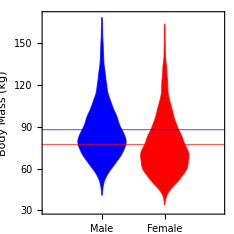

```mathematica
violinchart = DistributionChart[{adultmalemass,adultfemalemass},PlotRange->{ All,{30,170}},ChartStyle-> {Blue,Red},AspectRatio-> 1,Frame-> True, GridLines-> {None,{{malav,Blue},{femav,Red}}},GridLinesStyle-> Directive[Black,Thin],
FrameLabel-> {None,"Body Mass (kg)"},BarSpacing-> Small,FrameTicks-> {{Automatic,Map[{#,NumberForm[#,{4,2}]}&,{malav,femav}]},Automatic},ChartLabels->{Placed[{"Male","Female"},Axis]},
AxesLabel->Style["A",12,Bold,"Arial"],FrameStyle-> Directive[10,Black,"Arial"],ImageSize->mswordsize/2]
```

```mathematica
fds = Map[FindDistribution,{adultmalemass,adultfemalemass}]
```

{ExtremeValueDistribution[76.5198,16.5589],ExtremeValueDistribution[66.7462,16.181]}

```mathematica
equalprob =FindRoot[PDF[fds[[1]],x]== PDF[fds[[2]],x],{x,72}][[1,2]]
```

72.464

```mathematica
theoreticalconfusion[fds,{0,300}]
```

{72.464,{{0.495433,0.278723},{0.504567,0.721276}},0.608355,0.78329}

```mathematica
manwomanlegend = SwatchLegend[{Directive[Blue,Opacity[.5]],Directive[Red,Opacity[.5]]},{"Male","Female"},LegendMarkerSize->12,LegendFunction->"Frame",LabelStyle->Directive[FontSize-> 10]]
```

```mathematica
(*Plot[PDF[fds[[1]],x]/PDF[fds[[2]],x],{x,30,180}]*)
```

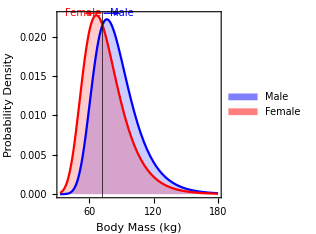

```mathematica
crossoverplot = Plot[{PDF[fds[[1]],x], PDF[fds[[2]],x]},{x,33,180},PlotRange-> All,
PlotRangePadding-> {{Scaled[0.05],Scaled[0.03]},{None,Scaled[0.06]}},
PlotStyle-> {Blue,Red},Filling-> Axis,Frame-> True, AspectRatio->1,GridLines-> {{equalprob},None},
GridLinesStyle-> Directive[Black,Thin],
FrameLabel->{"Body Mass (kg)","Probability Density"},FrameStyle-> Directive[10,Black,"Arial"], FrameTicks->{{Automatic,Automatic},{Automatic,{{33-7,Style["B",12,Bold,"Arial"],0},{equalprob,NumberForm[equalprob,{4,2}]}}}},Epilog->{ 
(*Text[Style["Classification",12,"Arial"],Scaled[{0.97,0.8}],{1,1}],*)
Inset[manwomanlegend,Scaled[{0.97,0.2}],{Right,Bottom}],
{Blue,Thick,Arrowheads[0.04],Arrow[{{equalprob+1,0.023},{equalprob+16,0.023}}],
Text[Style["Male",10,Italic,Blue],{equalprob+18,0.023},{-1,0}],
{Red,
Arrow[{{equalprob-1,0.023},{equalprob-16,0.023}}]},
Text[Style["Female",10,Italic,Red],{equalprob-18,0.023},{1,0}]
}

},ImageSize->mswordsize/2]
```

```mathematica
histoplot =Histogram[{adultmalemass,adultfemalemass},100,"ProbabilityDensity",PlotRange->All,Frame-> True,ChartStyle-> {Blue,Red},AspectRatio-> 1,FrameTicks-> {{Automatic,Automatic}},FrameLabel->{"Body Mass (kg)","Probability Density"},FrameStyle-> Directive[10,Black,"Arial"],ImageSize->mswordsize/2];
```

```mathematica
lineleg = LineLegend[Map[Directive[#,Thick]&,{Blue,Red}],{"Male","Female"},LegendLabel->"Extreme Value",LabelStyle->Directive[10,Black]]
```

```mathematica
extremevalueplot = Plot[{PDF[fds[[1]],x], PDF[fds[[2]],x]},{x,33,180},PlotRange-> All,PlotStyle->Map[Directive[#,Thick]&, {Blue,Red}],AspectRatio-> 1];
```

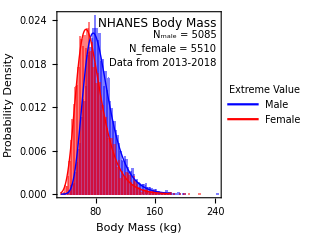

```mathematica
histoextremeplot = Show[histoplot,extremevalueplot,
Frame->True,FrameTicks->{{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},
Epilog-> {Text[Style["NHANES Body Mass",12],Scaled[{0.97,0.97}],{1,1}],
Text[Style[StringJoin["N_male = ",ToString[Length[adultmalemass]]],10],Scaled[{0.97,0.90}],{1,1}],
Text[Style[StringJoin["N_female = ",ToString[Length[adultfemalemass]]],10],Scaled[{0.97,0.83}],{1,1}],
Text[Style["Data from 2013-2018",10],Scaled[{0.97,0.75}],{1,1}],
Inset[lineleg,Scaled[{0.97,0.5}],{Right,Top}]},ImageSize->mswordsize/2]
```

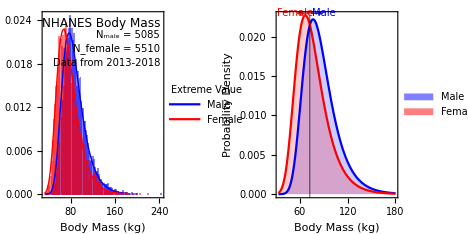

```mathematica
figS11plot = GraphicsGrid[{{histoextremeplot,crossoverplot}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
Export["figureS11plot.tif",Rasterize[figS11plot,ImageResolution->300],"TIFF"]
```

figureS11plot.tif

## Variation of Cg

```mathematica
cgvardata = {0.0160,.0490,.0650,.0790,.1210,.1240,.1490,.1560,.1750,.1860,.2050,.220,.2430,.2810,.2820,.3020,.3350,.4610,.475}
```

{0.016,0.049,0.065,0.079,0.121,0.124,0.149,0.156,0.175,0.186,0.205,0.22,0.243,0.281,0.282,0.302,0.335,0.461,0.475}

```mathematica
Length[cgvardata]
```

19

```mathematica
4
```

4

```mathematica
Median[cgvardata]
```

0.186

```mathematica
Quantile[cgvardata,0.25]
```

0.121

```mathematica
Quantile[cgvardata,0.22]
```

0.121

```mathematica
qxfun[xx_?NumberQ]:=Quantile[cgvardata,xx]
```

```mathematica
FindRoot[qxfun[xq]== 0.10,{xq,0,0.25}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{xq→0.210526}

```mathematica
simpleboot =Table[Median[RandomChoice[cgvardata,19]+RandomVariate[NormalDistribution[0,0.01],19]],{20000}];
```

```mathematica
simpleboot2 =Table[Mean[RandomChoice[cgvardata,19]+RandomVariate[NormalDistribution[0,0.01],19]],{20000}];
```

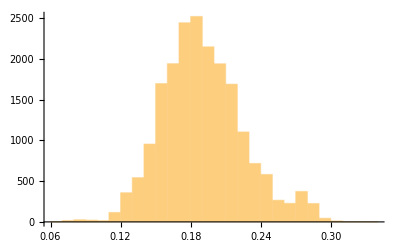

```mathematica
Histogram[simpleboot,{0.01}]
```

```mathematica
Quantile[simpleboot,{0.025,0.5,0.975}]
```

{0.128595,0.18721,0.274645}

```mathematica
Quantile[simpleboot2,{0.025,0.5,0.975}]
```

{0.153597,0.206431,0.265067}

{0.151729,0.205647,0.263835}